```mathematica
stable7=Module[
{f, i,total=0,values, val, lastGood=0,name=FileNameForTuple[{3,5,7}], chunkLenght=100,d1,d2,d3, result={}},
f= OpenRead[name];
values = ReadList[f, Expression, chunkLenght];
Monitor[
While[Length[values] ==chunkLenght,
For[i=1, i≤ Length[values],i++,
If[Mod[i,10000]==0,PrintTemporary[i]];
val = values[[i]];
(*d1=DigitCount[val,5,0];
d2=DigitCount[val,5,1];
If[d1!=d2, Continue[]];
d3=DigitCount[val,5,2];
If[d1≠d3, Continue[]];
*)
d1=DigitCount[val,7,0];
d2=DigitCount[val,7,1];
If[d1!=d2, Continue[]];
d3=DigitCount[val,7,2];
If[d1≠d3, Continue[]];
d2=DigitCount[val,7,3];
If[d1≠d2, Continue[]];
AppendTo[result,val];
lastGood=val;
];
total += Length[values];
values = ReadList[f, Expression, chunkLenght];
],
{total +i, Length[result]}
];
Close[f];
result
]
```

{756,545685233300232150146582052,545685233300233520998828152,946115165836811233932230476475554782796752777266328314967329544954625362470043550662,946115165836811233932230476475554782796752777266328314967329544954625363312367381310,946115165836811233932230476475554782796752777266328314967329544954625363312367616552,3443591475676570436088755718903178569210090750554846300497909009184787551788135942861401976994482257988462141132984410,3443591475676570436088755718903178569210090750554846300497909009184787551788135942861401976994482257988481146348553400,3443591475676570436088755718903181397621516267074163529456403073119356666147205384661226029494475025538086090452051376,3443591475676570436088755718903181397621516267074163532360625119179822849077125868548734170697285104454059817012520180,3443591475676570436088755718903181397621516267074184346362239044290497997459886747618510635373124349194188153574631526,3443591475676570436088755718905442288860604112707337382251179692147301094176051206056145033392363685753391609004007556,3443591475676570436088755718905442288860607923456184312773974753604351010787543279102209701526683010222938601172754526,3443591475676570436088755718905442288860607923456186994415261645265263106614923943049612135802187452020858833359567156,3443591475676570436088755718905442288860607923456186994415261645265263106614923943049612135802187452020858833359569562,3443591475676570436088755718905442288860607923456186994415261645265263106852834220852494411159108804601239936768066436,3443591475676570436088755718905442288860607923456186994415261645265263107408629799980872685866804809871788092041957800,3443591475676570436088755718905442288860607923456266197799005622824474035410538608425158881893964687672712167089863436,3443591475676570436088755718905442289168679682474146851197310664779414582663107646798303276597573425293645852552845152,3443591475676570436088890080131332145080726749277462522882214202905963254801733143150529551495826290678997986435738136,3443591475676570436088890080131332145080726749277462522882214202905963254801733143150529551495826290678997986435738382,3443591475676570436088890080131332145080726749277462522882214202905963254814401935814841185652801224734807136535632760,3443591475676570436088890080131332145080726749277462522882214202905963254814401935814841185652801224734807136536125162,3443591475676570436088890080131332145080728347625840640617097520540326172561541045810754950219427422131085549904863152,3443591475676570436088890080131332145080728617402146763838951002527723188894690290461739427082599335937519447089882012,3443591475676570436088890080131332145080728617402146763838992124058977540052407019239706515181699954632386842041204386,3443591475676570436088890080131332145080728617402146763838994075554973177769617491823664850765546116358017341625959436,3443591475676570436088890080131332145080728617402146763838994075554973177772950093627663613385205613797384254209457026,3443591475676570436088890080131332145080728617402146763838994075554973177772950093627663613385205613797384254209457032,3443591475676570469211220415651442108826648069609949659986224792565757033108935552459726406964147854292602767627348426,3443591475676570469211220415651442108826648069609949659986224792565757033108935552459726406964147854292602767627348432,3443591475676570469211220415651442108826648069609949659986224792565757033108935619667227283574293406695011476340242156,3443591475676570469211220415651442108826648069609949659986224792565757033109899470703038833544269258202077490580485930,3443591475676570469211220415713139870406257171675359047392670942447606933106600939568019631063963712754728243528319552,3443591475676570469211220415713139870406257171675359047392670942447606933106600939568019631063963712754728243898438186,3443591475676570469211220415713139870406257171675359047392670942447606933106600939568019631063963712754728308595878182,3443591475676570469211220415713139870406257171675359047392670942447606933106600939568019631063963712811950695918516302,3443591475676570469211220415713139870406257171675359047392670942447606933106600939568019631063963712811950695918516386,3443591475676570469211220415713139870425157633172879169288142865189393819988156602645156565632472187417721108745097160,3443591475676570469211220415713139870425157633172879169288142982445739793896877583049020197028411597756138917846585300,3443591475676570478106930946836117138897598168629955734890453141060486548083530216989516352423966379538098463188398310,3443591486731918040666897374302481522742027342035841851380562163477887572816513797065626117214733194113263277890646900,3443591486731976369124327375424794109563221545071704359918501039704615712288497676338250833011405035856728365743048406,3443617136513986697175226983009474189099125061683248951012605942104972900055324170770069495214411102681737074464960910,3443617136513986697175226983009474189099125061683251683164515434793934520469684406942073221395431347812200167344238280,3443617136513986697175226983009474189099197074135227007809796447929300906755447464498650172493221314578270784006414030,3443617136513992069705812361424383466954788720492229403511190572477782576395064019100752168018423297241311810893064062,19934443960159030340589280332191158342616289275897701522545579010509487588774253796147395031541997731757264864836799266511298373860359221019806221565662,19934443960159030340589280332191158342616289275897701522545579010509487588774253796147395031542062580343905844618492924724363911954950478310620482895276,19934443960159030340589280332191158342616289275897701522545579010509487588832942115152604141923333790798444390421973090555411625236325037961648460960756,19934443960159030340589280332191158342616289275897701522545579010509487588832942115202601478161552634922720767578352864470038563023708823780276428598132,19934443960159030340589280332191158342616289275897701522545579010509895537841410508029839750924390215699079369796169933269404754634089890484237413050652,19934443960159030340589280332191158342616289275897701522545579010509895537841410508029839750924390215699079369796169933269413541683041279358686524256526,19934443960159030340589280332191158342616289275897701522545579010509902035185681474992210898624026398511634556630992020188900004990855587598035937906280,19934443960159030340589280332191158342616289275897701522545579010509902035185681474992210898624026398511634556630992020188900004990855587598035937907012,19934443960159030340589280332191158342616289275897701522545579010509902035185681514434643199358109320139810970387651427588810263086337535617993655112536,19934443960159030340589280332191158342658949630188405850482643659196584591276657162683830139028250176391768673546722859762669573796372140599275170335786,19934443960159030340589280332191158342658949630188405850482643659196584591279983718003159167360570400929091753504401759757051512366168201961531056671936,19934443960159030340589280332191158342658949630188405850482643660005626934973962997050415383778969999342384353300322353624661343219887105104431213831260,19934443960159030340589280332191158342658949630188405850482643660005626934973963943935980176944830425797702223684260708893225833895663169616925070406926,19934443960159030340589280332191158342658949630188405850482643660005626935068646257860071990529838816856513380180310091026751982281999355359206662288406,19934443960159030340589280332191158342658949630188405878732085092997844119298043120477951183975902660798995461763741325154442197578105762958527855941436,19934443960159030340589280332191158342658949630188405878732085093001606894634871514395925461216125579381187816560639447726866058660749046826973245115780,19934443960159030340589280332191158355444204159638846158498592275941122578034913610962244316294296310528665067171971704915744808433584933396461449629402,19934443960159030340589280332191158355444204159638846158498592275969549266687539889983997891729174826765741510441748404714966604078419809574505912209510,19934443960159030340589280332191158471811146438641777904040695003910135070228120097687177346901338588673920886743089657797329509171188295461593361757806,19934443960159030340589280332237516817570360722584640436793961462928240278951427931795112793814557656686887889212894650583277355307007253380903869297506,19934443960159030340589280332237516817570360722584642159516168395455047907915249537017398699377269636062559269185670583654258737980396211194684105567030,19934443960159030340589280332237516817570361174505649290228394804951365752927973607154212531376988763992325217160119810132578002104729486199372582597750,19934443960159030340589280332237516817570361174505649290228394812493156910998449032585910397838471707390106104839512221537337761544662717556958565332180,19934443960159030340589280332237516817570361174505649290232052115922859031757586807522475453342321823235316912822147054725994562754415708073434200085780,19934443960159030340589280332237516817570361174505649290232052115922859031757586807522475453342321823235317019472401725733171048343196571828066410175262,19934443960159030340589280332237516817570371224057545796717368538835480312984703119815875849673343641571606490207915781099077155289614814300546194179436,19934443960159030340589280332237516817570371224057545796717368538835480312984703119815875849673343641571606490207915781100220955583269899410407972815926,19934443960159030340589280332237516817570371224057545796717368538835480312984703119815979107874062405908152573895753435387269360954332769147645615788262,19934443960159030340589280332237516817570371224057545796717485909237771694209484509619604598357391250518467395662940873569388720253745441537787130863150,19934443960159030340589280332237516817570371224057545796717485909237771694209484509619604598357391250518467395662940873569388720253745441537787130882050,19934443960159030340589280332237516817570371224057545796717485909238073600648776877227347172714693979452327749327194212185088054399082496858283076738810,19934443960159030340589280332237516817570371224057546533285804814329784270145708291675756064153150689556492725155017930947544670488201797684511985234436,19934443960159030340589280332237516817570371224057546533285804814329784270530850737322112276296525113424124031316644339427159941994856625751656984803882,19934443960159030340589280332237516826156089606842591952238523825716130225033352434908743143189123820319755065095269515764470648864323341985390922828312,19934443960159030340589280332237516826156089606842639076469000002109874438359798271468842476023218955998213687465514553663528961045870630970076037194012,19934443960159030340589280332237516826156089606842639076469000002109874438359808095245429605214771597105231838909072854035023359127540057183271975470176,19934443960159030340589280332237516826156089606842639076469000002136208148077208050856474146121177177383875421607387078678871129527965276738351137500180,19934443960159030340589280332237516826156089606842639076469000002136208148077208050856474146121177177383875421607387078678871129527965276738351137500276,19934443960159030340589280332237516826156089606842639076469000002136208148077208050856474146121177177383875421607387078678871129527965276738351137500906,19934443960159030340589280332237516826156089606842639076469000002136208148077208050856474146121177182616649565562850732544904692500870018482552979085280,19934443960159030340589280332237516826156089606842639076469000058551996137895411278091963142857776329376214902065880743726031511486734822469367699785062,19934443960159030340589280332237516826156089606842639076469000058551996137895411278091977649165121762705005751267784931013968531797733154396883857929002,19934443960159030340589280332237516826156089606842639076469000058551996137895411278091977649165121762705005751267784931013968531797733154396887217194506,19934443960159030340589280332237516826156089606842639076469000058551996137895411278091977649165121762705005751267784931013968531797733154529937844628180,19934443960159030340589280332237516826156089606842639076473371745183964407698422496847224085223323971911494456244223134020121958621295157148352148863250,19934443961702301688160416918712626411235180843786110935109098022413973288881804811427226236100766722459543931479989184682718495896178794484924316581262,19934443961725493568650616061898229999571760802603482735551223219831897044878869457607855421882175436783773694073618832660549818680138963456129271570052,19934443961725493568650616061940133147043512275012433928668258754552404306547949493218904821825454209531680071236592799592985262541513580045691283612526,19934443961725493568650616061940133147043512275012433928668258754552404307087119226791352521679167826884190753460440252395629606494129304913496166569380,19934443961725493568650616061940133147043512275012433928668258754552404307087119226791352521679167826884190753460440252395629606606856730126495715719626,19934443961725493568650616061940133147043512275012433928668258754552404308242619164774114964150916044605369748667371876594470479793325799222632425957062,19934443961725493568650616061940133147043512275012433928668258754552404308242619164774114964150984823230259463183789798576084723720776260570898460945176,19934443961725493568650616061940133147043512275012433928668258754552404308242619164774114964150984823724926469399391071312139396497245803403656068460160,19934443961725493568650616061940133147043512275012433928668258754552404308242619164774114964150984823724926469399391071312139396497245803403656104006530,19934443961725493842202715250910831129723737062860621401271880658157324769876333808925616477494247991425688969633357431697752799374501412029461984535780,19934443961725493842202715250910831129723737062860621401273057661783028049667117659582020550545949487725701155249658592255686546565305130677185547460776,19934443961725493842202715250910831129723737062860621401273057661783028049667117659645008130896291197876532792508964076661645759280968332986792601741882,19934443961725493842202715250910831129723737062860621401273057661784394092564832131431897640201194395294717987221622751010836888594083574303021828219676,19934443961725493842202715250910831129723737062860621401273057661784394092564832131431897640201230621774596522669310073339438622633085340237765395082510,19934443961725493842202715250910831129723737462060439726454341887217172957563544475352853822569289274522572595340353384503099806174124805927432149304632,19934443961725493842202715250910831129723737462060439726454341887217172957563544475352853822569289274522572595340353384503099806174124805927432149304680,19934462988143685729367002486587128928118834144867494416327946171598429143535741805489141879383324564198400681815229164672022328293155554048523461350182,19934462988143685729367002486587128928118834144867494416327946171598429143535741805489141879383324564198400681815229164672022328302525104161420023613382,19934462988143685729367002486587128928118834144867494416327946171598460434532550753237362820864104735090690280649464529892897939018362761236175803704432,19934462988143685729367002486587128928118834144867494416327946171598460434532551728718450638909373552323812647665895903526461553114736443638839465625000,19934462988143685729367002486587128928118834144867494416327946171598460434532551743820070273462656175120451073312721794140328784754725221277167041445300,19934462988143685729419529895803661241691606826234412802746984595269868752836987500844835923869958868790832918392675758271265838998641743756904857460180,19934462988144162782710566882983837410722700973863491245887439658723478173346895365721935948972073171374774507372820697872934121085743689561616279694562,19934462988144162782710566882984308138029398792342227489822449589414153823311212394184235933541516009640521645692038199439696189064018851304664423906380,19934462988144162782710566882984308138029398792342227489822819402308157687773429012813195462504974798586156317863174475550531879077675950531081894960880,19934462988144162782710566882984308138029398792342227489822819402308157726596364489781547283906533736112175669692725979589568411499487474540933215006912,19934462988144162782710566882984308138029398792342227489822819402308157726596364489781547283906533736112175669692725979589568411499494734047889962985752,112796951536494996620625909610499310343465930731614560665251897273321875739522788261438437674556028793059790969792803483345732827594853705960887555239311038150,112796951536494996620634762013748035190038648247190321985002242776053388351406986853259062205797498029161474280440172038314302517668694525071981435623067193910,112796951536494996620634762013748035190038648247190321985002242776053388351406986853259062205797498029161474364472068124623875618744961690159444816601679850680,112796951536494996620634762013828916975442255380380875184376223297133476051389017130470789892990333124681349375465693861468885514841531543248024032912941578382,112796951536494996620634762013828916975442255380380875184376223297133476051389017130470789893074798131011362112050115055011944221496410483885123921981699706376,112796951536494996620634762013828916975442255380380875184376223297133476051407571690541033040910988556170030822307189905378120257003320312359930081952201741376,112796951536494996620634762013828916975442255380380875184376223297133476051407571690541033040910988556170030822811022957213861600507231462933507184796749022532,112796951536494996620634795454436131313881608029646799937919183425260755624596537773358094959149090115970559997699039064061388512595371860276847885168711422030,112796951536494996620634795454436131313881608029646799937919183425260755624596537773358094959149090115970559997699039064061388512595374655032160289930765784536,112796951536494996620634795454436131313881608029865260972801123351539518244908888234589842643906380617847091837191429615627765355666812515298193195569212921880,112796951536494996620634795454436131313881608029865260972801123351539518245028811652734461078901509354055885338460001602157150588310269105322972398536722675156,112796951536494996620634795454436131313881608029865260972801123351539518245028811652734461078901509354055885338460001602157150588310271320202198146975151206300,112796951536494996620634795454436131313881608029865260972801123351539518245028811652734461078901509354055885338460001602157150588310271320202198146975151206306,112796951536494996620634795454436131315638344858466802889111192697665275515621594163921289574563059293235405568376235344656600348402651283147185077735959459432,112796951536494996620634795454436131315638344858466802889111192697665275515621594163921291102174268464999872962142001360597111738798069069572536969192161125150,3673939830223430883852894685485716528100300844735189183418066588522777210242581936538916536177593738964276493175130295273640930370799839727688308367954492684175100109432,3673939830223430883852894685485716528100300844735189183418066588522777232564101512005973290584762537586909479181483379439382125911440128944932590938176298187604057142032,3673939830223430883852894685485716528100300844735189183418066588522777232564101512005973290584762537586970704954257218363161040430047158772016704373264611747926135171900,3673939830223430883852894685485716528100300844735189183418066588522777232564101512005973290584763735016734026757144449041223270472081851809707980748304846479065059378410,3673939830223430883852894685485716797073833523708813160216805875291200189071629008232446206813669420893004982755152809638191136638934360729631305450844788751287959018750,3673939830223430883852894685485716797073833523708813160216805875291200189071629008232446206813669420893004982755152809638191136638934360729631305495463614942230764547150,3673939830223430883852894685485716816137007173393851229804551294681976564394405554355252114930460420543030748580225005995510989279254094196914768830323877433838244238412,3673939830223430883852894685485716816137007173393851229804551294681976564394405554355252114930460420543030748580225005995510989281750413513254989526699808739813822343802,3673939830223430883852894685485716816137007173393851229804551294681976564394405554355252114932501559700484352045863171995985084743179393058494098610709922323218334023250,3673939830223430883852894685505988764124173191304935161684691266720586043626024408897701373922544905045913357643989531942006018178441540905491306922600107402838393003780,3673939830223430883852894685505988764124173191304935161684691266720586043626024408897701373922544905045913357643989531942006018178441540905491306922600413331637031359506,3673939830223430883852894685505988787391062418257600482364234873177977876346148964447785133108877755887536075934843644605728767192753835708221748038437190252076924015760,3673939830223430883852894685505988787391063232616017264130567959021487116007750193667608020660669392282009987293775402269571711378087130881404304649950697937806643395002,3673939830223430902479623860846297459424273912550525325760949064946721437685258695404403230840429481537242375688554410227617820225567895030530519142837827416451425817010,3673939830223430902479623860846297459424273912550525325760949064946721437685258695404403230840429481612557039859948223706213488589236604618076672486441567085432201348186,178727883154877881333311355655049727760103910621406134149551725866465374164091034540965165482199123993484655580944973020937947706424908736074961595313617325474118720743718629500119562626,178727883154877881333311355655049727760103910621406134149551725866465374164091034540965165482199123993484655580944973020937947706424908736074961595313624583245505975649373765784043473402,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997012831849054380762559518063191503891586090107031399310598304806751302,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997012831849054380762559518063191503891586090107031399310598304806757506,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997012831849054380762559518063191503892347802469186710193657990825082186,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997012831849054380762559518063191503892347802469186710193657990825085126,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997012831849054380762559518063191503892347802469186710193657990825085252,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997025973715941182875890556282229395997724641787619780423738099682585650,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997025973715941182875890556282229395997724641787619780423738099955163286,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998717239283988078248774360803469928036715497613406544177637500359648789775750656053738714149660578386,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998717243905434906368210284172230458532508679945017634515853924975745669644340649673705673596703678432,178727883154877881333311355655049727760103912777158417726832434749931110055325827124327225087489820099964473023367422394382803347582164049992511103972693576235722894873047943182424613130,178727883154877881333311355655049727760103912777158417726832434749931110055325827124327225087489820099964473023367422394382803347582164049992511103972693576235722894873047943182426257130,178727883154877881333311355655049727760103912777158417726832434749931110055325827124327225087489820099964473023367422396781469239783482720472941148007711304264376531446115989991992284376,178727883154877881333311355655049727760103912777158417726832434749931110055368129539145459211970034515453235264316566631603207226493844995499618481860285757021223125459401748999535251276,178727883154877881333311355655049727760103912777158417726832434749931110055370462027328251335016244016662631110637938313844319811929050232987279057250909121669712481172385335583996210260,178727883154877881333311355655049727760103912777158417726832434749931110055370462027328251335016244016662631110637938313844319811929050232987279057250909121712627244274764751495676579662,178727883154877881333311355655049727760103912777158417726832434749931110055818719026642198482678628465198868402896357040900550117859172152372070983128633578517492334741726056289111738412,178727883154877881333311355655049727760103912777158417726832434749945902334940375989315542333242258429393202954870168292592020756047520607304730964173832388733062688531725625228782187626,178727883154877881333311355655049727760103912777158417726832434749945902334940375989315542333242258429393638486473963231909128533279402979269268995090614596620514672491018781655382926252,178727883154877881333311355655049727760103912777158417726832669998646343311980183515129810542301335927896762430928516697501723659497858205167542375324565638815781157667057542768555254556,178727883154877881333311355655049727760103912777158417726832669998646343311980183515129810542301335927896762430928516697501723659497858205167542375324565638815781157667057542768555484380,178727883154877881333311355655049727760103912777158417726832669998646343311980183515129810542301335927896762430928516697501723659497858205167542375324565638815781157667057542768555491436,178727883154877881333311355655049727760103912777158417726832669998646343311980625489104762951394488820599058508999867812772310882108711711923772923531928910574063916735965005535898944530,178727883154877881333311355655049727760103912777158417726832669998646343311980625489104762951394488820599058508999867812772310882108711711923772923531928910837829471955302754438477032500,178727883154877881333311355655049727760103912777158417726832669998646343311980625489104762951394488820599058508999867812772310882108711711923772923531928910837829471955302754438477032512,178727883154877881333311355655049727760103912777158417726832669998646343311980625523897585475500974077630829446611207720251279433563477371454636215287551194815129298718357316145557515636,178727883154877881333311355655049727760103912777158417726832669998646361650924457564758414747904289997467380417889447560188216329166558163887682658815148216945846967415576462923643069536,178727883154877881333311355655049727760103912777158417726832669998646361650924457564758414747904289997467380417889447560188216329166558163887682658815148216945846967415576462923643069632,178727883154877881333311355655049727760103910621406134149551725866465374164091034540965165482199123993484655580944973020937947706424908736074961595313617325474118720743718629500119562626,178727883154877881333311355655049727760103910621406134149551725866465374164091034540965165482199123993484655580944973020937947706424908736074961595313624583245505975649373765784043473402,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997012831849054380762559518063191503891586090107031399310598304806751302,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997012831849054380762559518063191503891586090107031399310598304806757506,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997012831849054380762559518063191503892347802469186710193657990825082186,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997012831849054380762559518063191503892347802469186710193657990825085126,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997012831849054380762559518063191503892347802469186710193657990825085252,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997025973715941182875890556282229395997724641787619780423738099682585650,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998071082848868144503122738621997025973715941182875890556282229395997724641787619780423738099955163286,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998717239283988078248774360803469928036715497613406544177637500359648789775750656053738714149660578386,178727883154877881333311355655049727760103910621406134149551725866470638996830260864998717243905434906368210284172230458532508679945017634515853924975745669644340649673705673596703678432,178727883154877881333311355655049727760103912777158417726832434749931110055325827124327225087489820099964473023367422394382803347582164049992511103972693576235722894873047943182424613130,178727883154877881333311355655049727760103912777158417726832434749931110055325827124327225087489820099964473023367422394382803347582164049992511103972693576235722894873047943182426257130,178727883154877881333311355655049727760103912777158417726832434749931110055325827124327225087489820099964473023367422396781469239783482720472941148007711304264376531446115989991992284376,178727883154877881333311355655049727760103912777158417726832434749931110055368129539145459211970034515453235264316566631603207226493844995499618481860285757021223125459401748999535251276,178727883154877881333311355655049727760103912777158417726832434749931110055370462027328251335016244016662631110637938313844319811929050232987279057250909121669712481172385335583996210260,178727883154877881333311355655049727760103912777158417726832434749931110055370462027328251335016244016662631110637938313844319811929050232987279057250909121712627244274764751495676579662,178727883154877881333311355655049727760103912777158417726832434749931110055818719026642198482678628465198868402896357040900550117859172152372070983128633578517492334741726056289111738412,178727883154877881333311355655049727760103912777158417726832434749945902334940375989315542333242258429393202954870168292592020756047520607304730964173832388733062688531725625228782187626,178727883154877881333311355655049727760103912777158417726832434749945902334940375989315542333242258429393638486473963231909128533279402979269268995090614596620514672491018781655382926252,178727883154877881333311355655049727760103912777158417726832669998646343311980183515129810542301335927896762430928516697501723659497858205167542375324565638815781157667057542768555254556,178727883154877881333311355655049727760103912777158417726832669998646343311980183515129810542301335927896762430928516697501723659497858205167542375324565638815781157667057542768555484380,178727883154877881333311355655049727760103912777158417726832669998646343311980183515129810542301335927896762430928516697501723659497858205167542375324565638815781157667057542768555491436,178727883154877881333311355655049727760103912777158417726832669998646343311980625489104762951394488820599058508999867812772310882108711711923772923531928910574063916735965005535898944530,178727883154877881333311355655049727760103912777158417726832669998646343311980625489104762951394488820599058508999867812772310882108711711923772923531928910837829471955302754438477032500,178727883154877881333311355655049727760103912777158417726832669998646343311980625489104762951394488820599058508999867812772310882108711711923772923531928910837829471955302754438477032512,178727883154877881333311355655049727760103912777158417726832669998646343311980625523897585475500974077630829446611207720251279433563477371454636215287551194815129298718357316145557515636,178727883154877881333311355655049727760103912777158417726832669998646361650924457564758414747904289997467380417889447560188216329166558163887682658815148216945846967415576462923643069536,178727883154877881333311355655049727760103912777158417726832669998646361650924457564758414747904289997467380417889447560188216329166558163887682658815148216945846967415576462923643069632,178727883154877881333311355655049727760103912777158417726832669998646361650924461077055137086437913358041061728954689720799557126690468667225454623140386481109241729121521702644356022762,178727883154877881333311355655049727760103912777158421747985996388971321988105077738217718309245243286456362103336053329674118440680738335594958256904636483814616930689519142194154470130,178727883154877881333311355655049727760103912777158421747985996388971321988105077738217718309245243286456362103336053329674118440680738335594958256904636483814616930689519142194154470256,178727883154877881333311355655049727760103912777158421747985996388971321988105077738217718309245243286456362103336053329674118440680738335594958256904636483814616930689519142194154688752,178727883154877881333311355655049727760103912777158421747986316252357267408424053367113111643695327254861746482247840496033923690977989387081147437812878714671551255785062417030285237530,178727883154877881333311355655049727760103912777158421747986316252357267408424053367113111643695327254861746974698211475891485098834839928190612260442236739085784764486637325348261878880,178727883154877881333311355655049727760103912777158421747986316252357267408424053367113111643695327254862178275150957076300567152376544711811328164675495062787741888353657819747910265902,178727883154877881333311355655049727760103912777158421747986316252357267408424053367113111643695434896272193452612999534491262930092662294758471766678465185215935376520756290750100506886,178727883154877881333311355655049727760103912777166469911292579628283357893200570851421245797321557828570335633123628785196951717866309445511593502875698278660667954478338260846242284500,178727883154877881333311355655049727760103912777166469911292579628283357893200570851421245797321557828570335633124867217756005921453807388101722734019999052519885013121429008681019960152,178727883154877881333311355655049727760103912777166469911292579628283357893419526391173743864084505172442915564420770824147510575664297319596950002490334709377671482041897895814282034552,178727883154877881333311355655049727760103912777166469911292579628283357893419526391173743864084505172442915564420770824147510575664297319596950002490334709377671482078850274201722688180,178727883154877881333311355655049727760103912777166470064804610574316243519094484619292956127933590161551887551495157013556096354013512054018000342674636172034330140130282067262572828286,178727883154877881333311355655049727760103912777166470064804610574316251900073701467788914930437699870851700063774650793395000332295057460787274447924667049947020283246665105623117660000,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978060809746116729119501786325096324253285767933874079359606853501300942880511415719221448157682,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978060809810815909297155859750356204301366110872771581505403684562316651023455262897651682457552,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978060809810815909297155859750356204301366110872771581505403684562316808996253102020338623846932,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978100781413885943570994166758520017794182171560087394366403351997515135106124120374343822443900,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978100781413885943571000872792844096245084893874962201670065241702563587159366911622076534020312,178727883154877881333311355655049727760103912777166470064804610574316801871465447729980913566450486980075469553627654423596128255235933929101280554510116644544285662920776028784688281282,178727883154877881333311355655049727760103912777166470064804610574316801871465447729980913566450486980075469553627654423596128255636890773230177255919270039041395659008947507552836882500,178727883154877881333311355655049727760103912777166470064804610574316801871465447729980913566450486980075469553627654423596128255636892897247308245716217279826196292601895436126975160260,178727883154877881333311355655049727760103912777158421747986316252357267408424053367113111643695327254861746482247840496033923690977989387081147437812878714671551255785062417030285237530,178727883154877881333311355655049727760103912777158421747986316252357267408424053367113111643695327254861746974698211475891485098834839928190612260442236739085784764486637325348261878880,178727883154877881333311355655049727760103912777158421747986316252357267408424053367113111643695327254862178275150957076300567152376544711811328164675495062787741888353657819747910265902,178727883154877881333311355655049727760103912777158421747986316252357267408424053367113111643695434896272193452612999534491262930092662294758471766678465185215935376520756290750100506886,178727883154877881333311355655049727760103912777166469911292579628283357893200570851421245797321557828570335633123628785196951717866309445511593502875698278660667954478338260846242284500,178727883154877881333311355655049727760103912777166469911292579628283357893200570851421245797321557828570335633124867217756005921453807388101722734019999052519885013121429008681019960152,178727883154877881333311355655049727760103912777166469911292579628283357893419526391173743864084505172442915564420770824147510575664297319596950002490334709377671482041897895814282034552,178727883154877881333311355655049727760103912777166469911292579628283357893419526391173743864084505172442915564420770824147510575664297319596950002490334709377671482078850274201722688180,178727883154877881333311355655049727760103912777166470064804610574316243519094484619292956127933590161551887551495157013556096354013512054018000342674636172034330140130282067262572828286,178727883154877881333311355655049727760103912777166470064804610574316251900073701467788914930437699870851700063774650793395000332295057460787274447924667049947020283246665105623117660000,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978060809746116729119501786325096324253285767933874079359606853501300942880511415719221448157682,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978060809810815909297155859750356204301366110872771581505403684562316651023455262897651682457552,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978060809810815909297155859750356204301366110872771581505403684562316808996253102020338623846932,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978100781413885943570994166758520017794182171560087394366403351997515135106124120374343822443900,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978100781413885943571000872792844096245084893874962201670065241702563587159366911622076534020312,178727883154877881333311355655049727760103912777158421747986316252357267408424053367113111643695327254861746482247840496033923690977989387081147437812878714671551255785062417030285237530,178727883154877881333311355655049727760103912777158421747986316252357267408424053367113111643695327254861746974698211475891485098834839928190612260442236739085784764486637325348261878880,178727883154877881333311355655049727760103912777158421747986316252357267408424053367113111643695327254862178275150957076300567152376544711811328164675495062787741888353657819747910265902,178727883154877881333311355655049727760103912777158421747986316252357267408424053367113111643695434896272193452612999534491262930092662294758471766678465185215935376520756290750100506886,178727883154877881333311355655049727760103912777166469911292579628283357893200570851421245797321557828570335633123628785196951717866309445511593502875698278660667954478338260846242284500,178727883154877881333311355655049727760103912777166469911292579628283357893200570851421245797321557828570335633124867217756005921453807388101722734019999052519885013121429008681019960152,178727883154877881333311355655049727760103912777166469911292579628283357893419526391173743864084505172442915564420770824147510575664297319596950002490334709377671482041897895814282034552,178727883154877881333311355655049727760103912777166469911292579628283357893419526391173743864084505172442915564420770824147510575664297319596950002490334709377671482078850274201722688180,178727883154877881333311355655049727760103912777166470064804610574316243519094484619292956127933590161551887551495157013556096354013512054018000342674636172034330140130282067262572828286,178727883154877881333311355655049727760103912777166470064804610574316251900073701467788914930437699870851700063774650793395000332295057460787274447924667049947020283246665105623117660000,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978060809746116729119501786325096324253285767933874079359606853501300942880511415719221448157682,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978060809810815909297155859750356204301366110872771581505403684562316651023455262897651682457552,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978060809810815909297155859750356204301366110872771581505403684562316808996253102020338623846932,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978100781413885943570994166758520017794182171560087394366403351997515135106124120374343822443900,178727883154877881333311355655049727760103912777166470064804610574316251902852668563074124978100781413885943571000872792844096245084893874962201670065241702563587159366911622076534020312,178727883154877881333311355655049727760103912777166470064804610574316801871465447729980913566450486980075469553627654423596128255235933929101280554510116644544285662920776028784688281282,178727883154877881333311355655049727760103912777166470064804610574316801871465447729980913566450486980075469553627654423596128255636890773230177255919270039041395659008947507552836882500,178727883154877881333311355655049727760103912777166470064804610574316801871465447729980913566450486980075469553627654423596128255636892897247308245716217279826196292601895436126975160260,178727883154877881333311355655049727760123460843812695857231389036833957582548531441117953593232559285455419905014715607149240537262708054209309561948714622625781461866927261398314925882,178727883154877881333311355655049727760123460843812695887084708044167769286863603727857292509169907743172524894439925193539471094179681394685895636569526409950879292752163433898988397536,178727883154877881333311355655049727760123460843812695887084708044167769286863603727857292509169907743172524894439957018631979373258549156109274189754846446715315852779473058327932538810,178727883154877881333311355655049727760123460843812695887084708044167769456498311435275742092964057994673053672301676331544550833156746945363796935716216468674421804966646412721204070052,178727883154877881333311355655049727760123460846246075175906444360209511958713651663020070496971191707565439054775308653281520594806267145479582180550389269274819536525670098158496284636,178727883154877881333311355655086294751386519129128627858730970717105201527193220607581100543957961931894604312416881500568133641826502012679113441778721279752068456344394803808594538250,178727883154877881333311355655086294751386519129128627858730970717105741353766651501961774020814774249298947097837155980830869009201722063413135778544668454582719770642367593597463757660,178727883154877881333311355655086294751386519156433264806970205848603023266230530509337391501353726309366079121822130696506837102943226280949990357528305005873498400199425793795431719676,178727883154877881333311355655086294751386519156433264806970205848603023266230530509337391501353726309366079121822130697451866397949085600103123969275786495704760590091671985852560657560,178727883154877881333311355655086294751386519156433264806970205848603023266230530509337391501353726309366079121822130697451866397949085600103123969275786499176705405356002472915146600252,178727883154877881333311355655086294751386519156433264806970205848603023266230530509337391501353726309366079121822130697451866441255630251771914585437812867769934851684039638734621206526,178727883154877881333311355655086294751386519156433264806970205848603023266230530509337391501353726309366079121822130709033290745692115463283617608894120429799400992878139160920518516880,178727883154877881333311355655086294751386519156433264806970205848603023266230530509337391501353726309366079121822130709033290745692115463283617608894120429799400993862777240828125115880,178727883154877881333311355655086294751386519156433264806970205848603023266230530509337391501353726309366079143927902688240962297407597829052525703635675059840803180307452684242260253176,178727883154877881333311355655086294751386519156433264806970205848603023266230530509337391501353726309366079143927902688240962297407597829052525703635675059840803180307452684242260253260,178727883154877881333311355655086294751386519156433264806970205848603023266230530509337391501353726309366079143927902688240962297407597829052525917908697335282449517484367889602588456380,178727883154877881333311355655086294751386519156433264806970205848603023266230530509337391501353726309366079143927902688240962297407597829052624583273008626068989049919681763642602125880,178727883154877881333311355655086294751386519156433264806970205848603023266230530509337391501353726309366079143927902688240962297407601091910674127177135102668110779876244209359487115936,178727883154877881333311355655086294751386519156433264806970205848603023266230530509337391501353726309366079144032253314393591122905130824493237370957956705135445256176617356115830506302,178727883154877881333311355655086294751386519156433264806970205848603023266230530509337391501353726309366079510580460416668866122833446150273171468659595916515551533028870240364271491386,178727883154877881333311355655086294751386519156433264806970205848603030922322884936676047094300968941836533326599368991892315085755092135070587493320588555490832105502801918396114069626,178727883154877881333311355655086294751386519156433264806970205848603030922322884936676047094300968941836533326599368991892315085755092135070587493322684623603854686999707722854260178750,178727883154877881333311355655086294751386519156433264806970205848603030922322884936676047094300968941836533326599368991892315085755092135070666624419931935203222331786826706704164485012,178727883154877881333311355655086427656654476127011305542929826442934901267832831981193521490163802996886216116954202685285867430975586066180234346201812265101413061300602933107239176310,178727883154877881333311355655086427656654476127011305542929826442934901267832831981194135514304672699777042178384673216587240058578376598209243498205497141279949808688846615157471285282,178727883154877881333311355655086427656654476127011305542929826442934901267832831981194138247061067974729475447594170278113487838227989167991829619620358502627459287092476578835814569386,178727883154877881333311355655086427656654476127011305542929826442934901267832832015486619962591077073281875883864353148260398535567566692811143646285580985127034597561364843049389238150,178727883154877881333311355655086427656654476127011305542929826442934901267832832015486619962591077073281875883864353148260398535567566692811143646285580985127034597561364843049389238156,178727883154877881333311355655086427656654476127011305542929826442934901267832832015486619962591077073281875884127067874303168329660778362398115689263482187484275349640989799812562600760,178727883154877881333311355655086427656654476127011305542929826442934901267832832015486619962591077073281875884127067874303168329660778362398115725329565108550028558875632866895771523286,178727883154877881333311355655086427656654476127011305542929826442934901267832832015777049742008978176107541943731594853668039633419346563938057522563171831292499101169780292825217756500,178727883154877881333311355655086427656654476127011305542929826442934901267832832015777049742008978176107541943731594853668039633419346563938057522563171831292499101169780292825217756506,178727883154877881333311355655086427656657742774844096048321820024089914026416525154458937214211376374549087542155781755462928711084426918965443162737668112060564483524994855102611906530,178727883154877881333311355655086427656657742774844096048321820024089914026416525154458937214211376374549087542155781755462928711084426918965443162737671232662993885101678609534238367052,178727883154877881333311355655086427656657742774844096048321820024089914026416525154458937214211377779274196925114845508706825433566472710552633044039385623866285486529021378640498929512,178727883154877881333311355655086427656657742774844096048321820024089914026416525154458937214211377779274196925114845508706825433566472710552633044039741099696479623246267918441420863386,178727883154877881333311355655086427656657742774844096048321820024089914026416525154458937214211377779274196925114845508706825433566472710552633044039741099696479623246267918441425819050,178727883154877881333311355655086427656657742774844096048321820024089914026416525154458937214211377779274196925138690854774670687988405447518895476760507122253405569400203331033315423286,178727883154877881333311355655086427656657742774844096048321820024089914026417427232431747269916398051208593944628822324903623748407610958625860407861218166417981382886294086500746881910,178727883154877881333311355655086427656657742774844096048321820024089914026419259114041421069916200423860776846486045001603476536746737064146576239054420149672316652806836250655521500156,178727883154877881333311355655086427656657742774844096048321820024089914026419259114041421069916200423860776846486045001603476536746737064146576239054420149672316653104512826721797269632,178727883154877881333311355655086427656657742774844096048321820024089914026419259114057779153844463479162144936579529447492437774353620406287730715627512327284599473738684864966408616386,178727883154877881333311355655086427656657742774844096048321820024089914026419259114057902074878547619362954441170970274314221627834311618386715306694886785692248401621311668739282131562,178727883154877881333311355655086427656657742774844096048321820024089914026419259114057902074878547645844510755688406559276795916233411044483828457876770201319760109707787614627023907786,178727883154877881333311355655086427656657742774844096072333791795228481134288893736823275296297215403793439898113180058438649915110279873557940126941315699070939468445539578283711114032,178727883154877881333311355655086427656657742774844096072333791795228481134288893736823275296297215403793439898113180058438649915110279873557940126941315699070939468445539578283715800800,178727883154877881333311355655086427656657742774844096162121849940331588902795133007735889573786911837619358982766700111829283583822648345747842667643507105007840586835564278486352035186,178727883154877881333311355655086427656657742774844096162121849940331588902795133007753873587938259287833890276663261940348074761462361219580409394117580902150093513028753892889408610752,178727883154877881333311355655086427656657742774844096162121849940331588902795133625205843703155015590849259184583492738785797254217338281388901311287345732817418296131933331512943444512,178727883154877881376793451997194467460952229287605096215273011000677438580730786813153256503846973352601660827493475869830569781491178454425276115380885698872755194463149185345726645036,178727883154877881376793451997194467460952229287605097613656104598197063430318227312305809964853748444266296926407795116998661514068704120025878071402790041524821573132362964642387125800,178727883154877881376793451997194467460952229287605097613656104598197063430318227312306027409464726676877900308690704905717360375225157217045606457344595135349743935735941511154075112632,178727883154877881376793451997194467460952229287605097613656104598197063430318227312306027409464726676877900466503354597545910527359459181875281624031175973734969912488012523715185960652,178727883154877881376793451997194467460952229287605097613656104598197140611753559690000088572136294760665484100866316466091550840003317221136598354770375615384553117753713273054248942062,178727883154877881376793451997194467460952229287605097613656104598197140611753559690000088572136294760665531676580822538722420076851108738968271779390864398032661091052366281134277850756,178727883154877881376793451997194467460952229287605097613656104598197140611753559690000088573026454319041420070391626028451312396559906617036659831622022279819212860696757989087426756252,178727883154877881376793451997194467460952229287605097613656104598197140611753559690000088573026460649969830324834983853411371616945695031651877066363836007950234489532130918127551285036,178727883154877881376793451997194467460952229287605097613656105015725762658364333794576241468694183071081532386083363078275063765851035658412920020055648974949581325287049046637451566430,178727883154877881376793451997194467460952229287605097613656105015725762658364333794576241468702648892110231010819781961156797056692899536879367318601379460236864986363772148474677922160,178727883154877881376793451997194467460952229287605097613656105015725762658364333794576241468702648892110231010819781961156943047473528195725912476721699853280821705463647962524904491426,178727883154877881376793451997194467460952229287605097613656105015725762658364333794576313098807366798293651369978621988397597785523715289408651103020845915898914380187409630737425938802,178727883154877881376793451997194467460952229287605097613656105015725762658364333794577081527644259435963959692480550483028347941963772760826456924981206249249768002371505013342844563880,178727883154877881376793451997194467460952229287605097613656105015725762658364333794577081649055134734049857301845601179760097345651661907102647357604507335567353322261990304754885550300,178727883154877881376793451997194467460952229287605097613656105015725762658364333794577081649055134734049857301845601179760097345651661907102647357942178309085721501529948833527103675882,178727883154877881376793451997194467460952229287605097613656105015725762658364333962149188171921890010538934506547694510682717315550423779372874847465198804684842501301017426361439628406,178727883154877881376793451997194467460952229287605097613656105015725762658364333962149188171921904493940116299041349344937168161108096730564257652652493733307073742579591416543041015802,178727883154877881376793451997194467460952229287605097613656105015725762658364333996621473110830613962970912107810862595220126219317078035168580617276608850488731546604758270271494332176,178727883154877881376793451997194467460952229287605097613656105015725762658364333996621473110830613962970912187929722402585881827023432118275449908398862886871941769774857566846056648402,178727883154877881376793451997194467460952229287605097613656105015725762658364333996621473110830613962970912187929722402585922151966060012327968796589353707181435480804866036300304785812,178727883154877881376793451997194467460952229287605097613656105015725762658364333996621473110835274668141300546283081748656512764574488102488808620473935917520799819621863938357530082186,178727883154877881376793451997194467460952229287605097613656105015725762658364333996621473110835274668141300546283081748656512764574488102488808620473935917537182105931938770448049710652,178727883154877881376793451997194467460952229287605097613656105015725762658364333996621473110835274668141300546283081748656512764574488396588930369913254913902018617333915451263721285650,178727883154877881376793451997194467460952229287605097613656228271673650258580233501160202324607047849773597726536269146903189726390194502447326677374775587672852035800052765046652928762,178727883154877881376793451997194467460952229287720321672732570927055043668328943193496216032604553378091511985022415813777559783399566802810657943928452488373324794220984121017403163430,178727883154877881376793451997194467460952229287720321672732570927055043668328943193496216032604553378091511985022415813777559783399566802810657943928452488628699263781993873903820882182,178727883154877881376793451997194467460952229287720321672732570927055043668328943193496216032604553378091511985022415813777559783399566802810657943928452488628699263781993873907775866902,178727883154877881376936602782059306781334350150514165373477834681598389784694665747722601930787727622900070400581805773596541141690896167587511310430635870807268797689796543164613398256,178727883154877881376936602782059306781334350150514165373486161818250739432883832494747886385108090269921513115474348905809724102294433106070737367646136745283081835331635956954707035000,178727883154877881376936602782059306781334350150514165373486161818250739432883832494747901433678126630500972272805699268624135272953348771617439722073461213376579973884290447266223535276,178727883154877881376936602782059306781334350150514165373486161818250739432883832494747901433678126630500972272805699290746085971595836350079130827655145460597930015437437059097287207160,178727883154877881376936602782059306781334350150514165373486161818250739432883832494747901433684191989718822738685913756694894927773173270655829346934511279743776685575311802259824707176,178727883154877881376936602782059306781334350150514165373486161818250739432883832494747901433684191989718822738685913757193405649124213978502270104625137107871487622382176522902933629632,178727883154877881376936602782059306781334350150514165373486161818250739432883832494747901433684191989718822738685913757502827709643668243237282965709773924810177676424469976269541187756,178727883154877881376936602782059306781334350150514165373486161818250739432883832494747901433684191989718822738685913757502827709643668475594775788386671577520689611334222040021067226550,178727883154877881376936602782059306781334350150514165373486161818250739432883832612724155892791030705883864145156873157259433765559638941479837448445193001917512435549860197067240706552,178727883154877881376936602782059306781334350150514167318341539270344856639136798614657980302162685298223162805845836687028335430705112660677726662073564654358888101223772758825979006500,178727883154877881376936602782059306781334350150514167318341539270344856639136798614657980302162685298223162805845836687028335430705112660677726662073564654358888101223772758825979023306,178727883154877881376936602782059306781334350150514167318341539270344856639136798614657980302162685298223162805874441564868982549022549418595158073088709531343300512079125642562764097156,178727883154877881376973374427631438609245073650302989759047469165514427653222817293040125791858774652609372725396372000853783621204858970326571573153406121084947381543219705507883313810,178727883154877881376973374427631438609245073650302989759047469165832213100544746637443387299208793292201924774353226054753586370611574105194552249536092815809831080401385812408555472530,178727883154877881376973374427631438609245073650304435108335871386035588684009951912525740839727176626505155761895299576010161658570898727828834839216217951902669855471256494332373237750,178727883154877881376973374427631438609245073650304435108335871386035588684009951912525740839727176626505155761895299576010161658570898727828834839216217951902669855471256494332373237810,178727883154877881376973374427631438609245073650304435108335871386035588684009951912525740839727176626505155761895299576010161658570898727828834839216217951902669855471256494332373242130,178727883154877881376973374427631438609245073650304435108335871386035588684009951912525740839727176626505155761895299576010161658570903320035120149083551701100093313531963943526975084552,178727883154877881376973374427631438609245073650304435108335873457430778529133080938047076833712617580384801610852990649187567849466828626699387054881488978800993907715396980318911051306,178727883154877881376973374427631438625186757959163682721442991832407566479642485936087237017224052049799993363876463964187383894861020387258853037718432751082690927650121441725219547760,178727883154877881376973374427631438625186757959163682721442991832407566479642485936087237017224052049799993363876463964187383894861020387258853037718432751082690927650121442572121268812,178727883154877881376973374427631438625186757959163682721442991832407566828548849690123282542073447506233645584932340529998284159254023469105472112072900649866368744764404907386577109386,178727883154877881376973374427631438625186757959163682721442991832407566828548849690123282542073447506233645584932340529998284159254023469105472112072900649866368744764404907386577109632,178727883154877881376973374427631438625186757959163682721442991832407566828548849690123282542073447506233645584932340529998284159254023469105472112072900649866368744764404907386787110310,178727883154877881376973374427631438625186757959163682721442991832407566830245086444198299929822407200445132251006110915838049585376957441459708983447111480982951634655955356781103913426,178727883154877881376973374427631438625186757959163682721442991832407566830245086444198299929822407200445132251006110915838049585376957441459708983478308553569180365169764736220078145250,178727883154877881376973374427631438625186757959163682721442991832407566830245086444198299929822407200445132251006110915838049585376957441459708983478308553569180365169764737091409148182,178727883154877881376973374427631438625186757959163682721442991832407566830245086444198299929822407200445132251006110915838049585376957441467706420040558471578121191318339063601672459532,178727883154877881376973374427631438625186757959163682721442991832527704402860505220205139955570168715058054210707644883269533849797644159624150545289557654999010849013987584693861407756,178727883154877881376973374427631438625186757959163682721442991832527704402860505220205139955570168715058054210707644883269533849797644159624150545289557654999010849013987584693861407756,178727883154877881376973374427631438625186757959163682721442991832527704402884575460076878445562408926148651831712650096315901112922621367325371478163561547582885879278782009896582523150,178727883154877881376973374427631438625186757959163682721442993232401183658457901091095403274330656299971508290497228231062244026345638070349473410517266985427445650115681762768605646910,178727883154877954787688921265642421517981624863032044949397384104203061708268796580016095167528669015518193592173844877132083667859017405013479000819871415899330919842565541846213688926,178727883154877954787688921265642421517981624863032044949397384104203061708268796580016095167528669015518193592173844877132084917979216072024333529633687391015805911536638775677807531312,178727883154877954787688921265642421517981624863032044949397384104203061708268796580016095167528669063576297454484120509263198432924766966007311445954752744505462521732156780257930272636,178727883154877954787688921265642421517981624863032044949397384104203061708268802082883757486389859511365879976879064867897598431007923879694091441617235781499496921987979631392846491412,178727883154877954787688921265642421517981624863032044949397384104203061708268802082883757486389859515127066779377640806864404858011918947202938029472749136014411347918809059493713297056,178727883154877954787688921265642421517981624863032044949397384104203061708268802082883757486389859515127066779377640806864404858011918947202938029472749136014411347918809059493723443926,178727883154877954787688921265642421517981624863032044949397384104203061708268802082883757486389865656863743391888216974126712433211619572679778124879764260735471092218783574219980631380,178727883154877954787688921265642421517981624863032044949397384104203061708268802082883757486389865656863743391888216974126712433211619572679778124879764260735471092218783574219980631410,178727883154877954787688921265642421517981624863032044949397384104203061708268802082883757486389865656863743391888217018967775152239866992671127321545858571903408442102795793530277453786,178727883154877954787688921265642421517981624863032044949397384104203061708268802082883757486389865656863743391888217018967775152239866992671752705225003701353495830896929018008353710882,178727883154877954787688921265642421517981624863032044949397384104203061708268802082883757486389865656863743391888217018967775152239866992671752705225008533535298314915733436890882907660,178727883154877954787688921265642421517981624863032044949397384104203061708268802082883757486389865656863743391918599157280521001027604280311365144551869181044910220705402397474873860810,178727883154877954787688921265642421517981624863032044949397384104203061708268802082883757486426017757922511979314643226734520024395257300670793915167378043279314004162019394838871253806,178727883154877954787688921265642421517981624863032044949397384104203061708268802082883757486426017757922511979314643226734520024395257300670793915167378043279314004162019394838871268812,178727883154877954787688921265642421517981624863032044949397384104203061708268830777214262182948932234894643077015608981755497261806981001449068058710900433265226573020893119879689632050,178727883154877954787688921265642421517981624863032044949397384104203061708268830777214262182948932234894643077015608981755497261806981001449696006072125000412567431124296789002786126400,178727883154877954787688921265642421517981624863032044949397384104203061708268830777214262182948932234905578623966317650327118428851635011747244119809633448587224125379994985571839844650,178727883154877954787688921265642421517981624863032046223789310914669618471024578144492825843352900927318689858199542921119709545350960869564842286153275848675708525162046055908305253382,178727883154877954787688921265642421517981624863032046223789310914669618471484374530352578811251641172550569921133488933612233263187077298272964190906579065649653925935116527619740428802,178727883154877954787688921265642421517981624863032046223789310914669618471484374530352578811251641172868063401302093139010321498611578104214293229801581648430248634407356282351332894652,178727883154877954787688921265642421517981624863032046223789310914669618471484374530352578811251641172868118877502078576036263758210450982132539657977105948085391670504659313398557535630,178727883154877954787688921265642421517981624863032046223789310914669618471484374530352578811251641172868118877502078576036263758210450982132539657977105948085391670504659313398557535636,178727883154877954787688921265642421517981624863032046223789310914669618471484374530352578811251641175698477371310676383517244462044034662371093293575921939020298566155198239172608222756,178727883154877954787688921265642421517981624863032046223789310914669618471484374530352578811251641175698477371310676383517244462044034662371093293575921939020298566155198239172608222762,178727883154877954787688921265642421517981624863032046223789310914669618471484374530352578811251641175698477371310676383517244462044034662371093293575921939020298566155198239172608222810,178727883154877954787688921265642421517981624863033229048540623599015971774288138055723539428813406886912405753062980066001101565677846801234144841608157192351824489684785126874316518750,178727883154877954787688921265642421517981624863033229048540623599015971774288138055723539428813406886912405753062980066001101565677846801234144841613053394324193504169720174018616210652,178727883154877954787688921265642421517981624863033229048540623599015971774288138055723539428813406886912405753062980066001101565677846801234144842987117132499483651744442482037609938762,178727883154877954787688921265642421517981624863208144400950912814060292697814728006374803303919987607708680936011489788092090348524779602859990930710002800244939864881992577400021878926,178727883154877954787688921265642421517981624863208145675438818478700473405515536037428121998357694145943961396796576207434393811520829945647041764880766409555674764344399652285401267152,178727883154877954787688921265642421517981624863208145675438818478700473405515536037428121998357694145943961396796576207434393811520829945647041764880766409555674764344399652285401284636,178727883154877954787688921265642421517981624863208145675438818478700473405515536037428121998357694145943961396796576207445843384502340355484696292646077792153446382844510307690918538286,178727883154877954787688921265642421517981624863208145675731941205437329148323421491471768275855023031519110640443116451306799285112131281462240398132497332994628842227165817566516445152,178727883154877954787688921265642421517981624863208145675731941205437329148323421491471768275855023031519110640443116451306799285112131281462871733428618804330183901864290905335791578300,178727883154877954787688921265642421517981624863208145675731941205437329148323421491471768275855023031519110640443116451307154721001020838232919999277923216254282310137811323098752454032,178727883154877954787688921265642421517981624863208145675731941205437329148323421491471768275855023096208444630648652961529755899150975172541110962747311680782301269668722821393379097662,178727883154877954787688921265642421517981624863208145675731941205437329148323421491471768275864192266400099427346124861815168299915432005150559914902169170181899821849790689468273456562,178727883154877954787688921265642421517981624863208145675731941205437329148323421491471768275864192266400099427346124861815168299930323277901166114102196792703066659610033554150634938136,178727883154877954787688921265642421517981624863208145675731941205437329148323421491471768275864192266400099427346124861815168364275048752345812541744615637366689323671844029425550897630,178727883154877954787688921265642421746310145875271150392841593981300379527354624571648429476178357478859442807323870563224870205686095726602517167261855805709376266316261411446801593882,178727883154877954787688921265642421746310145875271150392841593981300379527354624571648429476178357478859442807323872148290514666255304236349272215337120032076581269513159982636772442026,178727883154877954787688921265642421746310145875271150392841593981300379527354624571648429476178357478859442807323872148290514666255304236349272215337120032076581269513159982636818860186,178727883154877954787688921265642421746310145875271150392841593981300379527354624571648429476178357478859442807323872148290514666255304236349272215337124978814397524379494858552347843902,178727883154877954787688921265642421746310145875271150392841594032784369753773900717458923169362544823296367669748266779705746956367771210278892107084165560400436778643789335243234940810,178727883154877954787688921265642421760801183582783073333667967408066382082322785431557381078564237152215733563404473450695866523012158058446053200979180685881150589558856991645568923252,178727883154877954787688921265642421760801183582783073333667967408066382082322785431557381078564237155036501415619301303160315305504538691228132340077314099155226985234631195381416100636,178727883154877954787688921265642421760801183582783073333667967408066382082322785431557381078564237155036501415619301303160315305504538691228132340077314099164220039967358246986194225062,178727883154877954787688921265642421760801183582783073333667998654663479325769723014868045883786646246440317267518761437893437378246118269531175465963919953540059090972094581924387615680,178727883154877954787688921265642421760801183582783073333667998654663479325769723014868045883786646246440317267518761437893437378246118269531175465963927152281051392108273545241818367010,178727883154877954787688921265642421760801183582783073333667998654663479325769723014868045883786646246440317267518761437893437688521703206280886403479632383789885450609653096786008673402,178727883154877954787688921265642421760801183582783073333667998654663479325769723014883751701495741180525182078255314868500280315392030784414471355218111667009019295164137500959580891280,178727883154877954787688921265642421760801183582783073333667998654663479325769723014883751720049819852517546753298367559045820508031586096155335892736734146060279744014454461744648909530,178727883154877954787688921265642421760801183582783073333667998654663479325769723014883754343030559349093850437809630479597375654161247830661749019023877056290809672341063621527649251300,178727883154877954787688921265642421760801183582783073333667998654663479325769723014883754343030559349093850437809630479597375654161248042762121347805082976378038326288000154116801331310,178727883154877954787688921265642421760801183582783073333667998654663479325769723014883754343030559349093850437809630533171705833498294075731812162526552931981241145219328405013745034410,178727883154877954787688921265642421760801183582783073333667998654663479325769723014883754343030559349093850437809630533171705833498294075731812162526552931981241145219328428267113381256,178727883154877954787688921265642421760801183582783073333667998654663479325769723014883754343030559349093850437809630533270922061883795313101094041923301614599439483516038616375751960280,178727883154877954787688921265642421760801183582783073333667998654664550040999906822328387541016724410219074659023263593281258556423519676354885480379145890649743547673970459052797741430,178727883154877954787688921265642421760801183582783073333667998654664550040999906822328387541016724410219074659023263593281258556423519676354885480379145890649743547673970459052797741436,178727883154877954787688921265642421760801183582783073333667998654664550040999911198468890301498626115077472442347989933542658627146627755457988100798893250614146946076181912423105631402,178727883154877954787688921265642421760801183582786263288218099197960543365973389286301132753439784427338800217124464860106601318535459223909058975424672468100634344347444099458078945136,178727883154877954787688921265642421760801183582786263288218099197960543365973389286301132753439784427338800217124464860106601318535459223909058975424672468100636624927071233405078687550,178727883154877954787688921265642421760801183582786263288218099197960543365973389286301132753439784427338804867043891683739032572550337737662326905297335067920373687901332882306264537800,178727883154877954787688921265642421760801183582786263288218099197960543365973389286301132753439784427338804867043891683739032572550337737662326905297335067920373687901332882306264537806,178727883154877954787688921265642421760801183582786263288218099197960543365973389286301132753439784427338804936108928680452709756127704563553498012945422217872794277110767507540597772682,178727883154877954787688921265642421760801183582786263288218099197960543365973389286301132753439784427338804936108928680469632977757372619216229365018948484587401780711545964364113671936,178727883154877954787688921265642421760801183582786263288218099197960543365973389286301132753439784427338804936108928680469632977757372619216229365018948484587401780711545964364113672176,178727883154877954787688921265642421760801183583300806080262284369535542473927020160084695892335089585284472624056243270154868414391177700376729353753927002184792805731738134017455968886,178727883154877954787688921265642421760801183583300806080262284369535542473927020160084695892335089585284472624056243270832631487448758578278045636512009805365248636573612920545756332806,178727883154877954787688921265642421760801183583300806080262284369535542473927020160084695892335089585284472624056243270832632819119542295292488381990333069801999978067589996533705972550,178727883154877954787688921265642421760801183583300806080262284369535542473927020160084695892335089585284472624056243270832640577544331156273119643474900228750662815095615983901371897180,178727883154877954787688921265642421760801183583300806080262284369535542473927020160084695892335089585284472624056243270832640577544331156273121622458191559755977388853275909582813440636,178727883154877954787688921265642421760801183583300806080262284369535542473927020160084695892335089585284472624056243270832640577544331156273121622458191559755977388853275918897953241926,178727883154877954787688921265642421760801183583300806080262284369535542473927020160084695892335089585284664524480898441518175460856045064641606244850916917130779619369534038891700175006,178727883154877954787688921265642421760801183583300806080262284369535542473927020160084695892335089585284664532955473573549986273997265048616813269810599536290250836405888787414620100126,178727883154877954787688921265642421760801183583300806080262284369535542473927020160084695892335089585284664532955473573549986273997265048616813269810599536290250836405899723055967694536,178727883154877954787688921265642421760801183583300806080262284369535542473927020160084722263054923714456324760882226746886686166430883156183229680660339802535403436291888717962705893880,178727883154877954787688921265642421760801183583300806080262284369535542473927020160084722263054923714456324760882226746886686166430883156214135360240204518343322683402004284271740788936,178727883154877954787688921265642421760801183583300806080262284369535542473927020160084722263054923714456324760882226747496932955875670793637143542246199998554003785409405351263770032686,178727883154877954787688921265642421760801183583300806080262284369535542518236104225533638117971711217655880684397619421209153654526794334495272279618132287497141665229218110970725004652,178727883154877954787688921265642421760801183583300806080262284369535542518236104225533638117971711217655912564171600927042078758152719481529045291027049731023391486558929090345773626260,178727883154877956031549771937931401504053360942455449545166830941969903367298389320663678376431793207851373273191423219863728229011607822499034355369042443090614658221972026898684141380,178727883154877956031549771937931401504053360942455449545166830941969903367298389320663681562190825669010056653853267823386026562684290233356524405599619237009834742360203790625353707532,178727883154877956031549771937931401504053360942455449545166830941969904452689407237900585646222204194746672592088819123380286564871621573583821253686696918751186742524042172303535725162,178727883154877956031549771937931401504053360942455449545166830941969904452689407237900585646222204194746672592098453085164170071231022861384478459373167608293914823252701802432141579676,178727883154877956031549771937931401504053360942455449545166830941969904452689407512510226007490083944655715588660439463029437485302232489970737909626966257074105936336961021650391501506,178727883154877956031549771937931401504053360942455449545166830941969904452689407512510226007490083944655715588660439463029437485302232489970737909626966262751030299820676906660424256302,178727883154877956031549771937931401504053360942455449545166830941969904452689407512510226007490083944655715588660439463029437485302232489970737909626966262798669059092477517103771895032,178727883154877956031549771937931401504053360942455449545166830941969904452689407512510226007490083944655715588660439463029437793758579383456140859192572784745065901467945623359730960280,178727883154877956031549771937931401504053360942455449545166830941969904452689407512732307485679370574453804361231249813313996643726451753789090292456912050078320482078197145240576287760,178727883154877956031549771937931401504053360942455449545166830941969904452689407517881960140153952557382694034564528733850645587546275724957642561453415231972794431262080697186348550252,178727883154877956064358871072688192485736724345750406659505116165988678979606669258076134058885586103952681579529268487088489049464252191298806220603488278834268601658957202987421988400,178727883154877956064358871072688192485764918898438193117957761060018055819320911906357994565917061230721323306248993495247414170476928000814883910087890372161236014256206514352364065800,178727883154877956064358871072688192485764918898438193117957761060018055819320911906357994565917061230721323306248993495247414170476928000814883910087890372161236014256206514352364065926,178727883154877956064358871072688192485764918898438193117957761060018055819320911906357994565917061230721323306248993495247414170476928000814883910087890372161236014256206514352364065932,178727883154877956064358871072688192485765108765680473927421069612128422704203462872864761707635924258183946245798315818705501157333453492424078318812647468143582494974440231551538085630,178727883154877956064358871072688192485765108765680473927421069612128422704203462872864761707635924258183946245798315818705501157333463716368772320489225143431139907281783226196409003886,178727883154877956064358871072688192485765108765680473927421069612128422704203462872864761707635924273229979882625801918608522200968627007509901310294652177503034176576510476269845785250,178727883154877956064358871072688192485765108765680473927421069612128422704203462872864761707635924280755412245354722853124586504302542309975101045910009540239262419247949165352101647026,178727883154877956064358871072688192485765108765680473927421069612128422704203462872864761707636034636853132286892236800067693765569088180632683676822836145041019355215864697304027375180,178727883154877956064358871072688192485765108765680473927421069612128422704203462872864761707636034636853132286892236801703288420982897060882339463375712013205499436163144707858158317160,178727883154877956064358871072688192485765108765680473927421069612128422704203462872864761707636034636853132286892236801703288420982897060882339498992838464592735987395673981824242345280,178727883154877956064358871072688192485765108765680473927421069612128422704215548236913894132666768807028783574520300058366553070434160126908033776742662867356662335813713784395039565652,178727883154877956064358871072688192485765108765680473927421069612128422704215548236913894132666768807028783574520300059292079255282072257756915352547392560613825945597076992994877909386,178727883154877956064358871072688192485765108765680473927421069612128422704215548236913894132666768807028783574777827297971627423925395387132274340302913952986709895806639671370137125280,178727883154877956064358871072688192485765108765680473927421069612128422704215548236913894132666839499192215381743118115297022617660519182366024276721327630016199785739257359376342376312,178727883154877956064358871072688192485765108765680473927421069612128422704215548236913894132666839499192215381743118115297022617660519182366024312784702834800569863998128167732200162786,178727883154877956064358871072688192485765108765680473943418160243916149490682520219775616304341513878367248240716023007293099819994581490396998412508921269912025548563008404853832616430,178727883154877956064358871072688192485765108765680473943418160243916149490682520219775616304341513878367248240716023007293099819994581490396998412508921269912025548563008404853832617156,178727883154877956064358871072688192485765108765680473943418160243916149490682520219775616304341513878367248240716023007293099819994581490396998414786903465941613704908614162762795709406,178727883154877956064358871072688192485765108765680473943418160243916149490682520219775616304341513878367248240716023007293099819994582474309481261722830029477424930858994034768068365752,178727883154877881376973374427631438625186757959163682721442991832527704402860505220205139955570168715058054210707644883269533849797644159624150545289557654999010849013987584693861407756,178727883154877881376973374427631438625186757959163682721442991832527704402860505220205139955570168715058054210707644883269533849797644159624150545289557654999010849013987584693861407756,22231046748701290275679233449232638275273146460473389344279708246023344265727740435461801175969337772851388500772670779705674966815800136896675992302740463268603177698889409394548881258504913638000500660,22231046748701290275679233449232638275273146460473389344279708246023344265727740435461801175969337772851388500772670779705674966815800136896675992302740463268603177698889409394548881258504913638002032532,22231046748701290275679233449232638275273146460473389344279715006111307459575135514317908768004333078029137305283648613208957088817047941596606016894582863311562900903252457287614943847444096387941828776,22231046748701290275679233449232638275273146460473389344279715006111307459575135514317908768004333078029137305283648613208957088817057102072143116118665885753946559469005001576097822982696270156495020132,22231046748701290275679233449232638275273146460473389344279715006111307459575135514317908768004333078029137305283648613208957088817087093710371288598701745746261679593683881015930335971801872627299313876,22231046748701290275679233449232638275273146460473389344279715006111307459575135514317908768004333078029137305283648613208957088817087093710372557178908447140151121506281897928202203477042408032736820126,22231046748701290275679233449232638275273146460473389344279715006111307459575135514317908768004333078029137305283648613208957088817087093710372557178908447140151121506281897928208513374761242989798829636,22231046748701290275679233449232638275273146460473389344279715006111307459575135514317908768004333078029137305283648633068486861495001233562812112894701860840480645369955837050442384611671094575490393902,22231046748701290275679233449232638275273146460473389344279715006111307459575135514318139092834474478757669630377864041636429165886206287572869164231636731751978965168085437985152389931800862135373207130,22231046748701290275679233449232638275273146460473389344279715006111307459575135514318139092834474478757669630377864041636429165886206287572869164231636731751978965168085437985152389931800862135373207136,22231046748701290275679233449232638275273146460473389344279715006111307949332559752982310603374226462946283213162323637435565641212360622423661551019328425170809588456805473979493278492214726635839882510,22231046748701290275679233449232638275273146460473389344279715006111340900539804035243107018561271332910489373920959175284838016941563860046656299861337624388436461489806886766535050421953228157050969062,22231046748701290275679233449232638275273146460473389344279715006111340900539804035243107018561271332910489373920959175284838016941563860046656299861337624388436461489806886770023523905113320472461516250,22231046748701290275679233449232638275273195588004376037340166367380422210275506616460906945897714344316390707481711697214380695671853140748388938602539772007849163475910507034138665983215531503275803756,22231046748701290275679233449232638275273195588004376037492009807054499364544711565404591644781789546827483632451724106482092622506340980480590312084010749111956295759288635157721025364702270553236722002,22231046748701290275679233449232638275273195588004376037492009807054499364544711565404591644781789546827483632451724106482092622506340980480590312084010749111956295759288635157721025364702270553236722050,22231046748701290275679233449232638275273195588004376037492009807054499364544711565404591644781789546827483632451724106482092622506340980480590312084010749111956295759288635157721025364702270553236738760,22231046748701290275679233449232638275273195588004376037492780017199666531706100292627851426069459154606257704532149241667541990773641171978777643943564447277516734480418854775853851999404469606222815652,22231046748701290275679233449232638275273195588004376037492780017199666531706100292627851426124147723884770410228978478414332974919972007269899131665181024394479760444857603536108169938708439253002921880,22231046748701290275679233449232638275273195588004376037492780017199666531706100292627851426124147723884770410228978478414332974919972007269899131665181024394479760444857603536108169938708439253002922132,22231046748701290275679233449232638275273195588004376037492780017199666531706100292627851426124147723884770410228978478414332974919972007269899131665181024394479760444857603536108169938708439253002922186,22231046748701290275679233449232638275273195588004376037492780017199666531706102375382552688171320135286520956344133322290562878980628995461967224800891669243158438397010754053587024294567246594347844506,22231046748701290275679233449232638275273195588004376037492780017199666531706102375382552688171320135286520956344133322290562878980628995461967224800891669243158438397010754053587024294583900830615413762,22231046748701290275679233449232638275273195588004376037492780017199666531706102375658250276194546990406848206493851807351690471665421194793528560899198255686453133965891948948414354102914376435793364062,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667041814170116303789538358474042205522145272812604282481892478975407228006021285902847030,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667041814170116303789538358474042205522145272812604282481892478975407228006021285902847036,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667041814170116303789538358474042205522145272812604282481892478975407228006021285902847756,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667041814853959780203059431860117604567581920971857168778384922000986600354423525656443752,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667041814853959780203059431860117604567581920971857168778384922000986600354423525656443800,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667041814853959780203059431860117604567581920971857168778384922000986600354423525656443806,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667044709081006504050902776810831225796355410749203354687816112366319911304002423156735006,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667044709081006504050902776810831225796355410749203354687816112366319911304002423166593912,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667044709081006504050902776810831225796438897677512874231951237110428037345551333515659676,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410669871456422530049383074539510635309747698313373530432280062998063687691392899658471507006,22231046748701290275679233449232638275273195588004376037492780017199666531706200013091566646793354816511615083936989123920543674060888969701653034422591426108964957633596027890744300082410438735609882032,22231046748701290275679233449232638275273195588004376037492780017199666531706200013091566646793354816512433454110197384846600789427596120562181611945761822641317698191036311175063725012970589674086910802,22231046748701290275679233449232638275273195588004376037492780017199666531706200013091566646793354816512433454110204445179426748133713679577808110646734222820113336139288040178529463008657475617973438912,22231046748701290275679233449232638275273195588004376037492780017199666531706200013091566646814371636641807399764518659524457074342597250343005912080777354404705834293175576070067500748398331497140660306,22231046748701290275679233449232638275273195588004376037492780017199666531706200013091566646814371636641807399764518659524457074342607343051992845271889337209923456895062378511313000963655477460264628812,22231046748701822837329662140777200884314173481244945771249460170340661661118663666065260386219796783829773077559104327358740287801656007816798001755312457547848809549277331416705555517082334486389531876,22231046748701822837329662140777200884314173481244945771249460170340661661118663666065260386219796789121365810917066405645290878979863876666916845060129010305268330963546262050689093060935535799922847802,22231046748701822837329662140777200884314173481244945771249460170340661661118663666065260386219796789121365810917066405645290878979863876686511989886154391018169531349845476597795500874603939822386725280,22231046748701822837329662140777200884314173481244945771249460170340661661118663682109888810211937983610161803801243719167437845184546673498438166984442401479020682078182751703964021319586010803760265632,22231046748701822837329662140777200884314173481244945771249460170340661661118663682109888810211937983610161803801243719167437845184546673498438166984442401479020682078182751704480155635243080359242692000,22231046748701822837329662140777200884314173481244945771249460170340661661118663682109888810211937983610161803801243719167437845184546673498438166984442415909622344250635714170499729443038488198800803256,22231046748701822837329662140777200884314173481244945771249460170340661661118663682109888810211937983610161803801243719167437845184546673498438166984442415909622344250635734644710557546024940502941428132,22231046748701822837329662140777200884314173481244945771249460170340661661118663682109888810211937983610161803801243719167437845184546673498438166984442415909622344250635748503997736686838189712455116376,22231046748701822837329662140777200884314173481244945771249460170340661661118663682109888810211937983610161803801243719167437845184546673498595723831775286998039440123791777355003311570077442385518082682,22231046748701822837329662140777200884314173481244945771249460170340661661118663682109888810211937983610161803801243719167437845184546673498595723831775291142294693008101802716284903976944683077707897686,22231046748701822837329662140777200884314173481244945771249460170340661661118663682109888810211937983610161803801243719167585808260693032075716481491279307607712270655793028026895602662101957125608378132,22231046748701822837329662140777200884314173481244945771249460170340661661118663682109888810211937983610161803801243719167585808260693032075717359977596723350147887102261452468192006880347946478537910786,22231046748701822837329662140777200884314173481244945771249460170340661661118668857450447725187612203294111108083506112120771318678296502299175126597803027438225792813445885044353950255220451510314875150,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995674868009628551265103753091614778259929976713506158612614622613755899829443913180964544686797833473197742126,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995674868009628551265221203791982415694124954455260911054427224145297152873031905547181423844412061654649312630,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995674868009628551912795415801394730062013325432677930393572681603067738032246189054523827526571966127988445010,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995674868009628551912795415809070374432786292657757388184850848845404467116581828863567791226571568298607907032,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995674868009628551912795415809070374432786292657757388187464496073328986483855698243532707924025581393381754630,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995674868009628551912795415809070374432786292657757388783729182329114268782270245877971408966606656716552928306,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995674868009628551912795415809070374432786292657757388783729182329114268782270245877971408966606656716552929026,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995674868009628551912795415809070374432786292657757388783729182329114428118296616823957889616793157513928282160,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995674868532336928257686780749723233121876299303589853643597252060544828123703820676488365084650537170998240926,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995674868532466048615802828860311395779804093603928440926285380565596883374106694255199405744676823426770476500,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995674868532466048615802828860311395779804093603928440926285380565596883374106694255199405744677090820371656886,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995674868532466048615802828860311395779804093603928440926285380565596883374106694255199405744677090820371659382,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995679117959551347420435474150153851827013078573777995642541919799671165991615205486759334997955446053584851252,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995679117959551347420435474150153851827027347318215245412692163932337313781076411964473897867231511757871113936,22231046748701822837329662140777200884314173481244945771249460170340661663119869932318715458995679121528992144867861861141947261803046394237272249936849631152134211644648538659464266346421764440932504432,22231046748701822837329662140777200884314173481244945771249460170340661663119869932385110915581828705794054579689794472700392722286460687295127882843716128197648740494880627514231167929316278109621878810,22231046748701822837329662140777200884314173481244945771249460170340661663119869932385110915581828705794054579689794472700392722286675189246734289837881066179490388906004070895579226369265220959965344376,22231046748701822837329662140777200884314173481244945771249460170340661663119869932385110915581828705794054579689794472700393120409864710806536884930662238360136494564688607043445252332415777039183750152,22231046748701822837329662140777200884314173481244945771249460170340661663119869932385110915581828705794054579689794472700393120409864710810072058567982799667236661701260729209409912385371686868282115756,22231046748701822837329662140777200884314173481244945771249460170340661663121796174159251604564274912474135974068125053093058932106664986983497825125570604557261962802481901118884619737296113141215254426,22231046748701822837329662140777200884314173481244945771249460170340661663121796174159251604564274912474135974073125399114229776605394332291549353470529443627916011155592599626113782721905824347483000632,22231046748701822837329662140777200884314173481244945771249460170340661663121796174159251604564274912474135974073125399114229776605394332291549353470529443627916011155592599626113782721905824347513688400,22231046748701822837329662140777200884314173481244945771249460170340661663121796174159251604564274912474135974073125399114229776605394332291549353470529443627916011155592599626113782721905824347513692180,22231046748701822837329662140777200884314173481244945771249460170340661663121796174159251604564274912474135974073125399114229776605394332291549353470529443627916011155592602167401347533541318709777444002,22231046748701822837329662140777200884314173481244945771249460170340661663121796177086489092697167378844706859102765384572229251457075703787795417955693967860695974115835071028793614820326352235423850280,22231046748701822837329662140777200884314173481244945771249460170340661663121800343667516425961476859067102249686434160541380235921503369406712170128831608455343209567292816764166025528373718300803297802,22231046748701822837329662140777200884314173481244945771249460170340661663121800343667516425961476859067102249686434160541380235921531732532286835573494717124559686152638147915225952166737126955687610912,22231046748701822837329662140777200884314173481244945771249460170340661663121800343667516425961476859067102249686434160541380235921531732532287126693519620579317618130784302932098052557533361402600472786,22231046748701822837329662140777200884314173481244945771249460170340661663121800343667516425961476859067102251007644847629189593026802373044626734089011917416046583551581518815684831038141731306152757676,22231046748701822837329662140777200884314173481244945771249460170340661663121800343667516425961476859067102251007644847629189593026802373044626734089011917416046583551581518815684831038142438508891501526,22231046748701822837329662140777200884314173481244945771249460170340661663121800343667516425961476859067102251007644847629189593026802373044626734089011917416046583551581518815684831179680851179447832032,22231046748701822837329662140777200884314173481244945792771593588463126828632624696603502950805940845363980263835309163843049857082031781149207804160088304460496207271665339531397500127554157415869156430,22231046748701822837329662140777200884314173481244945792771593588463126828632624696603502950805940845363980352372335725401886700522033428951779534178987786855591191140345165926355688102978351602111335902,22231046748701290275679233449232638275273146460473389344279708246023344265727740435461801175969337772851388500772670779705674966815800136896675992302740463268603177698889409394548881258504913638000500660,22231046748701290275679233449232638275273146460473389344279708246023344265727740435461801175969337772851388500772670779705674966815800136896675992302740463268603177698889409394548881258504913638002032532,22231046748701290275679233449232638275273146460473389344279715006111307459575135514317908768004333078029137305283648613208957088817047941596606016894582863311562900903252457287614943847444096387941828776,22231046748701290275679233449232638275273146460473389344279715006111307459575135514317908768004333078029137305283648613208957088817057102072143116118665885753946559469005001576097822982696270156495020132,22231046748701290275679233449232638275273146460473389344279715006111307459575135514317908768004333078029137305283648613208957088817087093710371288598701745746261679593683881015930335971801872627299313876,22231046748701290275679233449232638275273146460473389344279715006111307459575135514317908768004333078029137305283648613208957088817087093710372557178908447140151121506281897928202203477042408032736820126,22231046748701290275679233449232638275273146460473389344279715006111307459575135514317908768004333078029137305283648613208957088817087093710372557178908447140151121506281897928208513374761242989798829636,22231046748701290275679233449232638275273146460473389344279715006111307459575135514317908768004333078029137305283648633068486861495001233562812112894701860840480645369955837050442384611671094575490393902,22231046748701290275679233449232638275273146460473389344279715006111307459575135514318139092834474478757669630377864041636429165886206287572869164231636731751978965168085437985152389931800862135373207130,22231046748701290275679233449232638275273146460473389344279715006111307459575135514318139092834474478757669630377864041636429165886206287572869164231636731751978965168085437985152389931800862135373207136,22231046748701290275679233449232638275273146460473389344279715006111307949332559752982310603374226462946283213162323637435565641212360622423661551019328425170809588456805473979493278492214726635839882510,22231046748701290275679233449232638275273146460473389344279715006111340900539804035243107018561271332910489373920959175284838016941563860046656299861337624388436461489806886766535050421953228157050969062,22231046748701290275679233449232638275273146460473389344279715006111340900539804035243107018561271332910489373920959175284838016941563860046656299861337624388436461489806886770023523905113320472461516250,22231046748701290275679233449232638275273195588004376037340166367380422210275506616460906945897714344316390707481711697214380695671853140748388938602539772007849163475910507034138665983215531503275803756,22231046748701290275679233449232638275273195588004376037492009807054499364544711565404591644781789546827483632451724106482092622506340980480590312084010749111956295759288635157721025364702270553236722002,22231046748701290275679233449232638275273195588004376037492009807054499364544711565404591644781789546827483632451724106482092622506340980480590312084010749111956295759288635157721025364702270553236722050,22231046748701290275679233449232638275273195588004376037492009807054499364544711565404591644781789546827483632451724106482092622506340980480590312084010749111956295759288635157721025364702270553236738760,22231046748701290275679233449232638275273195588004376037492780017199666531706100292627851426069459154606257704532149241667541990773641171978777643943564447277516734480418854775853851999404469606222815652,22231046748701290275679233449232638275273195588004376037492780017199666531706100292627851426124147723884770410228978478414332974919972007269899131665181024394479760444857603536108169938708439253002921880,22231046748701290275679233449232638275273195588004376037492780017199666531706100292627851426124147723884770410228978478414332974919972007269899131665181024394479760444857603536108169938708439253002922132,22231046748701290275679233449232638275273195588004376037492780017199666531706100292627851426124147723884770410228978478414332974919972007269899131665181024394479760444857603536108169938708439253002922186,22231046748701290275679233449232638275273195588004376037492780017199666531706102375382552688171320135286520956344133322290562878980628995461967224800891669243158438397010754053587024294567246594347844506,22231046748701290275679233449232638275273195588004376037492780017199666531706102375382552688171320135286520956344133322290562878980628995461967224800891669243158438397010754053587024294583900830615413762,22231046748701290275679233449232638275273195588004376037492780017199666531706102375658250276194546990406848206493851807351690471665421194793528560899198255686453133965891948948414354102914376435793364062,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667041814170116303789538358474042205522145272812604282481892478975407228006021285902847030,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667041814170116303789538358474042205522145272812604282481892478975407228006021285902847036,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667041814170116303789538358474042205522145272812604282481892478975407228006021285902847756,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667041814853959780203059431860117604567581920971857168778384922000986600354423525656443752,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667041814853959780203059431860117604567581920971857168778384922000986600354423525656443800,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667041814853959780203059431860117604567581920971857168778384922000986600354423525656443806,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667044709081006504050902776810831225796355410749203354687816112366319911304002423156735006,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667044709081006504050902776810831225796355410749203354687816112366319911304002423166593912,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410667044709081006504050902776810831225796438897677512874231951237110428037345551333515659676,22231046748701290275679233449232638275273195588004376037492780017199666531706200013082054846348517061548345569410669871456422530049383074539510635309747698313373530432280062998063687691392899658471507006,22231046748701290275679233449232638275273195588004376037492780017199666531706200013091566646793354816511615083936989123920543674060888969701653034422591426108964957633596027890744300082410438735609882032,22231046748701290275679233449232638275273195588004376037492780017199666531706200013091566646793354816512433454110197384846600789427596120562181611945761822641317698191036311175063725012970589674086910802,22231046748701290275679233449232638275273195588004376037492780017199666531706200013091566646793354816512433454110204445179426748133713679577808110646734222820113336139288040178529463008657475617973438912,22231046748701290275679233449232638275273195588004376037492780017199666531706200013091566646814371636641807399764518659524457074342597250343005912080777354404705834293175576070067500748398331497140660306,22231046748701290275679233449232638275273195588004376037492780017199666531706200013091566646814371636641807399764518659524457074342607343051992845271889337209923456895062378511313000963655477460264628812,22231046748701822837373682956319899074977161729223642921520948417853536386807212849964790990891968598053817172474274182088633534921746872949325454690566633747028168266450651363372110809415460211234876412,22231046748701822837373682956319899074977161729223642921520948417853536386807212849964790990891968598053817172474274182088633534921746872949325454690566633747028168266450651363372111024349735262960941262,22231046748701822837373682956319899074977161729223642921520948417853536386807212849964790990891968598053817172474274182088633706248331909395941037579527576775133814015550514391176637493079671706860320282,22231046748701822837373682956319899074977161729223642921520948417853536386807212849964790990891968598053817172474274182088633706249112474742062155669968472871786618142352025517641594822825184186396523280,22231046748701822837373682956319899074977161729223642921520948417853536386807212849964790990891968598053817172474274182088633706249114460802706601240355366831923177720085518808299699808782128487552772560,22231046748701822837373682956319899074977161729223642921520948417853536386807212849964790990891968598053817172474274182088633706249114460802706601240355366831923177720085518808299699808782128487562929012,22231046748701822837373682956319899074977161729223642921658189318183131827897121229161636502188956334481171078256835604773142332011684590906689255341218374465756400074579522970979502837660989607189878432,22231046748701822837373682956319899074977161729223642921658189318183131827897121229161636502188956334481171078256835604773142332011684590906689255341218374465756400074579522970979502837660989607190345010,22231046748701822853576463615280014161114159640769565160698320073737066071816489549717151199076923739333541274693697370751977206998959370852113385585435849073245980068723136004718893291128827058457988752,22231046748701822853576463615280014161114159640769565160698320073737066071816489549717151199076923739333569170788888106688392858728447556000639130984413137622987239466310009266122505120938534854113475786,22231046748701822853576463615280014161114159640769565160698320073737066071816489549717151199076923739333569170788888128353034200650858277753034284662365867676274431422564256829005900304106376690928145030,22231046748701822853576463615280014161114159640769565160698320073737098239149924938802341672174688150796662640218941113017564352959084989634445463969030394542825013218703476472370731849151352876515663900,22231046748701822853576463615280014161114159640769565160698320073737098239149924938802341672174688150796662640219059016012501950565736680979085269772553206031351200449553149701422366686469215766859923430,22231046748701822853576463615280014161114159640769565160698320073737098239149924938802341672174688150796662640219059016012501950565736680979085269772553206097491923899327310213416053354804754090647281380,22231046748701822853576463615280014161114159640769565160698320073737098239149924938802341672174688150796662640219059016012501950565736680979085269772553206097491923899327310213416053354804754090647348412,22231046748701822853576463615280014161114159640769565160700038822684051212120735444551970969129038539188759206392905628871573673347599703797599976701268665745427934393084968052791203745390058333070781880,22231046748701822837373682956319899074977161729223642921520948417853536386807212849964790990891968598053817172474274182088633534921746872949325454690566633747028168266450651363372110809415460211234876412,22231046748701822837373682956319899074977161729223642921520948417853536386807212849964790990891968598053817172474274182088633534921746872949325454690566633747028168266450651363372111024349735262960941262,22231046748701822837373682956319899074977161729223642921520948417853536386807212849964790990891968598053817172474274182088633706248331909395941037579527576775133814015550514391176637493079671706860320282,22231046748701822837373682956319899074977161729223642921520948417853536386807212849964790990891968598053817172474274182088633706249112474742062155669968472871786618142352025517641594822825184186396523280,22231046748701822837373682956319899074977161729223642921520948417853536386807212849964790990891968598053817172474274182088633706249114460802706601240355366831923177720085518808299699808782128487552772560,22231046748701822837373682956319899074977161729223642921520948417853536386807212849964790990891968598053817172474274182088633706249114460802706601240355366831923177720085518808299699808782128487562929012,22231046748701822837373682956319899074977161729223642921658189318183131827897121229161636502188956334481171078256835604773142332011684590906689255341218374465756400074579522970979502837660989607189878432,22231046748701822837373682956319899074977161729223642921658189318183131827897121229161636502188956334481171078256835604773142332011684590906689255341218374465756400074579522970979502837660989607190345010,22231046748701822853576463615280014161114159640769565160698320073737066071816489549717151199076923739333541274693697370751977206998959370852113385585435849073245980068723136004718893291128827058457988752,22231046748701822853576463615280014161114159640769565160698320073737066071816489549717151199076923739333569170788888106688392858728447556000639130984413137622987239466310009266122505120938534854113475786,22231046748701822853576463615280014161114159640769565160698320073737066071816489549717151199076923739333569170788888128353034200650858277753034284662365867676274431422564256829005900304106376690928145030,22231046748701822853576463615280014161114159640769565160698320073737098239149924938802341672174688150796662640218941113017564352959084989634445463969030394542825013218703476472370731849151352876515663900,22231046748701822853576463615280014161114159640769565160698320073737098239149924938802341672174688150796662640219059016012501950565736680979085269772553206031351200449553149701422366686469215766859923430,22231046748701822853576463615280014161114159640769565160698320073737098239149924938802341672174688150796662640219059016012501950565736680979085269772553206097491923899327310213416053354804754090647281380,22231046748701822853576463615280014161114159640769565160698320073737098239149924938802341672174688150796662640219059016012501950565736680979085269772553206097491923899327310213416053354804754090647348412}

```mathematica
Length[stable3]
```

321558

```mathematica
Length[Intersection[stable3,stable5]]
```

24

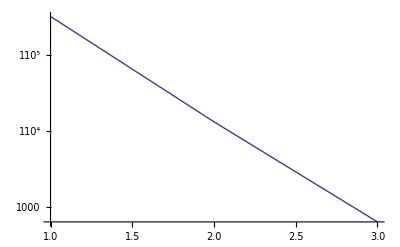

```mathematica
ListLogPlot[{Length[stable3], Length[stable5], Length[stable7]}, Joined->True]
```

```mathematica
Length[stable5]
```

13224

```mathematica
ListLogPlot[stable3]
```

-Graphics-

```mathematica
CloseStreams[]
```

Closing d:\triangle\DataSrc\3\5\7\Solutions.txt

```mathematica
stable35Five=Module[
{f, i,total=0,values, val, lastGood=0,name=FileNameForTuple[{3,5}], chunkLenght=1000,d1,d2,d3, result={}},
f= OpenRead[name];
values = ReadList[f, Expression, chunkLenght];
Monitor[
While[Length[values] ==chunkLenght,
For[i=1, i≤ Length[values],i++,
val = values[[i]];
d1=DigitCount[val,5,0];
d2=DigitCount[val,5,1];
If[d1!=d2, Continue[]];
d3=DigitCount[val,5,2];
If[d1≠d3, Continue[]];
(*
d1=DigitCount[val,7,0];
d2=DigitCount[val,7,1];
If[d1!=d2, Continue[]];
d3=DigitCount[val,7,2];
If[d1≠d3, Continue[]];
d2=DigitCount[val,7,3];
If[d1≠d2, Continue[]];*)
AppendTo[result,val];
lastGood=val;
];
total += Length[values];
values = ReadList[f, Expression, chunkLenght];
],
{total +i, Length[result]}
];
Close[f];
result
]
```

{27,3162,3186,6886,7626,7650,551377,553401,553405,554401,787657,787681,788157,788161,788301,788305,788401,797157,797161,49628412,49629676,58990932,58990936,59016312,59016936,59017176,59017180,62896932,62896936,13966803927,13966829631,13966985631,13966987555,13966987627,13966987635,15159003151,15159003255,946095898302,946143551506,946143553926,946144616562,946144695306,946145335662,946602363762,946602375682,946602381402,946602381430,946602381882,946602381910,946602382126,946602382150,946604303802,946604382502,946604382510,946604487502,946604487510,946640645262,946640647182,946640648182,946640704062,946641054630,946641172062,946641172810,946641178810,946641179502,946641209430,946641209502,946642751262,946642751310,946642766302,946642767130,946642773126,946645312782,946645312806,946645422130,946645422150,946645428126,946645428150,946654797010,946654800250,946654875750,946654878150,946654878250,952414220262,953486490802,953486490810,953487193810,953490251262,953490265762,953490266302,953490272050,953490272130,953490273130,953490428130,953614256310,976816960662,976816960686,976816960902,976816960930,976816970302,976816989010,976818397762,976818398410,976818398430,976821172762,976821179382,976821179386,976821179410,976821179626,976830548410,976830548430,976830563802,976830628186,976830629410,976830629430,976859484682,976859485662,976859485686,976859772186,976859773402,976859798310,976859798430,976865813802,976866209626,976866209650,976866210630,976875191886,976875191902,976875191910,976875428182,976875428802,976875891502,976875891510,976875894010,976875898126,976875898150,976875959386,976875959550,976875960010,976875960250,976875972502,976875972510,976875972750,976875973150,976878909562,976878922762,976878923382,976878923386,976878923410,976878929550,976878989002,976878990802,976878990810,976879082550,976879100650,977851676550,977851678386,977851678410,977851679382,977851679386,977854297062,977854334382,977854334386,977854334410,977855876302,977855890662,977855890882,977855891302,977855891310,977855895010,977855937562,977856250186,977856250306,977856251410,977856251430,977856282126,977856282130,977856406930,977856407002,977856407010,977856407526,977856407650,977856409630,977892616926,977892616930,977893131510,977893131550,977894554626,977894554630,977894566302,977894566510,977894690926,977894723250,978027898186,978037506562,978037532562,978037532802,978037976550,978038054550,978038064010,978041173186,978041173302,983273438262,983273443930,983273444650,983273459430,983273459502,983273990626,983275395006,983275413150,983275563126,983275563150,984493062550,984494531262,984494531502,1129737285126,1129737285130,1129739078782,1130880938926,1130880941262,1130880941302,1130881020006,1130881020030,1130928296886,1130928297130,1130930546886,1130930568750,1141359954030,1141359954526,1141361725906,1141362281406,1141474691286,1141474706410,1141474710006,1141475472030,1141477048126,1141477053250,1141857500662,1141857501402,1141857501426,1141857501430,1141857507150,1141857579406,1141857584506,1141857584526,1141857912502,1141857912550,1141859453926,1141859456526,1141859468910,1141859534526,1141859534530,1141905157506,1141905160750,1141905173130,1141916515650,1143799235182,1143799391430,1143799406406,1143800803282,1143800803902,1143800803926,1143800803930,1143800860306,1143800863302,1143800881902,1143800881930,1143800882010,1143801332506,1143801359406,1143801359506,1143808772626,1143809547526,1143810550882,1143810550902,1143810551386,1143810553882,1143810563782,1143810564006,1143810564030,1143810566262,1143810566302,1143810566910,1143810625810,1143810631882,1143810631902,1143810632530,1143810957502,1143810959626,1143852063130,1143852438250,1143858203902,1143858203910,1143858218806,1143858223126,1143858225126,1143858225150,1143858282150,1144052766306,1144052769630,1144052907526,1144052909626,1144053297750,1144055085750,1144057515750,1144111722510,1144111722750,1144111753126,1144111753750,1144111893750,99227299704057,99227299704061,99227314644537,99227317222161,99227317222677,99227317273285,99227317300677,99227318834557,99227318866905,99227319223305,99227319240801,99227319241257,99227319241261,99227319241285,99227319241501,99227346504637,99227346522157,99227346523381,99227348064057,99227355503437,99227355506437,99227355896937,99227355897177,99227357445261,99227357454061,99227357610057,99227357610061,99227357610301,99258310735281,99258310740781,99258311410057,99258311410257,99258311410785,99258311413161,99258312532161,99258312535177,99258312535185,99258312985677,99258313000177,99258313000257,99258313000261,99258313000285,99258313004625,99258313006525,99258313063377,99258313065885,99258349709557,99258350553901,99258350562657,99258350562661,99258353925285,99258353926257,99258353928181,99258353928261,99258353984557,99258353985037,99258353985061,99258353985277,99258353985285,99258353987557,99258354312681,99258420703881,99258420706281,99258420706381,99258422284405,99258422285125,99258422359401,99258422359405,99520316954037,99520316954661,99520316960277,99520317192061,99520317192181,99520322445261,99520332051537,99520332897181,99520332897637,99520332897757,99520336094557,99520336094661,99520336125657,99520336125661,99520336125757,99520336125901,99520336797057,99520336797061,99520336801525,99520361820261,99520375038301,99520375100185,99520375100257,99520375943881,99520375943901,99520380969681,99520381267057,99520381422157,99520381422181,99520381422801,99520381422805,99520381425061,99520381425261,99520381438381,99520381442001,99520381442025,99524463787801,99524463788137,99524463788785,99524463829681,99524463834537,99524463847177,99524463847185,99524465391937,99524465428377,99524465625937,99524511801561,99524511835057,99524512132177,99524512189057,99524512195137,99524512195185,99551330256385,99551330256925,99551330257125,99551330265681,99551330475057,99551330475061,99551330475177,99551330475637,99551330475877,99551330501301,99551330501305,99551330501385,99551332069381,99551332069501,99551367991381,99551368050661,99551369563401,99551369563905,99551369566261,99551369566305,99551369625057,99551369625061,99551369625277,99551369625285,99551369625301,99551369631925,99551369641881,99551369641905,99554687613937,99554711350177,99554711350185,99554711443761,99554711500305,99554711501277,99554711503185,99554711797785,99554711804505,99554797423137,99554797423377,99554799688885,99555959797137,99555959797185,99555959798425,99555961751425,99555979304425,99555980584377,99555980897125,99556008000637,99556008000877,99556008000885,99556008006385,99556008007125,99556222688877,99556223234377,99556223234385,99556223235625,99556223453185,99556223469625,99556223471877,99556261720257,99556261723425,99556261740885,99556261742125,99981797692185,99984719565685,99984719567125,99984721101285,99984721501261,99984721501425,99984721516501,99984721640661,99990531412537,99990531412561,99990531412777,99990531412785,99990531413185,99990531413425,99990578984437,99990580100185,99990580100257,99990580237561,99990580640637,100012744929037,100012744929657,100012744929681,100012745095137,100012745112637,100012745115657,100012745115661,100012745115901,100012748126557,100012748223385,100012748225061,100012748235661,100012748235777,100105580234637,100105580234685,100106742975057,100106742975061,100106743006885,100106743007125,100106743125037,100106743125061,100106743125277,100106743125285,100106743125685,100106743125925,100106743131525,100106743131877,100106743132525,100106758359685,100106758360677,100106758366885,100106758593937,100106758600177,100106758600257,100106758600285,100106758601257,100106761750177,100106761750185,100106761750257,100106761750285,100106787298257,100106787298261,100106787298305,100106787300177,100106787300277,100106787300285,100106787300925,100106787301257,100106791019037,100106791020261,100106791034437,100106791037757,100106791037761,100106791037785,100106791038757,100106791038801,100106791038805,100106791906257,100106791906261,100106801640685,100106801646885,100106801646925,100106806800277,100106806803925,100110229378185,100110229457625,100110363366937,100110363679677,100110365267157,100110365267161,100110365269437,100110365269677,100110365270185,100110365314057,100110365425677,100110373220061,100110373225677,100110373238785,100110373239025,100110373242025,100110373475061,100110373475301,100110373475305,100110375017157,100110403157185,100110403235677,100110420782785,100110420782805,100110422662785,100110422663137,100110422663757,100110422663761,100110422663785,100110422663877,100262500570305,100262502129637,100262504767161,100262504845161,100262504847537,100262504848257,100262504848261,100262549407657,100262549409661,100262549409681,100263002031937,100263002740681,100263002740761,100263002741901,100263002741905,100263008594557,100263008625661,100263046895301,100263046897677,100263046898161,100263046910761,100263046910881,100263047269437,100263047270185,100263047270277,100263047422557,100263047423257,100263047423277,100263051641277,100263051642001,100263051672625,100263059409501,100263059409505,100263059469001,100263061021881,100263061022025,100263692360881,100263692375901,100263692375905,100263692382025,100263695720061,100263695726377,100263695726385,100263695739025,100263695741257,100263695741901,100263695741905,100263695785677,100263695804625,100263696100681,100263696253777,100263696272625,100263781642185,100263782187561,100263782188777,100263782188785,100263782189001,100263782189025,100263782193777,100263782193805,100263782193877,100263782193885,100263783238425,100263783238761,100263783238777,100263783238785,100263783288757,100263783289005,100263783781885,100263784000257,100263784000261,100263784006305,100263784006425,100263784006885,100263784007125,100263784017001,100263784017025,100263784020025,100263791203761,100263791210125,100263791437761,100263791440677,100263791444377,100263791444385,100263791445025,100263791800885,100263791801377,100263791801505,100263791812557,100263791813761,100263791813925,100263791818785,100263791819001,100263791819025,100263791971885,100263791972125,100263792972801,100263792975681,100263793051525,100263793053801,100263793053925,100263793054005,100263793054501,100263793531257,100263793531261,100263793531285,100263793531501,100264035159685,100264035191877,100264035195001,100264035312777,100264035312801,100264035312805,100264035313137,100264035318877,100264035318885,100264035319425,100264035329625,100264037265777,100264037265801,100264037265805,100264037281425,100264037501505,100264037516877,100264164456937,100264164457557,100264164459537,100264164470037,100264164472137,100264164476277,100264164476301,100264164476305,100264164476377,100264164476385,100264164535677,100264164537537,100264164537757,100264164863377,100264164865905,100264165001401,100264170710037,100264170710061,100264170710277,100264170710305,100264170737677,100264170737685,100264170737757,100264170738385,100264170893761,100264170893925,100264180235881,100264180235905,100264180238785,100264180472805,100264180475181,100264183610661,100264184015661,100264184015761,100264184015905,100264184141881,100264184142025,100264184172505,100264209001437,100264209098385,100264209100057,100264209100137,100264209100177,100264209157677,100264209159685,100264209176385,100264209178801,100264212892161,100264212897537,100264213703785,100264213704501,100264213704505,100264213706377,100264213756261,100264213782505,100264213784377,100264223468757,100264223469385,100264228600185,100294260553425,100294297037677,100294297037685,100294297063137,100294297065877,100294297688377,100294297688385,100294297693777,100294297693785,100294297695001,100294311328761,100294311328777,100294311328785,100294311329001,100294311329005,100294311329401,100294311329505,100294311406305,100295422657177,100295422657185,100295422813137,100295422813377,100295422813425,100295422815637,100295430547801,100295430550057,100295430550257,100295430563137,100295430563377,100295430563425,100295430628801,100295432203377,100295459772777,100295459773401,100295459797537,100295459850037,100295459850061,100295459850277,100295459956377,100295461365885,100295478548157,100295478548181,100295478548401,100295478550261,100295478551305,100295478609637,100295478909685,100295478929425,100295478990685,100295479079625,100295479100001,100295479100025,213623061445281,213623069332657,213623069332681,213624826282137,213624826335657,213624826335661,213624826359661,213624826985137,213624826988761,213624826990777,213624826990785,213624826991425,213624826991505,213624827048377,213624827063137,213624827063877,213624863710681,213624863710761,213624863710777,213624863710785,213624865272037,213624865272061,213624865272685,213624865272757,213624867735261,213624867984561,213624867984661,213624867990657,213624877350757,213624877360257,213624877360261,213624877360305,213624877831885,213624877832625,213624877843881,213624877909401,213624877909405,213625989066537,213625989069537,213625989147537,213625989148161,213625989250785,213625989253161,213625996585177,213625996585185,213625996585257,213625996585285,213625996585905,213625996594681,213625998160057,213625998160137,213625998160177,213625998160785,213625998160905,213626025801561,213626025941557,213626027535681,213626030173401,213626030191425,213626030250757,213626039562757,213626039631925,213626039640681,213626045113257,213626045113285,213653877148161,213653881412785,213653881750177,213653881750185,213653881756261,213653881756885,213653881812801,213653881813761,213653881815925,213653881828161,213653881828405,213653881828801,213653881828885,213653920031437,213653920032777,213653920032801,213653920032805,213653920079037,213653920079061,213653920098385,213653925863437,213653925864057,213653925866557,213653925879637,213653925942057,213653925942061,213653925942157,213653926585057,213653926585137,213653926585305,213653926585785,213653926645057,213653926645137,213654063053937,213654064563937,213654064570177,213654064570185,213654064570257,213654064644057,213654064648161,213654064648257,213654064648261,213654064648401,213654064648405,213654065272537,213654065350177,213654065350185,213654065350257,213654065350261,213654065350285,213654065351257,213656250563437,213656250579057,213656250579061,213656250579681,213656250585277,213656250972637,213656259954657,213656260660885,213656260663777,213656260663785,213656260663801,213656260664025,213656260720177,213656260720185,213656260735137,213656263753437,213656263845057,213656263845061,213656263845301,213656263862557,213656263862637,213656263863385,213656263865785,213656349766537,213656349766557,213656349787677,213656349788425,213656350004437,213656593757157,213656593757161,213656593770037,213656593772557,213656603519037,213656603519061,213656603519685,213656603520037,213656604319425,213656604320125,213656604328261,213656604328885,213656604379425,213656604406885,213813498990925,213813499015677,213813500110885,213813500117125,213813500782801,213813500788777,213813500788801,213813500788885,213813500819385,213814699772185,213814701194437,213814701285637,213814701344637,213814701344685,213814701345177,213814701366501,213814799610681,213814799628177,213814799628385,213814799631301,213844502378385,213844502459385,213844503985677,213844503985885,213844503992125,213844532190925,213844532193757,213844532219001,213844532219005,213844532220001,213844535162785,213844535163757,213844551647125,213845707032661,213845707038261,213845707051425,213845707206877,213845707504377,213845707521877,213845707521885,213845707531305,213845707531377,213845822375025,213845822375125,213928342347801,213928343922681,213928344163161,213928344176401,213928344628761,213928344628777,213928344628785,213928344629001,213928344629005,213928344629505,213928344632001,213928344632025,213928564554561,213928564647781,213928576751377,213928576751425,213928576753377,213928578285681,213928578288157,213928578288181,213928578522685,213928578531561,213928578550305,213928578551277,213928579000885,213928579016425,213928731348277,213928731348301,213928731350157,213928731363261,213928731363277,213928731363285,213928731422661,213928734785185,213928734785257,213928734785905,213928734788181,213928735238157,213928735266405,213929463319681,213929463394057,213929463398157,213929463398161,213929463398401,213929463753937,213929463754557,213929463754561,213929463844557,213929463844561,213929463850785,213929463850905,213929463863181,213929466882057,213929466882061,213929506267177,213929506437537,213929506437777,213929506445125,213929506721937,213929506722177,213929506735677,213929506798401,213929506800877,213929506800885,213929506801305,213929506801525,213929740632685,213929740632757,213929740812801,213929741101257,213929741101261,213929741101501,213935550969681,213935550976281,213935666829501,213935666829525,213935666831877,213935666882625,213936828907177,213936828909637,213936828914001,213936829084425,213936829093801,213936829093885,213936836878785,213936836879025,213936836882025,213936838475625,213936838672161,213936838676505,213936838678777,213936838678801,213936838679505,213936865644637,213936865662657,213936865813881,213936865815801,213936865819381,213936866110261,213936866110305,213936866115661,213936866115681,213936866116905,213936866128777,213936866128785,213936866128801,213936866187781,213936867348157,213936867350281,213936867375157,213936884788257,213936884788261,213936884788285,213936885240681,213936885266277,213936885269425,213936885318901,213936885319401,213936885319405,213936885328161,213936885328401,213936885328405,213936886835001,213936886835005,213936886894377,214399418537785,214399418773257,214399418773261,214399418773285,214399418782161,214399418782657,214399418782681,214399423913437,214399465037785,214399465037805,214399466898385,214399466907177,214399466960185,214459328675037,214459328675061,214459328675137,214459328943901,214459328944525,214459329022525,214459330095157,214459330191385,214459330250161,214459330250181,214459330547181,214459330547677,214459330626405,214459337985925,214459338000177,214459338000261,214459338007525,214459338047061,214459338047157,214459338047161,214459338063925,214459338065877,214459338687637,214459338693757,214459338706885,214459338765637,214459338765685,214459338765925,214459340346885,214459340347125,214459472675937,214459473522061,214459473522801,214459717613157,214459717613161,214459717613301,214459717613305,214459717613401,214459717613781,214459717663381,214459717673161,214459717673181,214459717690657,214459717691901,214459717692025,214459727531905,214459730890681,214459730891301,214459730897005,214459730897625,214459730969385,214459768475001,214459768475005,214459768531525,214459775414001,214459775414005,214459775422057,214459775422761,214459775422777,214459775422785,214459775551305,214459775551377,214459775553277,214459775554005,214461691437657,214461691437681,214461691438257,214461691438261,214461691441905,214461691797061,214461691798305,214461691818925,214461691819005,214461691907625,214461691910625,214461693391401,214461693391405,214461693531381,214461777360277,214461777843877,214462170093801,214462170109381,214462171878301,214462171878381,214462179797025,214462209375877,214462209375885,214462209381301,214462209382525,214462209531261,214462209531501,214462209531505,214462209532125,214462226953777,214462226953801,214462226953885,214462226959381,214692939845185,214692939845257,214692940316925,214692940318761,214692940319005,214692940319025,214692940391257,214692940391277,214692940391905,214692943519425,214692981251377,214692981251385,214692981253185,214692981428125,214692982890925,214692983360001,214692983360005,214692988316881,214692988378185,214752218834557,214752218835657,214752218835681,214752218835901,214752218860777,214752218860801,214752218862637,214752218913181,214752218913261,214752218922037,214752256647057,214752256647061,214752256647537,214752256647777,214752256750305,214752256804405,214752256804525,214752256828257,214752256831377,214752258365925,214752258750685,214752258750925,214752734865685,214752734865877,214752734922061,214752734922537,214752734928301,214752734928381,214752734928405,214752734929381,214752734943877,214752734943925,214752736485757,214752736516305,214752736516377,214752736517025,214752736519005,214752736719685,214752736720261,214752737195001,214752737195005,214752737225001,214752744687685,214752746281257,214752746281261,214752746281285,214752746285625,214752746640685,214752787503777,214752787503805,214752787503877,214752787503885,214752787504501,214752787504525,214752787535125,214752787659381,214752787659405,214752787660125,214752787672501,214752792970161,214752792975681,214752792976381,214752792976401,214752792987561,214752792988777,214752792988801,214752792988885,214752793053277,214752793054401,214752793054405,214752793860001,214754687909437,214754687910877,214754687928157,214754687928777,214754687928801,214754687928805,214754687928877,214754687928885,214754687976261,214754687976501,214754687976505,214754688440805,214754688459505,214754710938277,214754710938285,214754710938301,214754710940661,214754710957501,214754711016277,214754711016285,214754711017005,214754711019385,214754932037685,214754932038801,214754932437561,214754932437637,214754932437805,214754932457505,214754941406557,214754941484685,214754941959385,214754942193877,214754942194005,214754945312677,214754945312757,214754945312785,214754945390677,214754946250005,214754984453161,214754984453277,214754984460001,214754984473125,214754984531281,214754984531901,214754984531905,214754984532001,228896985175905,228896985241405,228896985253161,228896985253401,228896985253405,228896994628261,228896994628777,228896994641401,228896994644401,229065479457157,229065479457661,229065479488261,229065482817037,229065482817057,229065483207781,229065483210781,229065483394405,229065527442037,229065527442061,229065527457181,229095725566257,229095725566261,229095725566305,229095725566501,229095725569381,229095725569501,229095726990781,229095727128801,229095727128805,229095727456881,229095811425685,229095811425925,229095811426501,229095811491381,229095811503181,229095811503261,229095813047061,229095813079381,229095813084381,229095813282661,229095813282781,229096975485685,229096975485925,229096993000761,229096993000801,229096993000881,229096993003761,229096993003785,229096993053261,229096993053277,229096993053285,229096993054005,229096993062757,229096993079505,229096994945005,229096994945125,229096995022125,229097021582677,229097021582757,229097021582785,229097021600161,229097021600281,229097021600757,229097021600901,229097022047037,229097022047157,229097022048261,229097022065757,229097022065761,229097022065785,229097022066505,229097022068781,229097022284557,229097022285177,229097022285261,229097022285285,229097023844061,229097031285037,229097031345301,229097031641437,229097031672037,229097031672061,229097031678381,229097031798181,229097031798261,229097031815637,229097031815677,229097033206437,229097033207137,229097033226261,229097033235037,229097033235757,229097033285877,229097033390881,229097236750777,229097236751401,229097236757005,229097236829401,229097236834525,229097275550805,229097275566277,229097275566301,229097275566385,229097275782057,229097275782061,229097275782157,229097275782781,229097275788405,229097275800057,229097275800061,229097275800277,229097275800285,229097275800301,229097275801501,229097275801525,229097277376381,229097277376401,229097279797501,229097289546901,229097289547525,229187520097681,229187522285157,229187549320281,229187550894661,229187550894681,229187550897657,229187550897661,229187559069657,229187559069661,229187560645057,229187560645137,229187560645305,229187560647537,229187560719657,229187560723285,229187560723381,229187560726281,229190000038281,229190002438801,229190002453885,229190002500757,229190013769401,229190013769405,229190013769501,229190014144381,229646594219637,229646594225305,229646594226277,229646594226285,229646594297637,229646594297677,229646594297757,229646594298405,229646594300637,229646595815901,229646595815905,229646595816261,229646595878877,229646595879405,229646595893905,229647756659557,229647756660277,229647756660285,229647756660301,229647756723157,229647756725157,229647756725181,229647756725805,229647756738925,229647756739005,229647758313901,229647758319405,229647758319505,229647758612781,229647758613277,229647758613301,229647758687661,229647758691277,229647758692005,229647758694381,229647775798261,229647775815757,229647775816377,229647775875177,229647775875285,229647777737781,229647777738781,229647777766281,229647777816501,229647777816505,229647777818781,229647777819501,229647777819525,229647804863157,229647804863161,229647804863401,229647814475761,229647814475805,229647814488157,229647814644405,229651244938405,229651244940757,229651244944401,229651244944501,229651377925657,229651377925681,229651377925761,229651379018937,229651379315937,229651379320257,229651379320261,229651379335305,229651379335657,229651379381557,229651379392185,229651379490657,229651379490681,229651379490901,229651379491305,229651386819537,229651386819561,229651386832657,229651387285285,229651387285801,229651387285881,229651387288285,229651389082785,229651389085185,229651389085305,229651389085681,229651389085761,229651389142057,229651389145057,229651420413757,229651420413801,229651420472805,229651420491261,229651420785777,229651429800685,229651429801305,229651429801377,229651429803277,229651429862557,229651429862637,229651429866285,229651429879381,229651429879405,229651429882005,229651430568777,229651430568805,229651436363781,229651436422557,229651436422561,229651436422677,229651436422801,229651436440785,229657055172157,229657055188881,229657055191525,229657102428781,229657104003181,229657104003261,229657104003277,229657104003285,229657104016381,229657104016401,229657104081901,229657227535161,229657228944537,229657228944561,229657229081437,229657241110177,229657241110657,229657241110681,229657241110905,229657241116525,229657241128161,229657241128401,229657241128405,229657241175777,229657241175805,229657246601401,229657246660777,229657246660785,229657246660801,229657246678281,229657248085161,229657248222057,229657248222061,229657248222777,229657248222805,229657485238905,229657571193781,229657572753925,229657578225777,229657578225805,229657578238161,229657578238405,229657578300157,229657578303781,229657590343881,229658216894677,229658216894685,229658216895301,229658216913157,229658217365757,229658217365785,229658223237681,229658266437661,229658266437681,229658266441305,229658266441377,229658266442025,229658266500925,229658266515657,229658266515681,229658266516257,229658266516261,229658266516501,229658274235777,229658274235801,229658274235881,229658274237801,229658274238761,229658274238801,229658274297037,229658274297757,229658274406381,229658752532505,229658752769377,229658752769385,229658752769625,229658754297685,229658754298305,229658754300277,229658754300285,229658754317125,229658754376305,229658754376425,229658754719505,229658791034557,229658791035285,229658791047681,229658791407157,229658791518885,229658791563901,229658791566277,229658791567005,229658791579401,229658791584501,229658791584505,229658793000781,229713232907677,229713232907685,229713232907757,229713232913757,229713232913761,229713232913805,229713235328181,229713235328277,229713235328925,229713235332625,229713237125757,229713237125761,229713237126381,229713237126405,229713244953157,229713244953277,229713244953885,229713244953925,229713244954005,229713244959501,229713244959505,229713245078301,229713245078305,229713246488925,229713246489001,229713246489025,229713246506425,229713246506505,229713246671905,229713246672625,229713247046881,229713251985181,229713252038901,229713252038905,229713252065805,229713378992037,229713379001437,229713379019037,229713379079557,229713379407757,229713380940937,229713380970057,229713380970061,229713381020037,229713381020061,229713381020277,229713381020305,229713381022557,229713402738757,229713402750177,229713402751525,229713402756261,229713402815677,229713402815685,229713402906885,229713402907125,229714407218781,229714407222025,229714408750657,229714408757025,229714408769377,229714408991281,229714414081561,229714414084557,229714414084561,229714414148181,229714414239025,229714414241301,229714414241305,229714414242025,229714455160261,229714455160305,229714455160801,229714455163257,229714455163261,229714457128285,229714457128401,229714457131281,229719836020125,229719837969381,229719837969405,229720998143757,229721000393901,229992968862757,229992968922057,229992968922061,229992968922157,229992968923381,229992968928405,229992968941501,229992968941525,229992969632125,229995459378261,229995459378301,229995459378381,229995459391501,229995459393925,229995459459505,229995459785125,229995461031877,229995461031885,229995461329401,229995461346885,229995461346925,229995461500005,229995664922001,229995664922025,229995703128901,229995703206901,230023214940901,230023215315757,230023215317001,230023300863781,230023301565781,230023303160025,230023303160125,230023303219425,230023303220125,230023310628901,230023310957001,230023310957005,230023683672781,230023683694381,230023683694405,230023683750781,230023683753781,230023684085125,230023731331881,230023731347001,230023731347005,230023732921905,230023732984501,230023732984525,230023732985001,230023732985005,230023732987525,230023741094401,230023741096881,230024463298257,230024463303261,230024463303277,230024463303285,230024463304501,230024463315681,230024463363757,230024463363877,230024463375177,230024463375261,230024463375285,230024463381261,230024463676281,230024465250925,230024465251257,230024465266285,230024465267025,230024472691881,230024472691905,230024472750877,230024472750885,230024472753385,230024472765681,230024472765777,230024472766425,230024472770125,230024473218877,230024473459525,230024475015877,230024475015885,230024716800637,230024716812757,230024716815685,230024716815925,230024716819425,230024716875057,230024716879377,230024716881285,230024716881525,230024717209425,230024717347125,230024718750685,230024718751257,230024718751261,230024718751285,230024718751501,230024718829425,230024721484525,230024721485001,230024721485025,230024759859505,230024759862501,230024759862505,230024775862525,230024904765805,230024904768757,230024904768885,236519046991381,236519047050157,236519047063281,236519052848157,236519052850161,236519052895281,236519053210305,236519053240905,236519053241881,236519053241905,236519062925661,236519062925905,236519062984657,236519062990785,236519062991301,236519063004405,236519094162537,236519094162757,236519094300285,236519094300637,236519094640761,236519094643761,236519094643885,236519094644001,236519094644005,236519094722005,236519094722625,236519095719657,236519095719681,236519095723381,236519095723401,236519095725757,236519095725801,236519095725805,236519095784557,236519095785285,236519095876381,236519096250681,236519096491281,236519103675261,236519103676285,236519103676305,236519103678381,236519103688425,236519103690885,236519103695025,236519103907137,236519103907777,236519103907785,236519103907801,236519103913885,236519104456261,236519104456305,236519105469537,236519105469561,236519105500161,236519105860305,236519105860777,236519105860801,236519105860881,236519105875677,236519105876425,236519106031377,236520266110285,236520266116305,236520266116377,236520266117005,236520266117025,236520266129401,236520266129505,236520266175157,236520266175181,236520266175801,236520266175805,236520266188285,236520266188305,236520266488905,236520268062781,236520268144381,236520381253881,236520381253905,236520381331881,236520382906281,236523695347657,236523695397661,236523695878777,236523695878785,236523695878801,236523695878885,236523695879025,236523695879505,236523696113781,236523701722681,236523744940801,236523744942025,236523754315657,236523754315777,236523754316385,236523754316425,236523754316505,236523754328781,236523754375281,236523754394425,236676086032537,236676086047557,236676086047561,236676086047777,236676086047801,236676086048277,236676086094537,236676086113377,236676095798257,236676096656901,236676096656905,236676123938281,236676124003881,236676124003905,236676125413881,236676125550181,236676143067025,236676143069505,236676144688281,236676145015881,236676145016425,236676145018761,236676145018801,236676145082025,236676145096881,236676145097505,236676340785001,236676340785025,236676386828881,236676386828901,236676516022657,236676516206401,236676516500161,236676516500181,236676525550281,236676525553881,236676525785757,236676525785761,236676525785785,236676527360157,236676527360181,236676527831277,236676527910001,236677248473257,236677248523405,236677248532801,236677250085157,236677257913185,236677305173185,236677305238785,236677306754377,236677306754385,236677306813425,236677306813761,236677306813777,236677306813785,236677306831257,236677306831285,236677307522125,236677501984557,236677501988137,236677501988877,236677501990785,236677502047185,236677502848125,236677502850625,236677549328425,236677549640661,236677549640761,236677549641385,236677549641501,236677558675177,236677558675185,236677558675257,236677558675261,236707763695281,236707763865781,236707763866381,236707768065637,236707768067125,236707768078761,236707768078777,236707768078785,236707768084501,236707768085025,236707768125901,236707768438905,236707768440777,236707777453401,236707777453405,236707777456285,236707777456525,236707777515657,236707777515681,236707777534401,236707777534405,236707777535025,236707777535125,236707778156401,236707784003757,236707784003785,236707784004405,236707784063301,236707784066881,236707784069401,236707784082525,236707864078257,236707864078261,236707864078285,236707864079005,236707864081257,236707864081285,236707864081501,236707864081525,236707864093881,236707865312781,236707865334405,236707865390781,236709054703161,236709054704001,236709055110025,236709055112625,236709055235125,236816719160185,236816719160257,236816719160881,236816719160905,236816719219557,236816719219561,236816719220181,236816719220281,236816719315681,236816719315761,236816719315777,236816719315785,236816719316425,236816719316505,236816719328881,236816719328901,236816720726401,236816720788257,236816720788261,236816720788285,236816720813881,236816721266257,236816721503157,236816721503181,236816721503401,236816757988257,236816757988401,236816757988905,236816759784657,236816759784681,236816762188161,236816762207125,236816762207625,236816762266281,237275683988437,237275684001561,237275684067177,237275685581557,237275693397157,237275693397181,237275693397561,237275693397801,237275693397805,237275693554401,237275693554405,237275697687805,237275697688777,237275697688785,237275697816877,237275697819025,237275697820005,237275698220001,237275698220005,237275698237501,237275736422761,237275736443901,237275736443905,237275736444525,237275742969561,237275742972757,237275742972801,237275742976401,237275743048381,237275743048401,237276859881405,237276859940805,237276859941261,237276859941505,237276859941525,237276904719537,237276904722537,237276904781557,237276904785637,237276904785877,237276904785885,237276904787805,237276905082661,237276905113261,237276905238405,237276905240781,237276905250801,237276905253877,237276975410001,237276975410005,237282715022781,237282787581877,237282787581925,237282787595001,237282824250657,237282824250661,237282824251281,237282824251381,237282824303757,237282824303761,237282824303785,237282824303877,237282824329381,237282824331301,237282825018757,237282825020125,237282825031381,237282825031905,237282826568881,237282826569501,237282826569525,237283058610037,237283058610057,237283058610301,237283058615805,237283058631901,237283058675637,237283058675677,237283058688925,237283058689005,237283058690877,237283059140661,237283059140901,237283059140905,237283059141505,237283059143925,237283059147501,237283059379401,237283059379405,237283059396901,237283060938381,237283060940805,237283060941301,237283213285777,237283213285801,237283213285881,237283213438161,237283213438881,237283213444525,237283213456377,237286670007781,237286670350161,237286670485657,237286670485681,237286670485761,237286670488185,237286670488885,237286671879037,237286671957777,237286672053805,237286672054005,237286672063285,237286674615781,237286719175161,237286719175801,237286719175881,237286719175905,237286719240681,237286719241257,237286719241285,237286719241501,237286719241525,237286719253801,237286719253885,237286719707005,237286719707025,237287705175037,237287705175057,237287705175301,237287705175877,237287705178277,237287705235157,237287705241405,237287705253877,237287705254005,237287705254501,237287705254525,237287707832505,237287707834501,237287707891285,237287707891525,237287707893801,237287707893805,237287709453801,237287709488125,237287709781905,237287709847525,237287709862501,237287709862525,237287861426305,237287861428161,237287861428401,237287861428405,237287861438401,237287861440905,237287861500657,237287861500681,237287861504001,237287861504005,237287861506281,237287861506405,237287861507001,237287866031401,237287866031901,237287866031905,237335471094537,237335471094657,237335471112637,237335471112801,237335471114005,237335471173305,237335471173381,237335471178157,237335471178381,237335472754501,237335518472005,237335520006877,237335520006885,237335520007525,237335520407125,237335520425005,237335520425025,237336524238405,237336524240781,237336524253901,237336524312781,237336524318781,237336524319501,237336524319505,237336547268881,237336547282005,237336547347625,237336680475657,237336680475661,237336680475757,237336680501281,237336680503381,237336680554381,237336680554501,237336680563137,237336682070001,237336682609525,237336682610001,237336682610025,237336690237781,237336690238257,237336690238285,237336691813137,237336691813177,237336691818757,237336691818925,237336691819005,237336691819377,237336691831885,237336691832505,237336691890925,237336692188257,237336692188261,237336692188285,237336692343781,237336692344501,237336692344525,237348945787501,237350107891425,237350107891525,237350207421901,237350207422525,237617431723425,237617431800057,237617431800061,237617431800277,237617431800301,237617431801425,237617441485677,237617442375625,237617445735625,237617446253125,237617531640877,237617534000001,237617534000025,237617777343781,237617777422525,237617777750625,237617785328125,237618722656305,237618722656525,237618722657125,237618948125125,237622080235161,237622080473301,237622080473401,237622080490785,237622080490905,237622080944505,237622080953305,237622082032657,237622082035657,237622082065681,237622082065761,237622082065777,237622082065785,237622082066425,237622082066505,237622082422161,237622082428801,237622082441925,237622082600025,237622089863161,237622090393881,237622090394505,237622091953905,237622092191505,237622092192001,237622167988285,237622167988401,237622167991281,237622168516401,237622168516405,237622168535125,237622177751401,237622177754001,237622177754005,237622178203761,237622178203785,237622178204001,237622178204005,237622178206305,237622178285001,237622178285005,237622421953777,237622421954505,237622421971885,237622421972125,237622422031281,237622568363181,237622568829025,237622570422525,237622570469505,237622607984505,237622611328281,237622611328905,237622611406905,237622611407025,237622611737505,237648938281905,237648938378125,237652638692005,237652639156261,237652639156377,237652639157505,237652639175001,237652639221901,237652639234381,237652639235001,237652639235005,237652658297001,237652658297005,237652697675125,237652832128161,237652832128257,237652832128261,237652832128401,237652832128405,237653858282005,237653858282025,237653858300625,237653859875625,237653859937501,16708532971679560,16708533057598312,16708533059173432,16708533076367032,16708533076367056,16708533078304552,16708533078304560,16708533078538812,16708533078553812,16708533078554632,16708535257991412,16708535268367032,16708535268367036,16708535268445036,16708535268550056,16708535273941912,16708535273941932,16708535273943936,16708535401285812,16708535402523412,16708535402523436,16708535424629632,16708535424688932,16708535424688936,16708535424694036,16708535424785880,16708535424788152,16708535424788160,16708541857898152,16708541858235756,16708541858241256,16708541858298180,16708541858301252,16708541858313400,16708541858318776,16708541859472512,16708541859472752,16708541859475032,16708541859475056,16708541859475680,16708541859475752,16708541859534556,16708541859538156,16708541859551280,16708541859553756,16708541859553780,16708541859847552,16708563291976312,16708563291976552,16708563291976560,16708563291985312,16708563334848312,16708564458007012,16708566260647512,16708566260648260,16708566262268812,16708566262534680,16708566262535652,16708566262600252,16708566262600260,16708566262601260,16708566262615680,16710236819329032,16710236819329036,16710236819329656,16710236819331436,16710236819331912,16710236819335756,16710236865645312,16710236867226412,16710236867226432,16710236867751312,16710236867751552,16710236867769052,16710236867769060,16710236934004512,16710236934022036,16710236934022756,16710236934147156,16710236934475276,16710236937925632,16710236937925636,16710236937925660,16710236937925876,16710236937926280,16710236937926400,16710238096265812,16710238096273260,16710238096273300,16710238096273380,16710238096285680,16710238099629660,16710238099631532,16710238099631556,16710238099632532,16710238100004052,16710238100110752,16710238100110800,16710238100163780,16710238100187756,16710238109491276,16710238137660132,16710238137660160,16710238137678876,16710238137678880,16710238139457036,16710238144566432,16710238144566436,16710238144631556,16710238144632052,16710238144644436,16710238144644636,16710238144645176,16710238154394036,16710238154395056,16710238154397036,16710238156797756,16710238157034532,16710238157034556,16710238157047156,16710238157047680,16710238157053756,16710238158628276,16710238159000156,16710267842203932,16710267842203936,16710267842282676,16710267842285052,16710267842285752,16710267932426376,16710267932426380,16710267932443876,16710267941953276,16710269093769636,16710269093770032,16710269093770036,16710269093770276,16710269094629500,16710269104376256,16710269150487676,16710269150487756,16710269150487780,16710269152737636,16710269152738176,16710269152738180,16710269152750752,16710269152812556,16710269152812780,16710269152816900,16710272465032056,16710272465035132,16710272465035152,16710272465644432,16710272465644660,16710272465645056,16710272465645136,16710272465645160,16710272465735056,16710272465741280,16710272465741400,16710272465800680,16710272465815756,16710272509866312,16710272509866552,16710272510265936,16710272580081532,16710272580081556,16710272580082132,16710272580547152,16710272580551500,16710272580554500,16710272580584376,16710272580584380,16710272582126376,16710272582126400,16710272582129380,16710272582129400,16883920168378312,16883920168397532,16883920168397536,16883920168398156,16883920168456312,16883920168456512,16883920168753932,16883920168753936,16883920168910032,16883920170038280,16883920170329032,16883920170332676,16883920170332680,16883920170335136,16883920170348256,16883920170393912,16883920170394032,16883920170394680,16883920170407152,16883920170407776,16883920177766532,16883920177766536,16883920177769560,16883920177845132,16883920177845276,16883920177847560,16883920177848180,16883920177848300,16883920178297760,16883920178304376,16883920178304400,16883920178553880,16883920180078932,16883920180079032,16883920180097752,16883920180098400,16883920180156932,16883920180156936,16883920180157652,16883920180157680,16883920263862656,16883920264457056,16883920264470156,16883920264473156,16883920265710176,16883920265710180,16883920265710756,16883920265710780,16883920265718936,16883920265719032,16883920265719036,16883920265719680,16883920266047056,16883920266051376,16883920266172156,16883923607922780,16883923607925132,16883923607925160,16883923607925652,16883923655162632,16883923655188152,16883923655188180,16883923655188252,16883923655188260,16883923655188876,16883923655188900,16883923655241400,16883923655250136,16883923656645036,16883923656647632,16883923656660760,16883923656815632,16883923656816252,16883923657113756,16883923657131256,16883923657131280,16883924814648156,16883924814847812,16883924814851536,16883924817265912,16883924817265932,16883924817272800,16883924817273300,16883924818843812,16883924818860252,16883924818866876,16883924818866880,16883924818906432,16883924818906912,16883924818907136,16883924818907152,16883924818907160,16883924818909432,16883924818928376,16883924818928752,16883924818928760,16883924827048380,16883924827051300,16883924827068876,16883924828610636,16883924828610880,16883924828612800,16883924828938276,16883924829000132,16883924829000160,16883924829004380,16883924829018876,16883924829018880,16883924905113400,16883924905173132,16883924905173136,16883924905173180,16883924905173376,16883924905190632,16883924905190676,16883924912906412,16883924912906436,16883924912913132,16883924912913136,16883924912913160,16883924912913252,16883924912925636,16883924912928280,16883924912973400,16883924912984412,16883924912985060,16883924912991252,16883924912991876,16883924912991900,16883924914568800,16883924915031376,16883924915031400,16883924915034400,16883925158610676,16883925158610760,16883925158628180,16883925158628252,16883925158984656,16883925159140776,16884015430660276,16884015432195132,16884015432195136,16884015432195160,16884015432210876,16884015432445180,16884015432453936,16884015440344552,16884015440344632,16884015440344636,16884015440344660,16884015440398276,16884015440422636,16884015441954012,16884015441954052,16884015441990636,16884015441990652,16884015441990660,16884015442344676,16884015442345036,16884015442347132,16884015442347136,16884015442351276,16884015442366900,16884015488707132,16884015488766912,16884015488766936,16884015488784432,16884015488784436,16884015488785632,16884015488785660,16884015488785876,16884015488785900,16884015490319032,16884015490319436,16884015490319680,16884017881254552,16884017881272012,16884017881659676,16884017881678876,16884017881678900,16884017884798276,16884017884847512,16884017884848252,16884017884850032,16884017884850680,16884017884850752,16884017884850760,16884017884876276,16884017894534556,16884017894553780,16884017894610280,16884017894612556,16884017922757000,16884017922765756,16884017924312776,16884017924706400,16884017929692036,16884017941909500,16884017942191380,16884017942203776,16884017942269500,16884017943453280,16884045659017056,16884045659142036,16884045659143912,16884045659143936,16884045659144632,16884045659157052,16884045659157060,16884045659157132,16884045659157780,16884045703601560,16884045707582560,16884045773828812,16884045773835636,16884045773987752,16884045773987760,16884045774303300,16884045775409436,16884045775410012,16884045775422652,16884045775422676,16884045775423156,16884045775428876,16884045775428880,16884045775547056,16884045775550136,16884045775550160,16884045775875052,16884045775875060,16884045775940752,16884045775940880,16884045775953760,16884045775954000,16884046984568800,16884046994141512,16884046994142160,16884046994176260,16884046994176300,16884046995001500,16884046995079500,16884216669960156,16884216670019032,16884216670019680,16884216674253256,16884216674625756,16884216674625780,16884216899000776,16884216904332036,16884216904393912,16884216904393936,16884216905250756,16884217793472132,16884217793475136,16884217793769652,16884217793770276,16884217793782656,16884217793829556,16884217793847052,16884217793847060,16884217793847132,16884217793847136,16884217793847160,16884217795000932,16884217795000936,16884217795001556,16884217795003812,16884217795007632,16884217795079556,16884217795079656,16884217795082556,16884217795423152,16884217795423176,16884217795423180,16884217795423260,16884217832051512,16884217832054052,16884217832110812,16884217832110912,16884217832204632,16884217832210676,16884217832210680,16884217832210760,16884217832222136,16884217836335880,16884217836828252,16884217836829380,16884217836875632,16884217836876276,16884217836876280,16884217836893800,16884217836895000,16884217845862536,16884217845862660,16884217845862776,16884217845862780,16884217846098136,16884217846100152,16884217846100160,16884217846100800,16884217846100880,16884218089859536,16884218089859556,16884218089953756,16884218090019376,16884218090334376,16885712892678312,16885712892679012,16885712893537776,16885712893538260,16885712903129632,16885712903129652,16885712903132052,16885712903132136,16885712903132160,16885712903132632,16885712903162536,16885712903162680,16885712903163160,16885712903163400,16885712903281536,16885712903288152,16885712903288176,16885712903301300,16885712903303136,16885712903303152,16885712903303160,16885712903303376,16885712903303380,16885713490407000,16885713496968756,16885713496968900,16885719306679000,16885719306679500,16885719307501300,16885719307506252,16885719307585000,16885719345782560,16885719346491252,16885719346491876,16885719346491900,16885719492972052,16885719492972060,16885719492972132,16885719492972760,16885719492991500,16885719493051252,16885719493053760,16885719494297136,16885719494298180,16885719494300052,16885719494300260,16885720463391876,16885720463391900,16885720463444400,16885720463469400,16885720468757556,16885720468782756,16885720468785052,16885720468785676,16885720468941300,16885720478519632,16885720478520036,16885720478520256,16885720478520280,16885720482515652,16885720482515676,16885720482515680,16885720482515760,16885720482581376,16885720482581380,16885720483285000,16885720508203432,16885720508204512,16885720508207800,16885720508210752,16885720508287512,16885720508288752,16885720508288800,16885720508615632,16885720508616876,16885720511753176,16885720511753260,16885720511753760,16885720511803252,16885720511803260,16885720521487512,16885720521515800,16885720527359436,16885720527359680,16885720527766500,16885720527766876,16885720527890800,16885720527890880,16885720527891876,16885720527891880,16885720527893752,16885724123069560,16885724123082636,16885724123129512,16885724123131536,16885724123141932,16885724123142012,16885724123148300,16885724141488756,16885724141506900,16885724141565756,16885724143081260,16885724143081500,16885724143140660,16885724143141876,16885724143146876,16885724143146880,16885724143159380,16885724387268880,16885724466816400,16885724467269376,16885724473125180,16885724473131876,16885724473131880,16885743710941552,16885743715017000,16885743715234632,16885743715234660,16885743715235632,16885743715235676,16885743715718760,16885743715719000,16885743715784376,16885743715784380,16885743723046912,16885743723046936,16885743723047560,16885743723204376,16885743723204400,16885743723522000,16885743724615756,16885743752375256,16885743752453260,16885743752453752,16885743752453800,16885743753988260,16885743753988300,16885743753988380,16885743753990780,16885743771500632,16885743771500652,16885743771506376,16885743771506400,16885743771566260,16885743771581500,16885743896985256,16885743896987532,16885743896987536,16885743896987776,16885743896988180,16885743896988252,16885743897359556,16885743900472156,16885743900484536,16885743900491376,16885743900491380,16885743900550156,16885744873238280,16885744875862680,16885744875863136,16885744875863380,16885744875863400,16885744875893776,16885744877437776,16885744877437780,16885744877457000,16885744877515780,16885744885251300,16885744886819376,16885744886819380,16885744933672180,16885750744537660,16885750744537776,16885750744537780,16885750744565632,16885750744615752,16885750744616500,16885750744625260,16885750744953280,16885750746190636,16885750746485656,16885750832047632,16885750832047660,16885750832048280,16885750832050800,16885750832113252,16885750832113900,16885750832126280,16885750832126400,16885750832128800,16885751074393756,16885751074394376,16885751074394400,16885751074628160,16885751074628376,16885751074628400,16885751074640776,16885751074641256,16885751074641280,16885751074643776,16885751076175800,16885751084016276,16885751084156280,16885751084157000,16885751086096876,16885751242578156,16885751242578876,16885751242578880,16885754687659536,16885754687659656,16885754687672532,16885754687672536,16885754687672776,16885754687678256,16885754687897032,16885754687897056,16885754687897676,16885754687897680,16885754687910880,16885754690315800,16885754690315880,16885754690318776,16885754690329000,16885754701734376,16885754707047156,16885754748440652,16885754748440676,16885754748440680,16885754748440752,16885754748440760,16885754748472500,16885754750093880,16885755723438156,16885755723456876,16885755723457000,16885755725031400,16885755862204500,16885755862222000,16885755863750632,16885755863751376,16885755863753160,16885755869223252,16885755869225032,16885755869225652,16885755869225680,16885755869225760,16885755869251276,16885755869301256,16885755869303776,16885755910163136,16885755910163160,16885755910163376,16885755910163380,16885755910171912,16885755910172136,16885755910172152,16885755910172160,16885755910579000,16885755910579500,16885755910704376,16906800549719412,16906800549722152,16906800549722176,16906800586351432,16906800588457512,16906800588457752,16906800588457800,16906800791815912,16906800791820132,16906800791820136,16906800791820160,16906800791990656,16906800793469052,16906800793470012,16906800793470052,16906800801585036,16906800801585276,16906800801585280,16906800801585756,16906800801644056,16906800801645136,16906800803157532,16906800803159676,16906800803160636,16906800803210676,16906800803210680,16906800803210752,16906800803210760,16906800803531436,16906800803531536,16906800803532160,16906800803534436,16906800803534676,16906800803534680,16906800803688900,16906800803691900,16906800830254632,16906800830254636,16906800830254660,16906800830257632,16906800830257660,16906800830631556,16906800832204060,16906800832209652,16906800832209676,16906800832210300,16906800832222800,16906800832225632,16906800832225636,16906800832225680,16906800832225876,16906800832459632,16906800832459636,16906800834862752,16906800834866880,16906800834928756,16906800834941880,16906800844612800,16906800844690876,16906800844691500,16906800849800652,16906800849800680,16906800850003812,16906800850004052,16906800851593912,16906800851594032,16906800851597560,16906800851598132,16906800851598136,16906800851598160,16906800851598376,16906800851600256,16906802006753256,16906802012188912,16906802013675912,16906802013832536,16906802013832780,16906802013835056,16906802013835776,16906802013835780,16906802013859536,16906802099709556,16906802099710276,16906802121485776,16906802121488376,16906802121488380,16906802121500760,16906802121656256,16906802121656280,16906802123141256,16906807910553912,16906807910662536,16906807910662776,16906807910662780,16906807910710656,16906807911017056,16906812022284556,16906812023848176,16906812023848180,16906812023848260,16906812023906532,16906812023906536,16906812024018880,16906812024378900,16906812065331276,16906812070317156,16906812070785652,16906812070785660,16906812072266412,16906812072266532,16906812072359512,16906812072360300,16906812072366880,16906812072379500,16906812072423156,16906812072423256,16906812072425176,16906812072438252,16906812080160756,16906812080160780,16906812080178276,16906812080178280,16906812084468900,16906812084471900,16906891114176556,16906891115788312,16906891185735132,16906891185737532,16906891185737536,16906891185737652,16906891185738136,16906891185738300,16906891185940932,16906891185940936,16906891230554032,16906891230582052,16906891230582060,16906891230582780,16906891232975032,16906891232975152,16906891233000636,16906891233000880,16906891233000900,16906891233001276,16906891233210780,16906891233220056,16906891233237556,16906891234766436,16906891234766536,16906891234772056,16906891234772776,16906891235160180,16906891235178880,16906891235188276,16906891459394412,16906891459395180,16906891459397652,16906891459397680,16906891459547532,16906891459547776,16906891464866532,16906891464866556,16906891464945136,16906892353989060,16906892354020300,16906892354315812,16906892354317012,16906892354334532,16906892354376412,16906892354382636,16906892392585936,16906892392756552,16906892392756560,16906892397068800,16906892397381252,16906892397381300,16906892397422800,16906892397423132,16906892397428152,16906892404881252,16906892407125060,16906892407125300,16906892407126500,16906892407190652,16906892407190676,16906892407190680,16906892407190752,16906892407190760,16906892626972812,16906892627143912,16906892627147556,16906892627147680,16906892627148256,16906892627148276,16906892648991300,16906892649331260,16906892650394032,16906892650395256,16906892650395276,16906892650406436,16906892650406532,16906892650406536,16906892650407180,16906892650506876,16906892650506900,16906892650563756,16906892650563900,16906892650859632,16906892650866300,16906892650937632,16906892650937652,16906892650940632,16906903080565932,16906903080565936,16906903080566512,16906903080568912,16906903080568932,16906903080632032,16906903080644512,16906903080644676,16906903080645132,16906903080645136,16906903080645160,16906903080647556,16906903086832176,16906903125098412,16906903125098436,16906903125117156,16906903125564036,16906903125581412,16906903125581532,16906903125804036,16906903125820156,16906903128988312,16906903128989032,16906903129006536,16906903129878256,16906903129878876,16906903129878880,16906903195422532,16906903195422556,16906903195422636,16906903195422780,16906903195737780,16906903195891276,16906905519709536,16906905519710032,16906905519722632,16906905519723156,16906905519725656,16906905519938932,16906905519942060,16906905519942180,16906905519959556,16906905519960780,16906905520319532,16906905520319556,16906905520472532,16906905520472556,16906905520472776,16906905521894412,16906905521895132,16906905521895136,16906905521895160,16906905521897032,16906905522035032,16906905522035056,16906905522035136,16906905539079556,16906905539097780,16906905539454556,16906905539550012,16906905539563132,16906905539563176,16906905539563180,16906905539565876,16906905539565880,16906905539609536,16906905539625180,16906905569312652,16906905577125660,16906905578937636,16906922609789052,16906922609959560,16906922609960260,16906922611439032,16906922611444512,16906922628941512,16906922628941560,16906922629000312,16906922629094412,16906922629094676,16906922629098300,16906922873051512,16906922873084412,16906922873085060,16906922873937760,16906922959020052,16906922959145052,16906922959176300,16906922959178260,16906922968750812,16906922968770012,16906922969568780,16906922969647000,16906922972815636,16906922972815752,16906922972818876,16906922972844400,16906922973472500,16906924121207512,16906924121209660,16906924121266552,16906924121266560,16906924121266936,16906924121281536,16906924121285880,16906924121288152,16906924121288160,16906924121288176,16906924121288400,16906924121288880,16906924123053312,16906924123054060,16906924130970252,16906924131022512,16906924131023136,16906924131023160,16906924131023376,16906924131023380,16906924131031512,16906924131829500,16906924135550260,16906924135570000,16906924135578180,16906924135578252,16906924135631260,16906924173835152,16906924173990756,16906924174000152,16906924179718912,16906924179725032,16906924179725680,16906924179725760,16906924179725800,16906924179845032,16906924179865660,16906924180256260,16906924180256500,16906924180270000,16906927494257676,16906927494257680,16906927494315936,16906927494316512,16906927494318912,16906927607454532,16906927607454556,16906927607456556,16906927607460136,16906927607532532,16906927607534560,16906927607538876,16906927607538880,16906927607987512,16906927607991876,16906927607991900,16906927608222160,16906927608223380,16906927609765936,16906934103519412,16906934103520152,16906934103520176,16906934103520180,16906934104328776,16906934104328880,16906934189535012,16906934189535052,16906934189548252,16906934189553760,16906934189612776,16906934189613132,16906934189613136,16906934189613756,16906934189613780,16906934193781276,16906934194218876,16906936389250000,16906936390641252,16906936400390656,16906936527750036,16906936527750132,16906936527750136,16906936527769500,16906936527894376,16906936528222500,16906936533209532,16906936533209536,16906936533210756,16906936534068756,16906936534068780,16906936534094376,16906936534094380,16906936572360300,16906936573047036,16906936573063300,16906936573068876,16906936573068880,16906936573125660,16906936573125900,16906936573128180,16906936576250880,16906936576256256,16907080566831412,16907080566831436,16907080566988152,16907080566988180,16907080566988876,16907080566988900,16907080567360132,16907080567360176,16907080567360180,16907080567362780,16907080567363132,16907080568397556,16907080568456512,16907080568476276,16907080568937652,16907080568937660,16907080635562536,16907080635563880,16907080638750132,16907080638753252,16907080639078152,16907080639078180,16907080639078252,16907080639078260,16907080639144000,16907080683984556,16907082833990800,16907082834172500,16907083007894632,16907083007897556,16907083007897632,16907083007907756,16907083007907780,16907083007910052,16907083007910060,16907083007910760,16907083007969556,16907083007973156,16907083008301252,16907083008301260,16907083017985300,16907083017991876,16907083018047180,16907083018053760,16907110859473132,16907110859491276,16907110859491380,16907110859550160,16907110859550180,16907110900398136,16907110900398400,16907110900413760,16907110900470300,16907110900568752,16907110900578300,16907110900943752,16907110910156532,16907110910156556,16907110910157532,16907110910163900,16907110910193780,16907110910550300,16907110910551260,16907110910568760,16907110912110276,16907110912110280,16907110912112536,16907110912112680,16907111156253880,16907111887534380,16907111933594556,16907111933598256,16907111933598280,16907111933768776,16907111934066300,16907111934067000,16907111935641876,16907111935641900,16907111935659400,16907112062659632,16907112062660676,16907112062662536,16907112062662756,16907112062662780,16907112062672752,16907112062672800,16907112062892180,16907112062898300,16907112063390900,16907112063440632,16907112063440676,16907112063440680,16907112064453932,16907112064453936,16907112064484532,16907112064484536,16907112064844436,16907112064844652,16907112064844676,16907112064844680,16907112064845136,16907112064845256,16907112064860052,16907112065015752,16907112065015760,16907112065021880,16907112065035000,16907112072287752,16907112072300252,16907112072304380,16907112072423180,16907112074609632,16907112316409436,16907112316409512,16907112316413180,16907112318362536,16907112318363876,16907112318363880,16907112318453300,16907112318454380,16907112318456252,16907112318456300,16907112402422032,16907112402423256,16907112402423276,16907112402428280,16907112402440752,16907112402500776,16907112402843880,16907112404376276,16907112404376400,16907112404378380,16907112404379400,16908491504459376,16908491504459380,16908491504460000,16908491506016260,16908491506046880,16908491506250260,16908491506725000,16908491552815876,16908491552815900,16908492697656376,16908492697734376,16908492783593776,16908492783593880,16908599972750652,16908599972751276,16908599972751376,16908599972768880,16908599973125280,16908600097691532,16908600097691536,16908600097692156,16908600098518912,16908600098522556,16908600098535636,16908600098535876,16908600098535880,16908600098538136,16908600098538756,16908600098538876,16908600098594656,16908600098597652,16908600098597680,16908600101960776,16908600101969512,16908600101970036,16908600101970160,16908600101970276,16908600101970280,16908600102422652,16908600102500656,16908600111329556,16908600111329656,16908600111332556,16908600111515776,16908600111516256,16908600111516280,16908600111804400,16908600111828300,16908600111881400,16908600117676252,16908600117676260,16908600117676500,16908600117735280,16908600146582560,16908600146582800,16908600146585052,16908600146879512,16908600146879560,16908600146897052,16908600146906532,16908600146906556,16908600147063300,16908600147063780,16908600156640812,16908600156642012,16908600160703260,16908600160703376,16908600160703380,16908600160704000,16908600160937632,16908600160938252,16908600160953400,16908601137188800,16908601144923252,16908601144926252,16908601173860280,16908601173866256,16908601173866280,16908601174690752,16908601174691260,16908601174691500,16908601174693776,16908601174693780,16908601192281280,16908601318376412,16908601318376436,16908601318379436,16908601318379560,16908601318379652,16908601318379676,16908601318379680,16908601318765932,16908601318770060,16908601318773300,16908601318785652,16908601318910760,16908601318940676,16908601323140752,16908601323141876,16908601323141900,16908601323159400,16908601323219400,16908632129003260,16908632129003752,16908632129003800,16908632129006256,16908632129019376,16908632129082000,16908632138768752,16908632138768760,16908632187516256,16908632187516280,17303468019648412,17303468019648436,17303468032188912,17303468032188936,17303468032219636,17303468032220256,17303468032222552,17303468032222560,17303468032225876,17303468617297512,17303468617297552,17303468617303132,17303468617303300,17303468617303380,17303468617303752,17303468617987552,17303468617987560,17303468618046936,17303468618053252,17303620921912800,17303622082225060,17303622084178132,17303622084407512,17303622084414000,17303622091798312,17303622091834512,17303622092188812,17303622092381260,17303622093921936,17303622093923152,17303622093923160,17303622093923176,17303622093923400,17303622168126532,17303622168126556,17303622168129060,17303622168141912,17303622168141936,17303622168142152,17303622168142180,17303622168382752,17303622168834652,17303622168834660,17303622168850012,17303622168906912,17303622168907632,17303622168913380,17303622168913876,17303622169956312,17303622169956552,17303622169959552,17303622177766932,17303622177766936,17303622177767152,17303622177767176,17303622177773376,17303622177773380,17303622177922132,17303622177922176,17303622177928176,17303622177928180,17303622177928252,17303622177928260,17303622178282552,17303622421882060,17303622422351500,17303622423828412,17303622423985876,17303622424001500,17303622426579000,17303622426656500,17303625541906552,17303625541906560,17303626039845060,17303652396490932,17303652396490936,17303652396492060,17303652396662752,17303652396662760,17303652397273152,17303652397273176,17303652397273180,17303652403125312,17303652403126312,17303652446094036,17303652446110752,17303652446172060,17303652446172760,17303652640657512,17303652656437512,17303652656437752,17303652657068760,17303652660157752,17303652660343752,17303652688312552,17303652688443760,17303652690390676,17303652690390876,17303656127751252,17303656127812552,17305023740657512,17305023741209380,17305023779454556,17305023779472052,17305023779472060,17305023779472132,17305023779472136,17305023779472160,17305023779473132,17305023779695152,17305023779710680,17305023781250812,17305023781250932,17305023783765900,17305026175781436,17305026175782136,17305026175788376,17305026175788400,17305026181645260,17305026181646932,17305026181828132,17305026181828380,17305026181831300,17305026224612652,17305026224612680,17305026224691252,17305026224691880,17305026224691900,17305026225406380,17305026232584376,17305026232585000,17305026233203300,17305026234375180,17305026234378132,17305026234378376,17305026234772000,17305036635548160,17305036635563752,17305036641053176,17305036642687512,17305036642688752,17305036642688800,17305036693468752,17305036937656300,17305037842687632,17305037842687636,17305037842687680,17305037845720276,17305037845813152,17305037845813180,17305037845816500,17305037845819380,17305037845819500,17305037845875760,17305037845875876,17305037846173300,17305037846250256,17305037855968800,17305037861753136,17305037861753160,17305037861753376,17305037861753380,17305037861756376,17305037861756400,17305037861818752,17305037861834376,17305037861834380,17305037862116256,17305037862128176,17305037862188376,17305037862193776,17305038099688800,17305038105568752,17305038106281876,17305038187612500,17305053955269412,17305053955269436,17305053955269652,17305053955270132,17305053955272652,17305053955272676,17305053959457760,17305053959475012,17305053959475252,17305053959534412,17305053959535052,17305053959535060,17305054004097180,17305054004332560,17305054004332800,17305054004335752,17305054004335800,17305054004694412,17305054074253252,17305054074253380,17305054074328252,17305054074328260,17305054074334380,17305054074787500,17305054076569500,17305054076578252,17305054076578752,17305055238282760,17305055238289000,17305055246094012,17305055246100252,17305055275391560,17305055275547052,17305055275548180,17305055295704380,17305055295735000,17305055490241876,17305055490625060,17305055490625300,17305055492191300,17305055492219380,17305055492219400,17305055537894380,17305055537894500,17305055539456500,17305055539609500,17305065969687660,17305065969688152,17305065969693876,17305065969693880,17305065971094636,17305065971172552,17305065971173252,17305065971173260,17305065971268760,17305065971281876,17305065971281900,17305068408985056,17305068408991380,17305068409003800,17305068410579376,17305068410579380,17305068410937756,17305068410953300,17305068410953380,17305068411015760,17305068411018760,17305068411019000,17305068418391260,17305068418396876,17305068418438752,17305068466798156,17305068466968780,17305148212907152,17305148212907176,17305148213360752,17305148214846936,17305148214847012,17305148214847180,17305148214850176,17305148214850180,17305148215004400,17305148215004500,17305148215031376,17305148215031400,17305148255866300,17305148255875060,17305148255875300,17305148255895000,17305148256406500,17305148256407500,17305148262126252,17305148262659376,17305148262659400,17305151614069060,17305151614101300,17305151615656312,17305151615662800,17305151634796932,17305151634796936,17305151718757752,17305151957890876,17305151957906260,17305151957906500,17305151957971876,17305151963048136,17305151963048176,17305151963050012,17305151963050252,17305151964881260,17305151964881500,17305151972672800,17305151972673132,17305151972673136,17305151972673160,17305151972675260,17305151972765652,17305151972766876,17305151972766880,17305153125007512,17305153125007752,17305153125007800,17305158692206512,17305158692209432,17305158692209512,17305158692363800,17305158693787552,17305158693787560,17305158693906552,17305158937662760,17305160156257060,17305160156267152,17305160156267160,17305160156267176,17305160156328412,17305160156335300,17305160156444376,17305160156444380,17305160229062500,17305305175894060,17305305175897060,17305305180659380,17305305180660000,17305305420890632,17305305420891252,17305305424641252,17305305424765680,17305305424765752,17305305424768800,17305305433625260,17305305434406300,17305305440237560,17305305440238760,17305305440239000,17305305440256252,17305305521488752,17305305521490900,17305310068381432,17305310068382160,17305310068395132,17305310068395160,17305310068517056,17305310068520032,17305310068550652,17305310068550676,17305310068550680,17305310068906432,17305310068907052,17305310068907152,17305310068907160,17305310068912632,17305310068912660,17305310070500752,17305310070501376,17305310070501400,17305310070703812,17305310070704052,17305310070704512,17305310070704632,17305310073125152,17305310073125632,17305310073125800,17305310073125880,17305310073156256,17305310156257036,17305310156257156,17305310156798280,17305310168834500,17305341066797052,17305341066797800,17305341068391376,17305341068391400,17305341068515780,17305341076328400,17305341076328752,17305341078515752,17305341162659500,17305341164068756,17305341164068900,17305341164234380,17305341164234400,17364657035238312,17364657053601400,17364657053609436,17364657053688876,17364657053688880,17364657080882056,17364657080960032,17364657080960056,17364657080969532,17364657080969536,17364657082504060,17364657082534680,17364657082832136,17364657082832532,17364657082832536,17364657082832776,17364657082895280,17364657082897632,17364657082897660,17364657082910752,17364657082910760,17364657090270036,17364657090272032,17364657090272680,17364657090328812,17364657090329632,17364657090329652,17364657090335652,17364657090350800,17364657091891312,17364657092581432,17364657092582152,17364657092582160,17364657092594652,17364657092595276,17364657092601376,17364657483006876,17364657483006880,17364657483203932,17364657483210276,17364657483210280,17364657484785636,17364657484785880,17364657484798276,17364657484843932,17364657568766412,17364657568766436,17364657568770136,17364657568831536,17364657568832136,17364657569157156,17364657569160160,17364657569160180,17364657570397536,17364657570406912,17364657570406932,17364657570425652,17364657570719032,17364657570719412,17364657570719436,17364657570719512,17364657570719652,17364657570719680,17364657570721912,17364657570876256,17364657570879376,17364660648866532,17364660648866536,17364660649004560,17364660649004632,17364660649332652,17364660649332660,17364660649391412,17364660655257180,17364660655257652,17364660655257676,17364660655257756,17364660664939032,17364660664942012,17364660668468932,17364660668469552,17364660668469660,17364660668523256,17364660668523280,17364660668547556,17364660668547636,17364660668547660,17364660668548156,17364660668550256,17364660694235812,17364660694235932,17364660698222752,17364660698225152,17364660698225632,17364660698225880,17364660707850132,17364660707850160,17364660707850652,17364660707973180,17364660707985760,17364660707987752,17364660707987760,17364660707988760,17364660713289036,17364660713366512,17364660908673432,17364660908694012,17364660908695300,17364660912579412,17364660912600012,17364660912656932,17364660951956512,17364660951959436,17364660951976300,17364660951985060,17364660951985680,17364660951985752,17364660957054432,17364660957054436,17364660957063912,17364660957114052,17364660957114060,17364660957219036,17364661869223432,17364661869226432,17364661870078912,17364661870079532,17364661870079556,17364661870110256,17364661875551512,17364662114063436,17364662114067180,17364662114069056,17364662114178376,17364662114220036,17364662114220256,17364662114220280,17364662114225032,17364662114237752,17364662119298412,17364662119538812,17364662129100276,17364662129100280,17364662129101276,17364662131756260,17364662131757500,17364662133319000,17364662133359412,17364662133359436,17364662133672160,17364662133672180,17364723410937636,17364723410940636,17364723410940760,17364723410940876,17364723410940880,17364723412522000,17364723412534380,17364723412578132,17364723412594000,17364723412600000,17364723458984560,17364723458984652,17364723460941252,17364723460941900,17364723460953160,17364723460954380,17364724463703276,17364724463703280,17364724463781280,17364724463782000,17364724464844432,17364724464844512,17364724464845136,17364724464845152,17364724464845160,17364724464847152,17364724464847176,17364724464847180,17364724464850752,17364724464945000,17364724621095132,17364724621095136,17364724621095180,17364724621188760,17364724621195000,17364724621265800,17364724621570000,17366027900879052,17366027900879412,17366027900897532,17366027900897556,17366027900897632,17366027905188256,17366027905188280,17366029063316532,17366029063316536,17366029063381912,17366029063381936,17366029063382152,17366029063395276,17366029066506432,17366029066506556,17366029066507132,17366029066507152,17366029066585056,17366029066585152,17366029066585776,17366030830956376,17366030830956880,17366030832503260,17366030869160776,17366030869172656,17366030869237536,17366030869238136,17366030869238380,17366030869532656,17366030869535056,17366030869535776,17366030869690756,17366030869703880,17366030869706280,17366030869706400,17366030871110176,17366030871188176,17366030871188376,17366041330098132,17366041330098160,17366041330115656,17366041330116376,17366041846094536,17366041846094556,17366041846125156,17366041846488276,17366041846488280,17366041847660176,17366041847660256,17366041847741376,17366041867206376,17366042492206536,17366042492300632,17366042492301276,17366042492301280,17366042492301376,17366042492366256,17366042578222056,17366042578300776,17366042578300780,17366042592268876,17366042971487656,17366042971488276,17366042971488280,17366042971500780,17366042971566280,17366042971566400,17366042981250156,17366043027347776,17366043027350656,17366043027360780,17366043027363300,17366043027363780,17366043027815676,17366043027815680,17366043027815760,17366043029410000,17366043029469376,17366043029469400,17366058850079412,17366058851672776,17366058851675176,17366058851675652,17366058851675680,17366058851725156,17366058851734656,17366058897351400,17366058897359412,17366058897359436,17366058897360060,17366058897379500,17366058897438180,17366058897438880,17366058897438900,17366058898829560,17366058899006260,17366058899301252,17366058899319000,17366058899378752,17366058906801376,17366058908360032,17366058908360056,17366058908360776,17366058908598160,17366058909062532,17366058909062536,17366058909062776,17366058909069376,17366059883003160,17366059883234632,17366059883235636,17366059883241300,17366059883242000,17366059884787752,17366059884796912,17366059887503760,17366059932066300,17366059932068880,17366059932125052,17366059932125260,17366059932147000,17366059932422536,17366059932422556,17366059932423256,17366059932440680,17366059932440752,17366059932440760,17366059932500056,17366059932506280,17366059932506400,17366060059456536,17366060059457536,17366060061094680,17366060061097060,17366060061097132,17366060061097752,17366060061110260,17366060061110632,17366060061110880,17366060061116500,17366060069237560,17366060069237800,17366060070781552,17366060070859636,17366070859379632,17366070859381912,17366070859381936,17366070859407180,17366070859457512,17366070859457752,17366070859459660,17366070859460632,17366070859563132,17366070859563136,17366070859563180,17366070859563376,17366070860172552,17366070860173300,17366070860173380,17366070860175052,17366070860175060,17366070873906900,17366070902425632,17366070902425636,17366070902425660,17366070902426380,17366070903140776,17366070903141376,17366070908988900,17366070909006400,17366070909006876,17366070909006900,17366070909065880,17366070918375180,17366070918375256,17366070918375280,17366070918375900,17366070918378180,17366070922268880,17366070922346880,17366073057066880,17366073070784376,17366073070784400,17366073097828900,17366073098047536,17366073098066500,17366073100015656,17366073117203280,17366073117656256,17366073242972556,17366073242973276,17366073243068776,17366073243078276,17366073243078280,17366073246100156,17366341553288256,17366341553301376,17366341601644032,17366341601645056,17366341601663776,17366345215331536,17366345215345156,17366407529378176,17366407529378260,17366407529378760,17366407530175000,17366407533282000,17366407958988156,17366408691878776,17395211739171880,17395211739172500,17395211767688136,17395211767688176,17395211767688380,17395211768362632,17395211768362636,17395211768362660,17395211769938752,17395211769938760,17395211789062660,17395211789068900,17395211789146900,17395215342303132,17395215342303136,17395215342303376,17395215342343932,17395215342657652,17395215342659676,17395215342659680,17395215345819400,17395215345878152,17395215345878160,17395215345878376,17395215345878400,17395215345881280,17395215345881400,17395215355473256,17395215355563132,17395215355563160,17395215355581876,17395215355581880,17395215355628776,17395215383610676,17395215383610760,17395215383750652,17395215383750680,17395215383750752,17395215383750760,17395215383751376,17395215383751400,17395215383757000,17395215385172760,17395215385172800,17395215385706400,17395215390657676,17395215390657756,17395215390659412,17395215390663780,17395215402751300,17395215403234500,17395215403281376,17395215403281400,17395215404297536,17395215404298276,17395215404457000,17395216552741536,17395216552742032,17395216552925056,17395216552925256,17395216562532556,17395216566797152,17395216566798180,17395216566803760,17395216566804000,17395246592601256,17395246592601376,17395246592610256,17395246592610276,17395246592660632,17395246592663260,17395246592687532,17395246592687556,17395246592687632,17395246594225012,17395246594553152,17395246594609660,17395246594609680,17395246594615752,17395246640785252,17395246640787780,17395246640812536,17395246641022176,17395246641047760,17395246641047800,17395246642579552,17395246642579560,17395246642579632,17395246642579636,17395246642579660,17395246642585252,17395246642585260,17395246642585900,17395246642615876,17395246642616500,17395246650412660,17395246650412776,17395246650413152,17395246650413260,17395246650548280,17395246650550276,17395246650551256,17395246655156376,17395246655156380,17395246655157000,17395247123531500,17395247123596876,17395247128906912,17395247128907152,17395247128910760,17395247128910800,17395247128910880,17395247167975776,17395247168003880,17395247168053776,17395247168053780,17395247168063176,17395247168515656,17395247171878776,17395247171878780,17395247171893900,17395247171953876,17395247802754656,17395247803132036,17395247803226376,17395247803226400,17395247803285180,17395247804706912,17395247804709556,17395247804722032,17395247804722056,17395247804722680,17395247804844532,17395247804847660,17395247812612680,17395247812612756,17395247812613376,17395247812613400,17395247812672056,17395247812672756,17395247812672776,17395247812691376,17395247812691380,17395247814469660,17395247814469680,17395247814470136,17395247814470176,17395247814470256,17395247816890660,17395247816890752,17395247816891500,17395247900485180,17395247900500156,17395247903143756,17395247903143780,17395248146891260,17395248146891500,17395248156640876,17395248158609500,17395248291109536,17395248291113260,17395248291113776,17395248291175156,17396545412617156,17396545414644532,17396576221204512,17396576221204560,17396576221675032,17396576221675036,17396576221675680,17396576225034652,17396576225093812,17396576225094052,17396576225095260,17396576225100252,17396576225115652,17396576234491260,17396576234491500,17396576240269636,17396576240334412,17396576240334436,17396576240335012,17396576240347560,17396576240348136,17396576240348260,17396576240348376,17396576240348380,17396576240800252,17396576241038380,17396576279319636,17396576281800012,17396576283315636,17396576283316252,17396576283316260,17396576283375136,17396857922271912,17396857922273136,17396857922273380,17396857922273400,17396857922304000,17396857922687532,17396857922687536,17396857923906936,17396857923907060,17396857923907152,17396857923907176,17396857923907180,17396857923907636,17396857923926500,17396857924219560,17396857924222512,17396857924222752,17396857924222800,17396857924253176,17396857924390876,17396857924390900,17396857931662660,17396857931662756,17396857931719032,17396857931719036,17396857931719512,17396857931722060,17396857931813176,17396857931819500,17396857931831380,17396857931831400,17396857932187536,17396857932187636,17396857932187780,17396857932191500,17396857932423276,17396857933768756,17396858008220152,17396858008220160,17396858008222552,17396858008222560,17396858008240776,17396858008240780,17396858008360036,17396858008360776,17396858008753776,17396858008753780,17396858009781912,17396858009941300,17396858009953156,17396858010313252,17396858010313756,17396858010316252,17396858010550032,17396858010550036,17396858010550176,17396858010550180,17396858010550276,17396858017734556,17396858017753176,17396858017971912,17396858017972152,17396858017985752,17396858017985760,17396858017991880,17396858018444376,17396858019938752,17396858019938800,17396859180172132,17396859180173160,17396859180175060,17396859180175300,17396859180187660,17396859180187776,17396859180188152,17396859180188260,17396859180191880,17396859180250876,17396859180253132,17396859180253752,17396859180547056,17396859180548280,17396859180581400,17396859181644036,17396859181645036,17396859181662532,17396859181663756,17396859181828756,17396859182140660,17396859182193876,17396859182193900,17396859228535756,17396859228535776,17396859228594556,17396859228612780,17396917969238760,17396917969240632,17396917969240876,17396917969253752,17396917969253800,17396917969297536,17396917969297780,17396917969312776,17396917969313776,17396917969612636,17396917969613152,17396917982426376,17396917982426380,17396917982596876,17396917988390776,17396920264081900,17396920656266400,24318878246992036,24318881155194652,24318881155195276,24318881155254432,24318881155254636,24318881155254676,24318881155256536,24318881155273276,24318881156815912,24318881157222156,24318881157222652,24318881174235312,24318881174329660,24318881174329680,24318881174335252,24318881174335900,24318881174392060,24318881174392132,24318881174395260,24318881174395300,24318881174407680,24318881174412676,24318881174412756,24318881174413900,24318881174703312,24318881174703412,24318881176281912,24318881176282680,24318881176335132,24318881176335160,24318881176360656,24318881176362780,24318881203616932,24318881203617012,24318881203617180,24318881205176556,24318881213006532,24318891616101412,24318891660720312,24318891660742132,24318891660742176,24318891664882176,24318891665031532,24318891665031556,24318891665038180,24318891672766312,24318891672766552,24318891672828436,24318891672832560,24318891672832800,24318891672845032,24318891672847176,24318891672848136,24318891674382532,24318891674616432,24318891674616532,24318891674625936,24318892138866556,24318892138867032,24318892138867056,24318892139098312,24318892148610312,24318892152922152,24318892152922176,24318892152922180,24318892152922800,24318892152923152,24318892152923160,24318892153209412,24318892153210752,24318892189563312,24318892189563912,24318892189569636,24318892189867060,24318892189867152,24318892189867176,24318892189867180,24318892189879060,24318892189937812,24318892190037676,24318892190037756,24318892827144532,24318892836801432,24318892836801436,24318892836818932,24318892836819652,24318892836819660,24318892836819676,24318892922738412,24318893166832776,24318893166892060,24318893166892176,24318893166909552,24318893166909636,24318893166909660,24318893185975660,24318893185975900,24318893186017132,24318893186037552,24318893186332060,24318893186332176,24318893186487660,24318893186488152,24318893186488180,24318893186515776,24318893314926532,24318893314945152,24318893314945180,24318893315004556,24318893315007156,24318909240798312,24318909240815812,24318909240816936,24318909240817176,24318909240817180,24318909241204032,24318909241204036,24318909242757136,24318909242757532,24318909242757652,24318909242766532,24318910226679436,24318910226679636,24318910227504676,24318910227507012,24318910227507052,24318910227507132,24318910227517012,24318910227517060,24318910227520012,24318910227520252,24318910254800812,24318910254864036,24318910254866412,24318910256726556,24318910256814036,24318910273939056,24318910273991536,24318910274331936,24318910274332152,24318910274332176,24318910274332180,24318910274332636,24318910275504412,24318910275506436,24318910275507136,24318910275585132,24318910275585160,24318910275585780,24318910275867180,24318910405176556,24318910405178932,24318910405254556,24318921193864012,24318921193864060,24318921203554680,24318921205178812,24318921205179552,24318921252506436,24318921252506556,24318921252772632,24318921252773280,24318921252851256,24318921252851280,24318923390819532,24318923390819536,24318923400410932,24318923400413932,24318923400568936,24318923400582052,24318923400582060,24318923403160036,24318923403160776,24318923403221932,24318923403222012,24318923403225676,24318923403238776,24318923403238780,24318923441504656,24318923447691432,24318923447691436,24319003237191532,24319003237192036,24319006693847812,24319006700178936,24319006858004032,24319006858004556,24319007884800936,24319007885334676,24319013782142056,24319013782145176,24319013782203912,24319013782203936,24319013782207636,24319013782210056,24319014174413280,24319014174722532,24319014174722556,24319014174788256,24319014228613936,24319014228926436,24319014228992056,24319014229084656,24319014965722632,24319014965723280,24319014992675932,24319015207532632,24319015207535260,24319015207906536,24319015207907052,24319015207909552,24319015207909560,24319015209081432,24319015209081436,24319015209475132,24319015209475176,24319015246113912,24319015246269432,24319015246269436,24319015246282656,24319015395488280,24320587404866536,24320587414569412,24320587414569436,24320587414570176,24320587414629052,24320587414629060,24320587414631412,24320587500488412,24320587504785132,24320587756800756,24320587758222036,24320587758235156,24320587758300036,24320587758300280,24326507914941312,24326507914943932,24326507914960756,24326507914960780,24326507915020056,24326507915022636,24326507915022676,24326507915022756,24326507920100932,24326507929882656,24326507934079680,24326507934101376,24326507934101380,24326507934160680,24326507934456412,24326507934456436,24326508106348312,24326508108394512,24326513731051312,24326513731053432,24326513731053436,24326513731054012,24326513731414056,24326513731444636,24326513733238812,24326513740428912,24326513740663932,24326513741039032,24326513741129412,24326513741129436,24326513741129512,24326513741129652,24326513741129680,24326513741131912,24326513741194552,24326513741194560,24326513741194632,24326513741194636,24326513741195256,24326513741195280,24326513741207676,24326513741210656,24326513742270312,24326513742273312,24326513773929552,24326513773929652,24326513773929660,24326513773988436,24326513783673436,24326513783704012,24326513783709652,24326513783710300,24326513784001432,24326513784018912,24326513784018936,24326513784020152,24326513784063936,24326513784066312,24326513784067132,24326513784085752,24326513784175636,24326513784175752,24326513784176376,24326513784176400,24326513789864032,24326513789867032,24326513789867056,24326513790022056,24326514163003432,24326514170893936,24326514170894676,24326514172679512,24326514261831532,24326514262297660,24326514262534536,24326514262538256,24326514895504060,24326514895504636,24326514895507012,24326514895507060,24326514903220312,24326514903241512,24326514903242152,24326514903242160,24326514903298312,24326514903301312,24326514903301552,24326514903301560,24326514945735912,24326514946266312,24326514946266552,24326514946267012,24326514946268812,24326514946281936,24326514946282636,24326514946288152,24326514946288180,24326514946288252,24326514946288260,24326514946288876,24326514946288900,24326514952126312,24326515405096932,24326515405097752,24326515449613812,24326515449614052,24326515449616312,24326515449718812,24326515449772752,24326515449797052,24326515449797512,24326515449797752,24326515449797760,24326515450085800,24326515450095052,24326515450095060,24326515450095300,24326515453281412,24326515453281436,24326515453315752,24326515453316500,24326515453517136,24326515453520052,24326538148629036,24326538154879032,24326538154879036,24326538154879656,24326538195741556,24326538195819432,24326538195819636,24326538195819676,24326538195820132,24326538195820152,24326538196272780,24326538198129036,24326538198132036,24326538584942056,24326538693769432,24326538693769660,24326538693788280,24326539358239056,24326539358241412,24326539358241432,24326539360331536,24326539360331556,24326539360331932,24326539360332012,24326539360332052,24326539426567036,24326539426584532,24326539426585152,24326539426585180,24326539426735176,24326539426738252,24326539814569656,24326539817350780,24326539818768936,24326539818769036,24326539818770152,24326539818847012,24326539818847752,24326539818940756,24326539819300156,24326539819313256,24326539855492060,24326539855492152,24326539855492176,24326539855492180,24326539855628412,24326539856022052,24326539856022132,24326539856022136,24326539856022160,24326539856047560,24326539856047800,24326539856048376,24326539856048380,24326539857585136,24326539857585756,24326539857615756,24326539857813312,24326539857819036,24326539857820036,24326545510554556,24326545510563312,24326545510582012,24326545510737532,24326545510738260,24326545666804012,24326545666820052,24326545668360912,24326545668391560,24326545668398176,24326545668516552,24326545668517012,24326545668532552,24326545668532560,24326545668538800,24326545668925252,24326545673910312,24326546701657512,24326546701719412,24326546701985256,24326546701987660,24326546701987776,24326546701988152,24326546701988260,24326546702047552,24326546702053132,24326546702053752,24326546702066500,24326629953991536,24326629954016412,24326629954016436,24326630000582032,24326630002378912,24326630002378936,24326630002429536,24326630002438312,24326630002438932,24326632336500912,24326632336500936,24326632336501432,24326632336507176,24326632336519056,24326632336520280,24326632422382656,24326632426675780,24326632670797656,24326632678597776,24326632678597780,24326632680113280,24326632680172660,24326632680172680,24326643129304032,24326643129304036,24326643129319432,24326643129320152,24326643129320160,24326643129376536,24326643129382776,24326643129475680,24326643139067056,24326643173941432,24326643174706432,24326643174706912,24326643174707136,24326643174707152,24326643174707160,24326643183691432,24326643311129056,24326643311132032,24326643313375812,24326643313375912,24326643313379560,24326644301657056,24326644301722656,24326644346503912,24326644346504032,24326644349722536,24326644349723256,24326644349725156,24328198244707012,24328198244709532,24328198246507156,24328198246897656,24328198361350156,24328198361350656,24328198361828880,24328199522300152,24328199522300176,24328199522300256,24328199522375752,24328199522378152,24328199522378260,24328199523440812,24328199523532752,24328199523550252,24328199523553132,24328199523553300,24328199523553380,24328199523597060,24328199523609432,24328199523609436,24328199523610260,24328199523616500,24328199523943800,24328199564865756,24328199570317032,24328199570317056,24328199571190632,24328199571190636,24328199571269376,24328199584003276,24328199584469376,24328199584469380,24328230521953276,24328230521972500,24328230531343876,24328230531344500,24328230578128156,24328230578128876,24328230578128900,24364631398845312,24364631399001312,24364631399001552,24364631399015812,24364631399020300,24364631399023180,24364631399023380,24364631640741312,24364631640741552,24364631640819636,24364631640820032,24364631640820036,24364631640820276,24364631645347132,24364631645347176,24364631645347180,24364631645428132,24364631645428260,24364631690007132,24364631690015932,24364631690250912,24364631699640912,24364631699640936,24364631699641560,24364631699641912,24364631699798376,24364631699798400,24364631700085060,24364631700085636,24364631700085800,24364631700163776,24364631700163876,24364631700172512,24364631700172552,24364631703300012,24364631703516312,24364631703516552,24364631703517012,24364631703517176,24364631703532512,24364631703538800,24364632588300912,24364632588300936,24364632588366432,24364632588379552,24364632588379560,24364632588379632,24364632588379636,24364632588379660,24364632588381532,24364632589954032,24364632589954056,24364632589960032,24364632589960036,24364632589960132,24364632589960756,24364632589960780,24364632817360756,24364632822691932,24364632822691936,24364632822694032,24364632824318812,24364632824319052,24364632824319060,24364632824328432,24364632861876412,24364632861881436,24364632861882652,24364632865734652,24364632865734660,24364632865734676,24364632865735012,24364632865740760,24364632865741300,24364632865798152,24364632865798180,24364632932047012,24364632932204500,24364632932503300,24364632932503380,24364632932516260,24364632932516880,24364632932517000,24364632932578156,24364632933625780,24364632933628156,24364636289616556,24364636289629060,24364636289629680,24364636291203912,24364636291206532,24364636291210152,24364636291210176,24364636291210180,24364636291442052,24364636291800912,24364636291814032,24364636291816312,24364636291816932,24364636291912536,24364636291913152,24364636291913160,24364636291913176,24364636291913260,24364636351972632,24364636351972636,24364636351972660,24364636352050636,24364636476676536,24364636476678936,24364636476679036,24364636476679656,24364663156257160,24364663156257652,24364663156282060,24364663156334512,24364663156335676,24364663156335900,24364663193832760,24364663195406512,24364663195470160,24364663195472752,24364663195485252,24364663195485900,24364663196113800,24364663196171932,24364663196172132,24364663196175012,24364663196179500,24364663196193760,24364663196194000,24364667285554536,24364667288051280,24364667288051400,24364667289625680,24364667289862632,24364667297656432,24364667297657152,24364667297657160,24364667297659512,24364667297663176,24364667297834500,24364667299218912,24364667299220056,24364667299220136,24364667299250676,24364667299253176,24364667299375660,24364667299376376,24364667299376380,24364667299378252,24364667299390632,24364667299390636,24364667299390660,24364667299390752,24364667299390876,24364667299784376,24364667299784400,24364667304692032,24364667304703912,24364667304703936,24364667304709536,24364667304710176,24364667304710256,24364667346203376,24364667346203380,24364667346204376,24364667347750632,24364667347750660,24364667347756380,24364667347756876,24364667347816276,24366340341891936,24366340341892012,24366340341892180,24366340341897060,24366340341909432,24366340341909436,24366340341909676,24366340341910260,24366340341912676,24366340341956412,24366340341957780,24366340341969552,24366340341975036,24366340341975276,24366340341975280,24366340341975880,24366340342600632,24366340342600636,24366340342600876,24366340342601256,24366340342601280,24366340342657632,24366340342657660,24366340342659676,24366340342678152,24366340342679500,24366340344219012,24366340351659432,24366340351988176,24366340352046936,24366340352047152,24366340352047176,24366340352047180,24366340352068776,24366340352068780,24366340352068876,24366340353601380,24366340353610632,24366340353610876,24366340356265656,24366340939846900,24366371203203300,24366371203909380,24366371337910756,24366371337910776,24366371350081252,24366372365640880,24366372383203276,24799384883617032,24799384883617156,24799384883691552,24799384883692012,24799384885266912,24799384885272552,24799384885565812,24799384885645260,24799384885647180,24799385012660932,24799385014235812,24799385034069636,24799385034069660,24799385034070132,24799385034094432,24799385034094512,24799386007988932,24799386007991532,24799386007991556,24799386008225812,24799386045723436,24799386045879432,24799386045879436,24799386045881412,24799386045891532,24799386045893932,24799386045894660,24799386045898156,24799386047350312,24799386047829436,24799386047846932,24799386047847012,24799386047847760,24799415834084652,24799415834084680,24799415834085012,24799415834085636,24799415834085652,24799415834085660,24799415834094412,24799415834563876,24799415834565876,24799415834565900,24799415834566876,24799415834800056,24799415834800152,24799415834800800,24799415840412652,24799415840422660,24799415840425036,24799415879382052,24799415879382132,24799415879382160,24799415879382556,24799415879382636,24799415879382780,24799415879395012,24799415879395252,24799415879397132,24799415879397136,24799415879456436,24799415879457136,24799415879460780,24799415883688252,24799415883688756,24799415891428156,24799415891428776,24799415891428876,24799415891487652,24799415891487660,24799415891500056,24799415891500800,24799415891503132,24799415891503152,24799415891506876,24799415893081276,24799417002844536,24799417002907156,24799417002910036,24799417002910152,24799417016032036,24799417016032156,24799417016128276,24799417041114036,24799417041191536,24799417041191556,24799417041518932,24799417041519660,24799417045720156,24799417060659556,24799420527772656,24799420676597656,24799420676722656,24799572758692056,24799572803300932,24799572875394532,24799572875395156,24799572875550756,24799572875550780,24799573255972032,24799573255972036,24799573255972536,24799573255972756,24799573255972780,24799573256422636,24799573256660776,24799573262282032,24799573301254680,24799573301256532,24799573305487660,24799573305487756,24799573305488376,24799573305488380,24799573305547032,24799573305547056,24799573305547536,24799573305547680,24799573305547776,24799573305547780,24799573305566500,24799573313300676,24799573314940680,24799573314953256,24799574035570252,24799574036047060,24799574036101276,24799574036125800,24799574036128152,24799574036128176,24799574036128180,24799574036128252,24799574036128260,24799574037129060,24799574037129552,24799574037129636,24799574037129652,24799574037129660,24799574037132012,24799574037281932,24799574037282012,24799574037282160,24799574037282636,24799574037282660,24799574037300132,24799574037300160,24799574037662532,24799574037662536,24799574037662776,24799574037663180,24799574037663252,24799574037693880,24799574037693900,24799574037897532,24799574045081556,24799574045094636,24799574045097136,24799574045100676,24799574045101276,24799574045317060,24799574045319412,24799574045320132,24799574045782776,24799574045785800,24799574045863776,24799574046907656,24799574047266532,24799574047285252,24799574047287676,24799574047287756,24799574047287780,24799574047288252,24799574047378152,24799574047378176,24799574047378180,24799574047379376,24799574047379400,24799574074304532,24799574074332636,24799574094703776,24799574094703780,24799574289067176,24799574289084660,24799574289094056,24799574289250632,24799574289250660,24799574289250800,24799574289250876,24799574289250900,24799574289251280,24799574291131380,24799574291190660,24799574291191500,24799574336894380,24799574338687776,24799574338688776,24799574338694500,24799574463378312,24799574467597032,24799574467597036,24799574475548280,24799574475550152,24799574475550180,24799574475550876,24799574475550900,24799574475563376,24799574482518936,24799574482532032,24799574482532056,24799574482535776,24799667016487656,24799667054691556,24799667054710132,24799667054768932,24799667055240756,24799667289082056,24799667289235156,24799667334472632,24799667334473280,24799713389163432,24799713389163436,24799713389632656,24799713432129012,24799713432131412,24799713432131532,24799713432207012,24799713432209532,24799713432209536,24799713432210180,24799713432210256,24801026728616436,24801026728616532,24801026728616536,24801026730551436,24801026730566512,24801026859882676,24801026859941512,24801026859943912,24801026877429012,24801026877459552,24801026879001432,24801026879003412,24801026879016532,24801026879020152,24801026879020176,24801026879020180,24801026879081412,24801026879082052,24801026879082060,24801026879082132,24801026879082136,24801026907220056,24801026907222180,24801026907225880,24801026914954660,24801026915015932,24801026915023300,24801026915035660,24801026915035900,24801027159063312,24801027159064032,24801027159064036,24801027159070036,24801027159070056,24801027159142036,24801027159144412,24801027159145152,24801027160548312,24801027160657800,24801027160718812,24801027160719052,24801027160719060,24801027160738800,24801027161031552,24801027161097132,24801027161097136,24801027161097160,24801027161098132,24801027161100132,24801027161100160,24801027892990812,24801027893062812,24801027895485180,24801027895485256,24801027895485280,24801027905097036,24801027905097156,24801027940348156,24801027949692156,24801027953597032,24801027953628756,24801027953628780,24801028078988412,24801028079007532,24801028079007556,24801028079007636,24801028079017032,24801028079017036,24801028079066436,24801028321207656,24801028322751432,24801028322751436,24801028322768932,24801028340348280,24801028341894432,24801028341894436,24801028342582656,24801028342663276,24801028422300756,24801028422360780,24801028422366276,24801028422366280,24801028422378276,24801028428144412,24801028428145152,24801028428145176,24801028428145180,24801028428206412,24801028428210276,24801028428210780,24801028428223152,24801028428223180,24801028428225276,24801028428225280,24801028428675780,24801031506664036,24801031506664056,24801031508226436,24801031508226556,24801031508379552,24801031508379636,24801031508398276,24801031508757156,24801031556757180,24801031556757532,24801031556816512,24801031556817052,24801031564554676,24801031808709412,24801031809535260,24801031809535752,24801031809547012,24801031809548136,24801031809548176,24801031809548380,24801031809553252,24801093020391412,24801093020391436,24801093020392056,24801093020392156,24801093020397636,24801093020397676,24801093020397756,24801093021970180,24801093021973252,24801093021973260,24801093021990756,24801093021990780,24801093027363312,24801093027457632,24801093027457636,24801093027516412,24801093027516432,24801093027523156,24801093027534556,24801093039562680,24801093039563136,24801093039563380,24801093039563400,24801093041097676,24801093125800132,24801093125860132,24801093125860152,24801093127375752,24801093127425052,24801093127453752,24801093127453800,24801093127740780,24801093127906276,24801094287922680,24801094288053156,24801094288053876,24801094288053900,24801094288062652,24801094288062660,24801094289459412,24801094289460060,24801094289470252,24801094289531512,24801094289531560,24801094290004380,24913800313066912,24913800313454556,24913800313472056,24913800314475912,24913800314632776,24913800315016312,24913800315251532,24913800315251536,24913800356441500,24913800361426312,24913800362288260,24913801389095032,24913801389095056,24913801389096912,24913801389097152,24913801389226276,24913801389234676,24913801389235636,24913801389235752,24913801389563776,24913801389626256,24913801389626380,24913801389629376,24913801389629380,24913801390632156,24913801390643932,24913801390800636,24913801390800676,24913801390800880,24913801391410756,24913801391413276,24913801518366412,24913801518366432,24913801533285912,24913801533288312,24913801533289032,24913801533289036,24913801534172536,24913801537301376,24913801537301380,24913801537504552,24913801537504632,24913801537504636,24913801537507756,24913801537537680,24913801537538160,24913801537538376,24913801537538400,24913801537893912,24913801537894056,24913801537894560,24913801537898256,24913801538069500,24913971055492060,24913971055492176,24913971055553412,24913971055554052,24913971055554060,24913971057062812,24913971213835260,24913971213835752,24913971213835800,24913971213844060,24913971213863752,24913971214926312,24913971214926552,24913971214959432,24913971215271936,24913971215272180,24913971215429400,24913972217616312,24913972217616552,24913972217735812,24913972217756560,24914002051253412,24914002051257052,24914002051257060,24914002051257780,24914002074616380,24914003193829660,24914003193907660,24914003193909552,24914003193910252,24914003193910260,24914003193913900,24914003197378132,24914003197381276,24914003197381380,24914003197438152,24914003197453276,24914003197456876,24914003235163752,24914003236720060,24914003236720300,24914003236757500,24914003236876300,24914003237297500,24914003242192012,24914003242192176,24914003242209660,24914093078632752,24914093080194432,24914093080194436,24914093080581552,24914093080585252,24914093080585260,24914093080585680,24914093080585900,24914093087989012,24914093088694432,24914093088694680,24914093088695160,24914093088754432,24914093088756532,24914093088756556,24914093090272156,24914093090329012,24914093090344056,24914093090347800,24914093090350132,24914093090350152,24914093090350636,24914093137581412,24914093137582636,24914093265723312,24914093265726412,24914093266585152,24914093266585180,24914093266585656,24914094240664036,24914094240735936,24914094240741312,24914094241206412,24914094241207152,24914094250398436,24914094250426560,24914094250813912,24914094250938412,24914094250939032,24914094250939056,24914094250956552,24914094252054012,24914094252054636,24914094252054660,24914094252347812,24914094252367132,24914094252531412,24914094252531436,24914094299645052,24914094299648136,24915380859554656,24915380859847812,24915380859867180,24915380859926436,24915380861442052,24915380861442060,24915380861442132,24915380861442136,24915380861500912,24915380864160252,24915380864178780,24915380873850900,24915380873862756,24915380873910636,24915380873910876,24915380873910880,24915380873923260,24915380873928132,24915380873928376,24915380878988436,24915380878988932,24915380879001532,24915380879001556,24915380908767012,24915380908768812,24915380909004660,24915380918393812,24915380918844052,24915380918844060,24915380918845060,24915380918859552,24915380918860012,24915380918860252,24915380918860260,24915380918865876,24915380918865880,24915380918925252,24915380922032652,24915380922035652,24915380922048180,24915380922048252,24915380922053136,24915380922053380,24915380922268812,24915380922272052,24915383313046912,24915383313047752,24915383313047760,24915383361360012,24915383361360252,24915383361360660,24915383361360900,24915383371110636,24915383371112760,24915383372031276,24915383372035000,24915466623444012,24915466623444052,24915466623445012,24915466623470260,24915466625115636,24915466625115880,24915466653203412,24915466653204636,24915466653210012,24915466653225052,24915466653281532,24915466653281536,24915466653281932,24915466653282012,24915466653282180,24915466653284412,24915466670801260,24915466670801500,24915466670818756,24915466672422052,24915466672422132,24915466672422160,24915466672422552,24915466672688880,24915466672690800,24915466672691880,24915466672756500,24915466672757500,24915466867222512,24915466867223260,24915466867225176,24915466867225180,24915466867281312,24915466867281552,24915466867375632,24915466914554376,24915466914554380,24915466914563152,24915466916095152,24915466916095176,24915466916095180,24915466916098176,24915466916115652,24915466916797536,24915466916798256,24915466916800132,24915466916800176,24915466916803776,24915466916819380,24915466916819400,24915466916878132,24915466916878176,24915466916878180,24915467641566880,24915467641566900,24915467641584376,24915467641593880,24915467646492156,24915467646879012,24915467646879052,24915467646881532,24915467646881536,24915467646881932,24915467646882012,24915467646882180,24915467646907536,24915467646907776,24915467646907780,24915467647062756,24915467647063776,24915467647065636,24915467647065676,24915467647065880,24915467648440812,24915467648441512,24915467648475876,24915467648594632,24915467648594676,24915467775429012,24915467775429660,24915467777751552,24915467777820052,24915467777820060,24915467787140812,24915467787298300,24915467787298380,24915467832845052,24915467833001500,24915468029459680,24915468029460652,24915468029460760,24915468029694012,24915468029720260,24915468031250932,24915468031251556,24915468031257636,24915468076756500,24915468076953412,24915468078907752,24915468086328312,24915468086407800,24915468086501260,24915468086518752,24915468086875800,24915468086881876,24915468087922800,24915468087923376,24915468087923400,24915468087925012,24915468087975052,24915468088704376,24915468088706260,24915468088706500,24915473644725300,24915473646515812,24915473646522052,24915473646522132,24915473646522160,24915473646523132,24915473899226500,24915473974689012,24915473974695252,24915473974773252,24915473985343752,24915475146522160,24915475146595060,24915475150789000,24915475195428376,24915475195469436,24915475195470136,24915475195470256,24915475195475752,24915475195475760,24915475195487752,24915475196116876,24915475196125276,24915475196178760,24915478537129432,24915478537129680,24915478537188432,24915478537188436,24915478537194552,24915478537288300,24915478537288380,24915478537660060,24915478537660800,24915478537660900,24915478537663300,24915478539235032,24915478539235036,24915478539235756,24915478539235780,24915478539237652,24915478539241380,24915478539473176,24915478539491400,24915478623222060,24915478623222180,24915478623223152,24915478623225256,24915478623438936,24915478623913152,24915478623913180,24915478623913260,24915478623937536,24915478623990780,24915478625000932,24915478625506260,24915478625506300,24915478625584380,24915478632847056,24915478632847156,24915478632847776,24915478632847780,24915478632972556,24915478633300012,24915478633379500,24915478634922756,24915478634922780,24915478634923276,24915478634953156,24915478634956380,24915478635156532,24915478635156556,24915478635159436,24915478635159552,24915498047439052,24915498047439060,24915498048985932,24915498048985936,24915498051645300,24915498295812760,24915498311500060,24915498311500300,24915498311516880,24915498393359512,24915498393359676,24915498393360900,24915499560582552,24915499584006252,24915505371895260,24915505371897132,24915505371897136,24915505371897180,24915505371954052,24915505395312660,24915505395319380,24915505395319500,24915509525971900,24915509531281936,24915509531282532,24915509531282776,24915509531360752,24915509531365636,24915509531365800,24915509541032152,24915509541032176,24915509541051256,24915509541051376,24915509541110800,24915509541110880,24915509541909400,24915509619144412,24915509619144436,24915509619144652,24915509619144660,24915509619145176,24915509619147652,24915509619147660,24915509619147676,24915509619223152,24915509619223176,24915509619223180,24915509619223252,24915509619223260,24915509619225652,24915509619225660,24915509619226380,24915509631250300,24915509631256260,24915509632813252,24915509632813900,24915509632843776,24915509632843780,24915509632969500,24915509632984500,24915651857585032,24915651857585056,24915651857585136,24915651857585776,24915651857616376,24915651857819032,24915651857819056,24915651857820036,24915651858287776,24915651858288136,24915651859393912,24915651859394032,24915651859394436,24915651859394652,24915651859394676,24915651859394680,24915651859407036,24915651859770160,24915651859859512,24915651859862752,24915651859866880,24915651859866900,24915651859881400,24915651859925136,24915651859928280,24915651859940752,24915652441813756,24915652441875876,24915652443382000,24915652443391276,24915652443443776,24915652455487500,24915656057032560,24915656057032800,24915656057062512,24915656057062752,24915656058600132,24915656058600136,24915656058600160,24915656058600636,24915656058600880,24915656058626376,24915656058626380,24915656058679380,24915656059375132,24915656059393800,24915656076203136,24915656076203152,24915656076203160,24915656076203376,24915656076203380,24915656076203800,24915656076334380,24915656078517000,24915656105548300,24915656105563800,24915656105629380,24915661869925036,24915661869925800,24915661875396912,24915661875396936,24915661875397560,24915661875423180,24915661875425052,24915661875425260,24915661884785632,24915661884787680,24915661884788376,24915661884788400,24915661884844680,24915661884846936,24915661884851256,24915661889063152,24915661889063160,24915661889063176,24915661889063260,24915661889063400,24915661889063880,24915661889065660,24915661889234500,24915661916206252,24915661916206260,24915661917973132,24915661917973380,24915661917990636,24915661917990876,24915661917990880,24915661925968800,24915661927891500,24915661927891876,24915662128922652,24915662949328132,24915662949329500,24915662951593800,24915662959066300,24915662959084500,24915662959378800,24915662959379500,24915662959381276,24915662960953752,24915662960954376,24915662960954400,24915662961015636,24915663087968812,24915663087970260,24915663088053132,24915663088053376,24915663088676500,24915663088703400,24915663332145000,24915663332453260,24915663332453376,24915663332453380,24915663334093756,24915663334093780,24915663351562536,24915663351562780,24915663351563376,24915663351569376,24915663351569380,24915663351584500,24915663351642000,24915663439453800,24915663439487500,24915682666438300,24915682666440876,24915682666440900,24915682666490680,24915682666490760,24915682666490800,24915682666969500,24915682666971900,24915682676594376,24915682676594380,24915682676596900,24915682679796876,24915682679796900,24915686281359412,24915686281359436,24915686281359652,24915686281359660,24915686281360876,24915686282187556,24915686282187636,24915686282187660,24915686291803800,24915686291812552,24915686291987500,24915686338048152,24915686338048176,24915686338048180,24915686338048260,24915686338709380,24915686338750260,24915686534084376,24915686534084380,24915686534085000,24915686535703252,24915686535703380,24915686535938880,24915686535940800,24915686535940900,24915686535941880,24915686582109412,24915686582110636,24915686582110800,24915686582110900,24915686582115652,24915686582115660,24915686582115676,24915686582115760,24915686582115900,24915686582531260,24915686592265632,24915686592265636,24915686592265876,24915686592267000,24915686593781376,24915686593781380,24915686593859380,24915687308984412,24915687308985052,24915687308985060,24915687308988760,24915687308990652,24915687309100000,24915687309454500,24915687309457500,24915687328234380,24915687328300000,24915687328593760,24915687353625132,24915687353625136,24915687353625180,24915687353629500,24915687353631900,24915687354097500,24915687354300880,24915687367971900,24915687500421912,24915687500426260,24915687500782012,24915687500782776,24915687500800260,24915687500860752,24915687502032760,24915687744175276,24915687744240876,24915687744240900,24915687744241876,24915687744940632,24915687744940636,24915687744940660,24915687744940752,24915687744940876,24915687744943876,24915687744943900,24915687746485636,24915687753922752,24915687753923380,24915687753923400,24915687753984636,24915687754456300,24915687755865760,24915687758609500,24915687842203176,24915693652740676,24915693652740876,24915693656718760,24915693656719000,24915693701281900,24915693701331400,24936677755879536,24936677756332012,24936677756332060,24936677756351256,24936677756351280,24936677756360032,24936677795725680,24936677795738880,24936677795894400,24936688340707032,24936688340707036,24936688342192032,24936688342192036,24936688342282680,24936688342282756,24936688342288260,24936688342303876,24936688342347556,24936688342347636,24936688342360656,24936688342360756,24936688342362676,24936688342663276,24936688732891536,24936688732894056,24936688732910760,24936688732912680,24936688732969656,24936688732972536,24936688732972780,24936688734550776,24936688734550780,24936688734848256,24936688734848280,24936688734860160,24936688734865776,24936688734865780,24936688734866400,24936688734925780,24936688742282032,24936688742282056,24936688742988276,24936688742988280,24936688771597156,24936690684172656,24936690685956412,24936690685956436,24936690685957012,24936690685957176,24936690686022532,24936690686022756,24936690723144652,24936690723147156,24936690723157036,24936690723157156,24936690723159556,24936690723160032,24936690723160036,24936690723160276,24936690723222676,24936690723222756,24936690723225156,24936690928300176,24936690928300632,24936690928300636,24936690928300660,24936690928300876,24936690928628880,24936690929719536,24936690929772036,24936690929772676,24936690929772756,24936690930250636,24936690930250900,24936690930487632,24936690930487636,24936690930487660,24936690937925656,24936690938378256,24936690939847536,24936690966893932,24936690966894552,24936690966894652,24936690966894660,24936690966898276,24936690966972556,24936690966972636,24936690966972652,24936690966972660,24936690966973276,24936690971172556,24936690971172636,24936690971172676,24936690980893780,24936690981328776,24936690981328780,24936690987112656,24936834719222812,24936834720803932,24936834720816432,24936834720816436,24936834720817056,24936834720817156,24936834720882036,24936834785641912,24936834785660632,24936834785660652,24936834785719680,24936834785720032,24936834787128432,24936834787128436,24936834787285680,24936834787285900,24936834787287780,24936834787601260,24936834787601500,24936834787609512,24936834787610052,24936834787659552,24936834787659652,24936834787659660,24936834787660300,24936834787660632,24936834787662780,24936834828522532,24936834828687660,24936834828687780,24936834834019656,24936834834081532,24936834834940656,24936834834941376,24936835058616532,24936835058616556,24936835058695180,24936835058703936,24936835058704036,24936835062894552,24936835062926376,24936835062926380,24936835062928756,24936835063047556,24936835063047636,24936835063047660,24936835063053880,24936835063053900,24936835063066300,24936835217584656,24936835217597752,24936835217598252,24936835217753136,24936837160176432,24936837160176436,24936837167991432,24936837168142056,24936837168144412,24936837168144432,24936837168148156,24936837172360060,24936837172360300,24936837172691256,24936837172756876,24936837412906912,24936837412922032,24936837412922056,24936837412925632,24936837412925676,24936837412984680,24936837412985652,24936837412987560,24936837412987800,24936837413078776,24936837416094636,24936837416094676,24936837416097012,24936837416097552,24936837416110632,24936837416110876,24936837416797636,24936837416803156,24936837416803876,24936837416803900,24936837416818776,24936837416818780,24936837416876376,24936837416876380,24936837416878260,24936837416881876,24936837425860276,24936837426187680,24936837426188380,24936837426188400,24936837426194376,24936837426194400,24936837426251256,24936837426253180,24936837426253252,24936837426253260,24936837502359432,24936837502359636,24936837502359676,24936837502360800,24936837502365876,24936837502365900,24936837502381276,24936837502425012,24936837502426500,24936837502735756,24936837502890756,24936837502890780,24936837504018876,24936837504018880,24936837504019500,24936837504316300,24936837504375036,24936837504375276,24936837504375280,24936837511813752,24936837511829376,24936837512515752,24936837512521900,24936837514078752,24936837514078800,24936865283288412,24936865283989036,24936865305641500,24936865305646900,24936865307203260,24936865307203752,24936865307203800,24936865307437756,24936866469615636,24936866469641880,24936866474770152,24936866474772556,24936866474772636,24936866474773276,24936866475006432,24936866475006556,24936866475007132,24936866475007152,24936866554709676,24936866554722552,24936866554723300,24936866554725652,24936866554725660,24936866573126400,24938246201579400,24938246201579500,24938246203141260,24938247363672780,24938247363673276,24938247363781900,24938247363843780,24938247363843880,24938247363847500,24938247364156876,24938247365796880,24938247382816276,24938247383297500,24938355029860656,24938355039456412,24938355039456432,24938355039457132,24938355039485656,24938355039928876,24938355039937632,24938355039937636,24938355039937660,24938355039938136,24938355039938380,24938355043360036,24938355043360776,24938355043363152,24938355043375276,24938355080875756,24938355080875780,24938355080878276,24938355080878776,24938355080878780,24938355082503880,24938355088003276,24938385117975756,24938385118078780,24938385118078900,24938385118140756,24938385118140780,24938385119688180,24938385119688252,24938385119688900,24938385129300036,24938385129300276,24938385129300280,24938385129300880,24938385256660060,24938385256660252,24938385256660260,24938385256660800,24938385256663176,24938385256800036,24938385256800280,24938385256800676,24938385256800760,24938385258204036,24938385258222552,24938385258281556,24938385258375652,24938385258375676,24938385258379000,24938385258381256,24938385258381400,24938385258381876,24938385258381880,24938385258394380,24938385258753756,24938385263689032,24938385263689036,24938385263694432,24938385263694436,24938385263706532,24938385263754636,24938385263765812,24938385263766552,24938385263768812,24938385263772132,24938385304688932,24938385304689036,24938385304694032,24938385304695256,24938385304695276,24938385306642036,24938385306644632,24938385306644676,24938385306734512,24938385306753252,24938385306756376,24938385306756400,24938385306800152,24938385306812532,24938385306812536,24938385500797056,24938385502363876,24938385519922536,24938385548913252,24938385548913900,24938385548922180,24938385548922760,24938385558703176,24938385558704400,24938385559531380,24938386280156412,24938386280157052,24938386280157060,24938386280157132,24938386280157136,24938386280163136,24938386280163180,24938386280176252,24938386280176260,24938386280235036,24938386280235136,24938386280235280,24938386280235756,24938386281818752,24938386281829380,24938386289922060,24938386289928136,24938386291562512,24938386291875052,24938386291875060,24938386291875252,24938386332828256,24938386332828276,24938386332831256,24938386332831280,24938386338282636,24938386338282652,24938386338282660,24938386339875256,24938386339875276,24938386339881900,24938386339922752,24938386339923400,24938386720723152,24938386720723180,24938386720741380,24938386720782132,24938386720782160,24938386720787556,24938538926193876,24938538935550156,24938539062535152,24938539062535180,24938539062594436,24938539062595176,24938539062597136,24938539062600676,24938539062613876,24938539063068780,24938539063069500,24938539063303756,24938539063303780,24938539064844652,24938539064845276,24938539064860680,24938539064860900,24938539064926300,24938539112143756,24938539112143876,24938539112204380,24938539112221876,24938539112222500,24938540088282156,24938540088303756,24938540088303780,24938540088453156,24938540098047036,24938540098047756,24938540102034400,24938543702035036,24938543702035656,24938543702035756,24938543703609432,24938543703609436,24938543703609652,24938543703609676,24938543703610300,24938543703615876,24938543703615880,24938543703616876,24938543703631276,24938543703675036,24938543703675180,24938543703675276,24938543703675280,24938543703675900,24938543703688132,24938543703688300,24938543703688380,24938543703688776,24938543703688780,24938543703691300,24938543713375012,24938543713375252,24938543713438756,24938543713438776,24938543713440636,24938543713440880,24938543713765752,24938543713766500,24938543713768752,24938543759944500,24938543760178260,24938543761720132,24938543761720176,24938543761722552,24938543761723252,24938543761723260,24938543761735680,24938543761735752,24938543761740760,24938574562519380,24990248060941312,24990248061037512,24990248061039000,24990248061098176,24990248061109632,24990248061115680,24990248061115752,24990248061407052,24990248061407136,24990248061410680,24990248061410752,24990248061410760,24990248061413136,24990248066425812,24990248066426436,24990248067298156,24990248105501412,24990248105501436,24990248105553412,24990248105553432,24990248105554060,24990248105579412,24990248105579676,24990248105581512,24990248105582512,24990248106032760,24990248106032800,24990248106048160,24990248106048180,24990248106282160,24990248106284512,24990248106288180,24990248106288756,24990248109398152,24990248109398160,24990248109398176,24990248109413136,24990248109413160,24990248109413376,24990248109413380,24990248109453312,24990248109459412,24990248109460060,24990248119922032,24990248119922652,24990248119922676,24990248119922680,24990248119928256,24990248120081400,24990249094219512,24990249094219560,24990249094220056,24990249094237552,24990249094239000,24990249094532056,24990249094535136,24990249094535160,24990249096178876,24990249096187536,24990249096187776,24990249096187780,24990249096188380,24990249142600156,24990249142600776,24990249142600780,24990249267992056,24990249268473156,24990249271660032,24990249271660056,24990249271660132,24990249271660276,24990249271672656,24990249271675656,24990249281285280,24990249282113152,24990249282113160,24990249282113260,24990249282113880,24990249282125152,24990249282125176,24990249282126276,24990249282131376,24990249282131380,24990249282190776,24990249282190780,24990249287507032,24990249287596932,24990249287596936,24990249287597052,24990249287598160,24990249287598400,24990249287615656,24990249287616376,24990249287616400,24990249287675056,24990249287675676,24990308117609556,24990308117610276,24990308117612632,24990308117612652,24990308117662680,24990308118003880,24990308118141256,24990308126972776,24990308127032032,24990308127037656,24990308127050752,24990308127053256,24990308127053280,24990308127053776,24990308127503776,24990308154803776,24990308154803880,24990308154850756,24990308154850780,24990308154863176,24990308154865776,24990308156270152,24990308156407656,24990308156438280,24990308156440656,24990308168453176,24990308173922536,24990308173922556,24990308173923256,24990310312968936,24990310312972552,24990310312972560,24990310312973400,24990310312975800,24990310312985676,24990310313047156,24990310313047756,24990310313051376,24990310313051400,24990310313381880,24990310322363776,24990310322363880,24990310323066376,24990310323144400,24990310351585036,24990310351643932,24990310351645276,24990310351662780,24990310351663132,24990310351663776,24990310351663780,24990310354301380,24990310355862780,24990310356019380,24990310363829376,24990310363829400,24990310364063152,24990310364063176,24990310364063880,24990310365645000,24990310365647500,24991638771504532,24991638771504556,24991638771985776,24991638771985780,24991638772038156,24991638772038276,24991638772063276,24991638791109556,24991638791190780,24991639953281436,24991639991128900,24991639992579532,24991639992579556,24991639992582052,24991639992600760,24991639992756280,24991639992757000,24991639992765756,24991639993051276,24991639993078276,24991670166913156,24991670168475652,24991670168534676,24991670168535880,24991670168832052,24991670168832132,24991670168832136,24991670168862636,24991670168862660,24991670168863876,24991670216817012,24991670216818936,24991670216831412,24991670216831436,24991670216832052,24991670216832060,24991670216832132,24991670216832160,24991670216878312,24991670216895012,24991670216896932,24991670216897176,24991670216897752,24991670283300900,24991670283597036,24991670283600756,24991670283600780,24991670283613876,24991670283672636,24991670283675636,24991670283675760,24991670283675876,24991670283675880,24991671445331436,24991671445331536,24991671445332652,24991671445409512,24991671445410252,24991671445503256,24991671445862652,24991671445875136,24991671445875760,24991671445878180,24991671446094532,24991671446094556,24991671446113756,24991671449300680,24991671486797032,24991671486797056,24991671486798256,24991671486798280,24991671488378256,24991671505937656,24991760810582056,24991760811031932,24991760811032176,24991760811032652,24991760811032676,24991760811032680,24991760811048156,24991760811110656,24991760851972560,24991760851972752,24991760852031532,24991760852031556,24991760852032536,24991760852034552,24991760852362776,24991760852366256,24991760853550156,24991760853628156,24991760853628776,24991760853628780,24991760853628876,24991761972835036,24991761973129552,24991761973129560,24991761973129632,24991761973129636,24991761977422632,24991761977422636,24991761977440680,24991762014097012,24991762014097176,24991762014098380,24991762014234676,24991762014235012,24991762014562756,24991762014569376,24991762014569380,24991762014640756,24991762014643756,24991762014643900,24991762015644652,24991762015647756,24991762015706536,24991762015706556,24991762015710180,24991762015710256,24991762015710280,24991762016176276,24991762016178280,24991762016422036,24991762033222560,24991762033241256,24991762033241280,24991762033359532,24991762033362532,24991762033703376,24991762033703380,24991762033753176,24991762033781380,24991762035550636,24991762035550752,24991762035551376,24991762035551400,24991762035553156,24991762035553876,24991919005960300,24991919005960800,24991919005973176,24991919005973260,24991919005975632,24991919005975636,24991919005975680,24991919006020176,24991919006022036,24991919006034412,24991919006034432,24991919006034676,24991919006035252,24991919006038776,24991919006038780,24991919054847036,24991919055084532,24991919055084556,24991919055085176,24991919055085180,24991919055085276,24991919055110776,24991919055563400,24991919055640756,24991919055640776,24991919063378280,24991919064473256,24991919064944500,24991919306815756,24991919306815780,24991919309079000,24991919435957052,24991919435957160,24991919436125776,24991919436428256,24991919436440656,24991919436441376,24991919455581256,24991919455581280,24991919455582000,24991921387597536,24991921389178776,24991921389469536,24991921389473256,24991921389473280,24991921389475156,24991921389535176,24991921389553876,24991921631272032,24991921631272036,24991921631272756,24991921631272780,24991921631331432,24991921631331436,24991921631331912,24991921631332152,24991921631350876,24991921632895032,24991921632895056,24991921632895132,24991921632926376,24991921632926380,24991921633594656,24991921633597056,24991921633597156,24991921633597536,24991921633597776,24991921633597780,24991921650412656,24991921650469536,24991921650472032,24991921650472056,24991921650472536,24991921650472680,24991921650472776,24991921650472780,24991921650485152,24991921650485656,24991921650491380,24991921650938256,24991921651191256,24991921652735280,24991921652768776,24991921732425156,24991921732503880,24991921738828776,24991943412972636,24991943413000656,24991943418470056,24991943418470136,24991943418473176,24991943418473260,24991943420007756,24991943427819532,24991943432047032,24991943432047156,24991943432047680,24991943432051376,24991943432051380,24991943432053756,24991943432112532,24991943432113252,24991943432113260,24991943432125680,24991943432125752,24991943432125900,24991943432126376,24991943432126400,24991943457613276,24991943671969560,24991943671969680,24991943671988136,24991943672816256,24991943672816280,24991943676173256,24991943676175900,24991943714859556,24991943720800900,24991943720801256,24991943721175152,24991943721175632,24991943721175876,24991943848163280,24991943850020152,24991943850472536,24991943850472756,24991943850472780,24991943850473256,24991943850475776,24991943850475780,24991943850488136,24991943850488160,24991943857816536,24991943857906932,24991943857906936,24991943857907176,24991943857912756,24991943857925800,24991943857925880,24991943857928256,24991943857972056,24991943857972536,24991943857972776,24991943857972780,24991943857985656,24991943859562656,24991943859566380,24991943859566400,24991943859863752,24991943859863760,24991943859875152,24991943859881256,24991943859922536,24991943859922636,24991943859922780,24991943859923256,24991943859940752,24991949482507156,24991949482522632,24991949482522636,24991949482522660,24991949483297632,24991949484803776,24991949484862552,24991949484862560,24991949484862752,24991949484865632,24991949484865660,24991949525547556,24991949525550160,24991949525550256,24991949525553876,24991949525553900,24991949525569380,24991949525784412,24991949525784436,24991949525803380,24991949525812680,24991949526256876,24991949526256900,24991949526265632,24991949526265660,24991949526344380,24991949532128160,24991949532128752,24991949532128760,24991950687895056,24991950687985876,24991950687988800,24991950688065660,24991950688066876,24991950688360176,24991950693381912,24991950693382012,24991950693382176,24991950694253800,24991950703938156,24991950703988136,24991950703988152,24991950703988160,24991950703988376,24991950703988380,24991950703988880,24991950703991376,24991950703991400,24991950707125132,24991950707140656,24991950707203756,24991950707203780,24991950707500800,24991950707501256,24991950707531400,24991950793750176,24991950793751380,24991950793771876,24991950793828152,24991950793828176,24991950793828180,24991950793828252,24991950793828260,24991950795344500,24991950795422500,25005495654801432,25005495654801436,25005495654864036,25005495654866556,25005495654867036,25005499272366412,25005499272366436,25005499272378912,25005499318788912,25005505713069532,25005505713441556,25005505713444532,25005505714956912,25005505714957152,25005505714957632,25005505714960032,25005505714960036,25005505714960152,25005505715018932,25005505715022756,25005505715038156,25005505717676376,25005505717676380,25005505727360160,25005505727422776,25005505727425800,25005505727438176,25005505732503912,25005505732517056,25005505861813932,25005505861813936,25005505861814032,25005505861819036,25005505861819056,25005505861831432,25005505861831536,25005505861832152,25005505861832160,25005505861832176,25005505861879536,25005505861897032,25005505861897056,25005506889470032,25005506889470160,25005506889625276,25005506889626256,25005506889626280,25005506889628380,25005506889640756,25005506889640780,25005506889641256,25005506894953812,25005506894959636,25005506894960052,25005506894960260,25005506934082800,25005506934144036,25005506934163780,25005506937988752,25005506938000176,25005506938006276,25005506938047652,25005506938047676,25005506938065876,25005506938065900,25005561544960776,25005561544960780,25005561545019060,25005561545021932,25005561545022012,25005561545038756,25005561545038780,25005561631053156,25005561631250932,25005561631256532,25005561631256556,25005561631257532,25005561632831512,25005561632834412,25005561632834436,25005561632844552,25005561632844636,25005561632845132,25005561632847552,25005561632850880,25005561635313756,25005561635331252,25005561635547532,25005561635547660,25005561635548156,25005561635563776,25005561635563780,25005561644938756,25005561644956900,25005561888831256,25005562023460060,25005562023460252,25005562023460260,25005562023460800,25005562023520012,25005562023522052,25005562023522060,25005562024378800,25005562024379500,25005562034062636,25005562034063376,25005562034063400,25005562034065752,25005562034141376,25005562034141380,25005562034143756,25005562061050252,25005562062585652,25005562062585660,25005562062585760,25005562062662776,25005562063298380,25005562063298400,25005562063318876,25005562063318900,25005562063359636,25005562063360660,25005562793382636,25005562793382676,25005562793382756,25005562793394412,25005562793520256,25005562793550876,25005562793550900,25005562794928936,25005562794929656,25005562794938412,25005562795112556,25005562795113132,25005562795113160,25005562795113376,25005562795113400,25005562797750160,25005562797750652,25005562797828900,25005562807140900,25005562807141876,25005562807141900,25005562807191876,25005562807191880,25005562812532036,25005562812535032,25005562812535036,25005562842207180,25005562842207532,25005562842267036,25005562842269412,25005562842285900,25005562842288180,25005562842288900,25005562851956932,25005562851957060,25005562851957556,25005562851957636,25005562851957652,25005562851957660,25005562851970056,25005562851970180,25005562851972132,25005562851972136,25005562851972160,25005562851973132,25005562851973176,25005562851973180,25005562852031532,25005562852031536,25005562852031932,25005562852032012,25005562852032180,25005562852035636,25005562852035880,25005562852035900,25005562852363876,25005562852503900,25005562855500756,25005562855578756,25005563051328136,25005563051656252,25005563056641412,25005563057440800,25005563057443780,25005563057500176,25005563057500632,25005563057500636,25005563057500660,25005563057500876,25005563095704556,25005563095707532,25005563095725180,25005563095882000,25005563095890756,25005563095890780,25005563096500632,25005563096500876,25005563099610780,25005563099628760,25005563099631256,25005563099631280,25005563099688132,25005563099688136,25005563242581532,25005563242975656,25005563242975756,25005563244160300,25005563244160632,25005563244160636,25005563244163300,25005563244176400,25005563244219412,25005563244219432,25005563244219676,25005563244220132,25005563244234660,25005563244235632,25005563244241300,25005563244535060,25005563244535252,25005563244535260,25005563244687676,25005563244688152,25005563244688176,25005563244688180,25005563244693900,25005568867687656,25005568867753276,25005568867753756,25005568867753780,25005568869535756,25005568869535780,25005568907191276,25006879893550656,25006879893550780,25006879894926412,25006879894926432,25006879894960056,25006879895079532,25006879895490756,25006879895491380,25006879895500156,25006879941910300,25006879941912652,25006879941912676,25006879941912756,25006879943438436,25006879943438932,25006879943445036,25006879943460876,25006879943460900,25006879943517036,25006879943519436,25006879951254532,25006879955485036,25006879955490780,25006879955503876,25006879955503900,25006879955550132,25006879955550136,25006879955550160,25006879955550636,25006879955550880,25006879955563176,25006879955565876,25006881115331532,25006881115331536,25006881115332180,25006881117753280,25006881201269656,25006881203925156,25006910888782036,25006910888782156,25006910888785032,25006910888785036,25006910889097056,25006910889097776,25006910889250656,25006910908222036,25006910908222156,25006910908222776,25006910908282056,25006910949303376,25006910949303400,25006910949381376,25006910951250136,25006910951251380,25006910951256376,25006910951256400,25006910951268760,25006910951269000,25006910951272000,25006910951328156,25006910951328780,25006912112113156,25006912113768876,25006912113768880,25007172912522180,25007172912532632,25007172912926256,25007172912926280,25007172912928156,25007172912928876,25007172913047036,25007172913053756,25007172913065900,25007172913066252,25007172913066260,25007172913066900,25007172914172532,25007172914172556,25007172914172636,25007172914173276,25007172914175760,25007172914470032,25007172914470036,25007172914470276,25007172914487532,25007172914487556,25007172914487780,25007172914488176,25007172914488180,25007172914488260,25007172914547552,25007172914640780,25007172914641276,25007172961818756,25007172961818780,25007172961819500,25007172971503276,25007172971581380,25007174123143932,25007174123143936,25007174123222676,25007174123222776,25007174133613132,25007174133613380,25007174133616380,25007174133675160,25007174133766276,25007203906751280,25007203908285012,25007203908297180,25007203908298152,25007203908362776,25007203910941276,25007203910956900,25007203920391300,25007203925815756,25007203925815780,25007203925875056,25007203925875152,25007203925876376,25007203925876380,25007203925893756,25007203925893876,25007203955578756,25007203955643876,25007203955643880,25007203955644500,25007203968766276,25007204941425136,25007204941425760,25007204941485132,25007204941485160,25007204944141276,25007204944141380,25007205087987556,25007205087987636,25007205087987660,25007205127425276,25007205127425760,25013122572363912,25013122572445156,25013124336813160,25013124336813876,25013124336813880,25013124338363760,25013124384782656,25013124385188156,25013124385312656,25013124386722756,25013124386723280,25013125500800032,25013125500800160,25013125500800652,25013125500800680,25013125500800752,25013125500800760,25013125500860056,25013125500865776,25013125500865780,25013125500866256,25013125500866280,25013125546897536,25013125546897756,25013125546897780,25013125546898256,25013125547378752,25013125547378760,25013125547379000,25013125547379400,25013125547437780,25013125549220176,25013125549222552,25013125549222560,25013125556660280,25013125557113260,25013125557116256,25013125558615780,25013125558616256,25013125558766376,25013125558766380,25013125558768780,25013125558768900,25013125558769376,25013131358207052,25013131358225256,25013131359767176,25013131359926260,25013131359937752,25013131359943752,25013131367734656,25013131369312636,25013131369313376,25013131369315632,25013131369315636,25013131369315876,25013131369328280,25013131369562776,25013131370034400,25013131370081256,25013131370094376,25013131445860132,25013131445860776,25013131445860780,25013131446097056,25013131455485052,25013131455485632,25013131455656376,25013131455656380,25013131455938260,25013131455940660,25013131455940680,25013131455953136,25013131455953152,25013131455953160,25013131455953800,25013131455959400,25013131456019500,25013131459378380,25013131699331880,25013131699332000,25013131699390776,25013131699390780,25013134816429536,25013134816491412,25013134816491532,25013134816829532,25013134816829536,25013134816831936,25013134816832676,25013134816960656,25013134816960756,25013134816969432,25013134816969512,25013134816969636,25013134816970152,25013134816970160,25013134818378912,25013135361753280,25013135362207000,25013135363282032,25013135363285152,25013135363285160,25013135363675652,25013135363675680,25013135363675760,25013135373441376,25013136007906912,25013136007907136,25013136007907532,25013136007907536,25013136007907652,25013136007907776,25013136007910052,25013136007985656,25013136007988776,25013136088765656,25013136103628256,25013136348438256,25013136348456276,25013136351565756,25013136351565776,25013136351644400,25013136476657532,25013136476657556,25013136476657776,25013136476659636,25013136476719656,25013136477519400,25013136496656376,25013136496893876,25013136496893880,25013136496894500,25013136523988776,25013136523990780,25013136524312532,25013136524313160,25013136524313180,25013136525425632,25013136525428280,25013136525550032,25013136525550056,25013136525550132,25013136525550276,25013136525550752,25013136525881260,25013136525938176,25013136525944500,25013136525960000,25013136533378376,25013136535157632,25013136535175260,25013136535178176,25013136535178260,25013136535703136,25013136535709376,25013136535709400,25013183613862656,25013183617600156,25013183655157536,25013183655188136,25013183655188152,25013183655188160,25013183655188880,25013183655190800,25013183656725676,25013183656750132,25013183662222032,25013184130972036,25013184130972660,25013184130972756,25013184131032032,25013184131032056,25013184133610280,25013184133612636,25013184133612680,25013184133688176,25013184133690632,25013184135265756,25013184143000752,25013184143001256,25013184143001400,25013184143053152,25013184143053176,25013184143053180,25013184143053260,25013184143053752,25013184144613300,25013184191441256,25013184191441280,25013184819223276,25013184819240756,25013184819240780,25013184824301556,25013184824319552,25013184836722032,25013184836725656,25013184838316256,25013184838316280,25013184838362532,25013184838381380,25013184838675156,25013184924218932,25013184924219660,25013184924298152,25013184924298176,25013184924298180,25013184924298260,25013184924393760,25013184924394000,25013184924396900,25013185166803276,25013185166803756,25013185166803900,25013185166812636,25013185166812756,25013185168753800,25013185176172032,25013185176172036,25013185176172756,25013185176172780,25013185176175032,25013185176175056,25013185176175276,25013185176644500,25013185177735756,25013185177766376,25013185177768776,25013185177768780,25013185177769380,25013185177891276,25013185305253176,25013185305253380,25013185305256380,25013185307053156,25013185307053776,25013185307053780,25013185307053876,25013185307110152,25013185307110180,25013185307110656,25013185307113152,25013185307113176,25013185307113180,25013185353675760,25013185353693756,25013195800879032,25013195800879036,25013195801272056,25013195801272756,25013195801272776,25013195810957052,25013195810975656,25013195810975776,25013195811022636,25013195811035676,25013195811035680,25013195811035760,25013195811037632,25013195811037660,25013195813438256,25013197559457000,25013197578531276,25013197578531280,25013197578531900,25013197578594376,25013197580485000,25013198742268900,25013198742269376,25013198781265756,25013198781265780,25014502004006532,25014502004007160,25014502004007180,25014502004085180,25014502004085756,25014502004722056,25014502004781432,25014502004782680,25014502004800152,25014502004800176,25014502004800180,25014502004800800,25014502004800900,25014502006329532,25014502006331932,25014502006332012,25014502006332052,25014502023846912,25014502023906432,25014502023906532,25014502023912532,25014502023913252,25014502023913260,25014502023928300,25014502023928380,25014502025470156,25014502025500756,25014502025500780,25014502053609556,25014502053613900,25014502061428780,25014502061428900,25014502061488156,25014502063003752,25014503185578936,25014503185585776,25014503185585780,25014503185656412,25014503185657680,25014503185662780,25014503185957560,25014503185959432,25014503185959636,25014503185959676,25014503186017012,25014503186110300,25014503186110632,25014503186110660,25014503186115652,25014503186115760,25014503186128152,25014503186128800,25014503187532656,25014503187535032,25014503187535036,25014503187585180,25014503187593932,25014503187613776,25014503225500632,25014503225500636,25014503225500680,25014503225503300,25014503225503380,25014533012191876,25014533012593776,25014533012593780,25014533012594500,25014533018378152,25014533018378176,25014533018378800,25014533018381256,25014533018394376,25014533018438160,25014533018453176,25014533018453400,25014533056657156,25014533056722756,25014533056813156,25014533057425756,25014534179767032,25014534179767156,25014534179769432,25014534179769436,25014534179770152,25014534179770180,25014534289068880,25014534289843756}

```mathematica
Length[stable35Five]
```

8571

```mathematica
stable35Drie=Module[
{f, i,total=0,values, val, lastGood=0,name=FileNameForTuple[{3,5}], chunkLenght=1000,d1,d2,d3, result={}},
f= OpenRead[name];
values = ReadList[f, Expression, chunkLenght];
Monitor[
While[Length[values] ==chunkLenght,
For[i=1, i≤ Length[values],i++,
val = values[[i]];
d1=DigitCount[val,3,0];
d2=DigitCount[val,3,1];
If[d1!=d2, Continue[]];
(*
d1=DigitCount[val,7,0];
d2=DigitCount[val,7,1];
If[d1!=d2, Continue[]];
d3=DigitCount[val,7,2];
If[d1≠d3, Continue[]];
d2=DigitCount[val,7,3];
If[d1≠d2, Continue[]];*)
AppendTo[result,val];
lastGood=val;
];
total += Length[values];
values = ReadList[f, Expression, chunkLenght];
],
{total +i, Length[result]}
];
Close[f];
result
]
```

{30,36,255,3160,3162,3186,20011,20035,20037,21901,21907,22125,22627,22635,22681,178132,«93752»,658130866019648307,658130866019726301,658130866027442131,658130866027442155,658130866027442157,658130866027444551,658130866027444557,658130866027445035,658130866027445037,658130866027445061,658130866027445277,658130866027501411,658130866027501437,658130866027503277,658130866027503285}

```mathematica
Length[stable35Drie]
```

93783

```mathematica
1000000*1000000*N[ (1/Length[stable35Drie])* (1/Length[stable35Five])]
```

1244.07

```mathematica
Length[Intersection[stable35Five,stable35Drie]]
```

202

```mathematica
N[Length[stable35Drie]/1000000]
```

0.093783

```mathematica
N[Length[stable35Five]/1000000]
```

0.008571

```mathematica
1000000* (N[Length[stable35Drie]/1000000]) * (N[Length[stable35Five]/1000000])
```

803.814